### Importing data

This imports a file of blockwise (200 bases) counts for two diploid samples:

```mathematica
affinisathabasca=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/affinis_athabasca.tsv"],1];
ambiguaobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/ambigua_obscura.tsv"],1];
ambiguapersimilis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/ambigua_persimilis.tsv"],1];
ambiguapseudoobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/ambigua_pseudoobscura.tsv"],1];
americanalacicola=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/americana_lacicola.tsv"],1];
americanalittoralis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/americana_littoralis.tsv"],1];
americanamontana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/americana_montana.tsv"],1];
americananovamexicana=Drop[Import["/Users/leebanyusuf/Dropbox/Mac/Desktop/Drosophilomics_project/UPDATE_FLEXIBLELOCKING_TESTPAIRS_0623/americana_novamexicana.blocksize175.tsv"],1];
americanavirilis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/americana_virilis.tsv"],1];
arizonaemojavensis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/arizonae_mojavensis.tsv"],1];
aurariarufa=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/auraria_rufa.tsv"],1];
aurariatriauraria=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/auraria_triauraria.tsv"],1];
bipectinatamalerkotliana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/bipectinata_malerkotliana.tsv"],1];bipectinataparabipectinata=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/bipectinata_parabipectinata.tsv"],1];
bipectinatapseudoananassae=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/bipectinata_pseudoananassae.tsv"],1];borealislacicola=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/borealis_lacicola.tsv"],1];borealislittoralis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/borealis_littoralis.tsv"],1];borealismontana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/borealis_montana.tsv"],1];erectaorena=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/erecta_orena.tsv"],1];flavomontanamontana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/UPDATE_FLEXIBLELOCKING_TESTPAIRS_0623/flavomontana_montana.blocksize98.tsv"],1];heteroneuraplanitibia=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/heteroneura_planitibia.tsv"],1];heteroneurasilvestris=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/heteroneura_silvestris.tsv"],1];insulariswillistoni=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/insularis_willistoni.tsv"],1];jambulinapunjabiensis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/jambulina_punjabiensis.tsv"],1];kanekoiezoana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/kanekoi_ezoana.tsv"],1];kanekoilittoralis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/kanekoi_littoralis.tsv"],1];kanekoilummei=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/kanekoi_lummei.tsv"],1];kanekoivirilis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/kanekoi_virilis.tsv"],1];kepulaunaalbomicans=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/kepulauna_albomicans.tsv"],1];kikkawaileontia=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/kikkawai_leontia.tsv"],1];kohkoaalbomicans=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/kohkoa_albomicans.tsv"],1];lacicolamontana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/lacicola_montana.tsv"],1];littoralisezoana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/littoralis_ezoana.tsv"],1];littoralismontana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/littoralis_montana.tsv"],1];loweiipseudoobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/loweii_pseudoobscura.tsv"],1];lummeiezoana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/lummei_ezoana.tsv"],1];lummeilittoralis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/lummei_littoralis.tsv"],1];lummeivirilis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/lummei_virilis.tsv"],1];malerkotlianaparabipectinata=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/malerkotliana_parabipectinata.tsv"],1];malerkotlianapseudoananassae=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/malerkotliana_pseudoananassae.tsv"],1];mauritianaerecta=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/mauritiana_erecta.tsv"],1];
mauritianaorena=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/mauritiana_orena.tsv"],1];
mauritianasechellia=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/mauritiana_sechellia.tsv"],1];
mauritianateissieri=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/mauritiana_teissieri.tsv"],1];
mauritianayacuba=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/mauritiana_yacuba.tsv"],1];
melanogastererecta=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/melanogaster_erecta.tsv"],1];
melanogasterorena=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/melanogaster_orena.tsv"],1];
melanogastersechellia=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/melanogaster_sechellia.tsv"],1];
melanogasterteissieri=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/melanogaster_teissieri.tsv"],1];
melanogasteryacuba=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/melanogaster_yacuba.tsv"],1];
mirandapersimilis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/miranda_persimilis.tsv"],1];
mirandapseudoobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/miranda_pseudoobscura.tsv"],1];
nasutaalbomicans=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/nasuta_albomicans.tsv"],1];
novamexicanalacicola=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/novamexicana_lacicola.tsv"],1];
novamexicanalittoralis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/novamexicana_littoralis.tsv"],1];
novamexicanamontana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/novamexicana_montana.tsv"],1];
novamexicanavirilis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/novamexicana_virilis.tsv"],1];
persimilisbifasciata=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/persimilis_bifasciata.tsv"],1];
persimilispseudoobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/persimilis_pseudoobscura.tsv"],1];
planitibiasilvestris=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/planitibia_silvestris.tsv"],1];
pseudoobscurabifasciata=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/pseudoobscura_bifasciata.tsv"],1];
sechelliaerecta=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sechellia_erecta.tsv"],1];
sechelliaorena=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sechellia_orena.tsv"],1];
sechelliateissieri=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sechellia_teissieri.tsv"],1];
sechelliayacuba=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sechellia_yacuba.tsv"],1];
simulanserecta=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/simulans_erecta.tsv"],1];
simulansorena=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/simulans_orena.tsv"],1];
simulanssechellia=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/simulans_sechellia.tsv"],1];
simulansteissieri=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/simulans_teissieri.tsv"],1];
simulansyacuba=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/simulans_yacuba.tsv"],1];
subobscuraambigua=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/subobscura_ambigua.tsv"],1];
subobscurabifasciata=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/subobscura_bifasciata.tsv"],1];
subobscuraobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/subobscura_obscura.tsv"],1];
subobscuratristis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/subobscura_tristis.tsv"],1];
sulfurigasteralbostrigatasulfurigasterbilimbata=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.albostrigata_sulfurigaster.bilimbata.tsv"],1];
sulfurigasteralbostrigatasulfurigastersulfurigaster=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.albostrigata_sulfurigaster.sulfurigaster.tsv"],1];
sulfurigasterbilimbatapulaua=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.bilimbata_pulaua.tsv"],1];
sulfurigasterbilimbatasulfurigasterneonasuta=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.bilimbata_sulfurigaster.neonasuta.tsv"],1];
sulfurigasterbilimbatasulfurigastersulfurigaster=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.bilimbata_sulfurigaster.sulfurigaster.tsv"],1];
sulfurigasterneonasutapulaua=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.neonasuta_pulaua.tsv"],1];
sulfurigasterneonasutasulfurigastersulfurigaster=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.neonasuta_sulfurigaster.sulfurigaster.tsv"],1];
sulfurigastersulfurigasterpulaua=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.sulfurigaster_pulaua.tsv"],1];
teissierierecta=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/teissieri_erecta.tsv"],1];
teissieriorena=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/teissieri_orena.tsv"],1];
triaurariarufa=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/triauraria_rufa.tsv"],1];
virilisezoana=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/virilis_ezoana.tsv"],1];
virilislacicola=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/virilis_lacicola.tsv"],1];
virilislittoralis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/virilis_littoralis.tsv"],1];
yacubaerecta=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/yacuba_erecta.tsv"],1];
yacubaorena=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/yacuba_orena.tsv"],1];
yacubasantomea=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/yacuba_santomea.tsv"],1];
yacubateissieri=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/yacuba_teissieri.tsv"],1];
melanogastersimulans=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/melanogaster_simulans.tsv"],1];
obscuratristis=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/obscura_tristis.tsv"],1];
parabipectinatapseudoananassae=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/parabipectinata_pseudoananassae.tsv"],1];
mirandabifasciata=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/miranda_bifasciata.tsv"],1];
persimilissubobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/persimilis_subobscura.tsv"],1];
mirandasubobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/miranda_subobscura.tsv"],1];
pseudoobscurasubobscura=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/pseudoobscura_subobscura.tsv"],1];
sulfurigasteralbostrigatakepulauna=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.albostrigata_kepulauna.tsv"],1];
sulfurigasteralbostrigatapulaua=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.albostrigata_pulaua.tsv"],1];
sulfurigasteralbostrigatasulfurigasterneonasuta=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/sulfurigaster.albostrigata_sulfurigaster.neonasuta.tsv"],1];
```

```mathematica
droslabel={"affinisathabasca","ambiguaobscura","ambiguapersimilis","ambiguapseudoobscura","americanalacicola","americanalittoralis","americanamontana","americananovamexicana","americanavirilis","arizonaemojavensis","aurariarufa","aurariatriauraria","bipectinatamalerkotliana","bipectinataparabipectinata","bipectinatapseudoananassae","borealislacicola","borealislittoralis","borealismontana","erectaorena","flavomontanamontana","heteroneuraplanitibia","heteroneurasilvestris","insulariswillistoni","jambulinapunjabiensis","kanekoiezoana","kanekoilittoralis","kanekoilummei","kanekoivirilis","kepulaunaalbomicans","kikkawaileontia","kohkoaalbomicans","lacicolamontana","littoralisezoana","littoralismontana","loweiipseudoobscura","lummeiezoana","lummeilittoralis","lummeivirilis","malerkotlianaparabipectinata","malerkotlianapseudoananassae","mauritianaerecta","mauritianaorena","mauritianasechellia","mauritianateissieri","mauritianayacuba","melanogastererecta","melanogasterorena","melanogastersechellia","melanogastersimulans","melanogasterteissieri","melanogasteryacuba","mirandapersimilis","mirandapseudoobscura","nasutaalbomicans","novamexicanalacicola","novamexicanalittoralis","novamexicanamontana","novamexicanavirilis", "obscuratristis", "parabipectinatapseudoananassae", "persimilisbifasciata", "persimilispseudoobscura", "planitibiasilvestris", "pseudoobscurabifasciata", "sechelliaerecta", "sechelliaorena", "sechelliateissieri", "sechelliayacuba", "simulanserecta", "simulansorena", "simulanssechellia", "simulansteissieri", "simulansyacuba", "subobscuraambigua", "subobscurabifasciata", "subobscuraobscura", "subobscuratristis", "teissierierecta", "teissieriorena", "triaurariarufa", "virilisezoana", "virilislacicola", "virilislittoralis", "yacubaerecta", "yacubaorena", "yacubasantomea", "yacubateissieri", "sulfurigasteralbostrigatasulfurigasterbilimbata", "
sulfurigasteralbostrigatasulfurigastersulfurigaster", "sulfurigasterbilimbatapulaua", "sulfurigasterbilimbatasulfurigasterneonasuta", "sulfurigasterbilimbatasulfurigastersulfurigaster", "sulfurigasterneonasutapulaua", "sulfurigasterneonasutasulfurigastersulfurigaster", "sulfurigastersulfurigasterpulaua","mirandabifasciata","persimilissubobscura","mirandasubobscura","pseudoobscurasubobscura","sulfurigasteralbostrigatakepulauna","sulfurigasteralbostrigatapulaua","sulfurigasteralbostrigatasulfurigasterneonasuta"};
```

```mathematica
testAll={affinisathabasca,ambiguaobscura,ambiguapersimilis,ambiguapseudoobscura,americanalacicola,americanalittoralis,americanamontana,americananovamexicana,americanavirilis,arizonaemojavensis,aurariarufa,aurariatriauraria,bipectinatamalerkotliana,bipectinataparabipectinata,bipectinatapseudoananassae,borealislacicola,borealislittoralis,borealismontana,erectaorena,flavomontanamontana,heteroneuraplanitibia,heteroneurasilvestris,insulariswillistoni,jambulinapunjabiensis,kanekoiezoana,kanekoilittoralis,kanekoilummei,kanekoivirilis,kepulaunaalbomicans,kikkawaileontia,kohkoaalbomicans,lacicolamontana,littoralisezoana,littoralismontana,loweiipseudoobscura,lummeiezoana,lummeilittoralis,lummeivirilis,malerkotlianaparabipectinata,malerkotlianapseudoananassae,mauritianaerecta,mauritianaorena,mauritianasechellia,mauritianateissieri,mauritianayacuba,melanogastererecta,melanogasterorena,melanogastersechellia,melanogastersimulans,melanogasterteissieri,melanogasteryacuba,mirandapersimilis,mirandapseudoobscura,nasutaalbomicans,novamexicanalacicola,novamexicanalittoralis,novamexicanamontana,novamexicanavirilis,obscuratristis,parabipectinatapseudoananassae,persimilisbifasciata,persimilispseudoobscura,planitibiasilvestris,pseudoobscurabifasciata,sechelliaerecta,sechelliaorena,sechelliateissieri,sechelliayacuba,simulanserecta,simulansorena,simulanssechellia,simulansteissieri,simulansyacuba,subobscuraambigua,subobscurabifasciata,subobscuraobscura,subobscuratristis,teissierierecta,teissieriorena,triaurariarufa,virilisezoana,virilislacicola,virilislittoralis,yacubaerecta,yacubaorena,yacubasantomea,yacubateissieri,sulfurigasteralbostrigatasulfurigasterbilimbata,sulfurigasteralbostrigatasulfurigastersulfurigaster,sulfurigasterbilimbatapulaua,sulfurigasterbilimbatasulfurigasterneonasuta,sulfurigasterbilimbatasulfurigastersulfurigaster,sulfurigasterneonasutapulaua,sulfurigasterneonasutasulfurigastersulfurigaster,sulfurigastersulfurigasterpulaua,mirandabifasciata,persimilissubobscura,mirandasubobscura,pseudoobscurasubobscura,sulfurigasteralbostrigatakepulauna,sulfurigasteralbostrigatapulaua,sulfurigasteralbostrigatasulfurigasterneonasuta};
```

```mathematica
Length[testAll]
```

102

```mathematica
nblocks=Table[Total[#⟦1⟧&/@testAll⟦i⟧],{i,1,102}]
```

{3243,2463,738,725,2134,2235,2138,3815,2529,3119,2077,3233,2675,2656,1923,3265,2072,3280,2437,3463,2216,1010,1717,2593,2447,2159,2235,1889,3506,3007,3790,3415,2475,2159,2153,2448,2353,2684,2955,1946,1577,1591,3136,1932,1396,1429,3987,6388,2011,1297,1183,2666,2560,3354,2431,2561,2621,2808,2532,2071,682,2699,2243,703,1798,4901,1660,1602,1675,1471,2717,1710,1734,673,669,658,643,1847,1641,1829,1933,1800,1925,1804,1593,3046,2443,2975,2948,1753,3299,1710,3340,3397,1623,204,377,227,367,2671,1456,2918}

```mathematica
SetPrecision[Prepend[SFS=Table[Total[(#⟦1⟧*Drop[#,1])&/@testAll⟦i⟧]/nblocks⟦i⟧,{i,1,102}],{"hetB","hetA","hetAB","fixed"}],5]//TableForm
```

hetB | hetA | hetAB | fixed
0.62812 | 0.063213 | 0.0027752 | 2.5643
0.48721 | 0.59643 | 0.011774 | 2.3731
0.1626 | 0.01626 | 0.001355 | 2.5556
0.17103 | 0.022069 | 0 | 2.5255
0.058107 | 0.65651 | 0.0018744 | 2.5604
0.1566 | 0.70022 | 0.0067114 | 2.6497
0.79888 | 0.54864 | 0.021983 | 2.3064
3.4857 | 0.040891 | 0.019397 | 1.1811
0.0043495 | 0.9569 | 0.0011862 | 2.5801
0.034306 | 0.13947 | 0 | 2.8948
0.58546 | 0.05585 | 0.0019259 | 2.636
1.3263 | 1.5193 | 0.27065 | 1.5187
1.0785 | 0.47664 | 0.030654 | 2.1503
1.1088 | 0.037651 | 0.0041416 | 2.3163
0.82475 | 0.39834 | 0.0104 | 2.337
0.098622 | 0.5853 | 0.00061256 | 2.657
0.27654 | 0.13417 | 0.0028958 | 2.7838
0.52561 | 1.4271 | 0.028354 | 2.003
0.0028724 | 0.20066 | 0 | 2.8642
0.32284 | 1.4906 | 0.017037 | 2.0681
2.9111 | 1.2473 | 0.24188 | 0.81137
2.2554 | 1.802 | 0.73267 | 0.38614
0.16308 | 0.054747 | 0.0034945 | 2.947
0.3413 | 0.49672 | 0.0080987 | 2.4427
0.060891 | 0.26522 | 0.00081733 | 2.7654
0.052802 | 0.13108 | 0.0018527 | 2.8865
0.03132 | 0.73736 | 0.0013423 | 2.4081
0.038115 | 0.0068819 | 0 | 2.8227
0.94837 | 0.066172 | 0.011124 | 2.4949
1.1506 | 1.3239 | 0.13934 | 1.7296
1.1528 | 0.044855 | 0.0073879 | 2.5507
0.19502 | 1.9212 | 0.021376 | 1.9224
0.2998 | 0.17253 | 0.0052525 | 2.6271
0.83557 | 0.12923 | 0.0023159 | 2.3548
0.44682 | 0.065954 | 0.0013934 | 2.6958
0.28227 | 0.76675 | 0.0044935 | 2.4955
0.90565 | 0.1462 | 0.0033999 | 2.4951
0.030179 | 1.6911 | 0.014158 | 2.1311
0.010152 | 0.4467 | 0.0010152 | 2.7702
0.38129 | 0.39825 | 0.0056526 | 2.4573
0.00063412 | 0.050095 | 0 | 2.7546
0.09868 | 0.059711 | 0 | 2.8586
0.18431 | 0.020408 | 0.0015944 | 2.9649
0.33644 | 0.047619 | 0 | 2.7899
0.23782 | 0.050143 | 0.0035817 | 2.6483
0.0013996 | 0.17075 | 0 | 2.8111
0.19313 | 0.097818 | 0.0015049 | 2.703
0.27849 | 0.0097057 | 0.00062617 | 2.9537
0.26604 | 1.265 | 0.010443 | 2.2004
0.48651 | 0.19661 | 0.0053971 | 2.4588
0.22992 | 0.15469 | 0 | 2.5224
0.076894 | 0.040885 | 0.0018755 | 2.988
0.052734 | 0.10781 | 0.0015625 | 2.9215
0.16011 | 0.048599 | 0.010137 | 2.8575
0.080214 | 0.020156 | 0.00041135 | 2.8363
0.14213 | 0.017962 | 0.00039047 | 2.8825
0.59405 | 0.015261 | 0.00038153 | 2.5525
0.039174 | 0.018875 | 0 | 2.9209
0.50987 | 0.54068 | 0.012243 | 2.4577
0.0024143 | 0.40657 | 0.00048286 | 2.7745
0.01173 | 0.077713 | 0 | 2.6642
0.066321 | 0.21971 | 0.0070396 | 2.8544
2.749 | 1.3821 | 0.30227 | 0.71244
0.034139 | 0.101 | 0 | 2.6216
0.00055617 | 0.010011 | 0 | 2.8815
0.099163 | 0.004897 | 0 | 2.9478
0.3747 | 0.011446 | 0 | 2.6614
0.14607 | 0.0099875 | 0.00062422 | 2.7778
0.0071642 | 0.49254 | 0.00059701 | 2.686
0.087016 | 0.5724 | 0.0027192 | 2.4602
0.0092013 | 2.2702 | 0.0029444 | 1.9558
0.30585 | 0.55789 | 0.010526 | 2.3713
0.2203 | 0.55363 | 0.010381 | 2.6096
0.14413 | 0.19019 | 0.0029718 | 2.4428
0.098655 | 0.092676 | 0.0014948 | 2.5067
0.15502 | 0.18085 | 0.0030395 | 2.4848
0.17418 | 0.20529 | 0 | 2.3608
0.016784 | 0.44938 | 0.00054142 | 2.6833
0.51371 | 0.10299 | 0.0024375 | 2.496
0.60853 | 0.039913 | 0.00054675 | 2.5123
0.26177 | 0.028971 | 0 | 2.6549
0.063889 | 0.043333 | 0 | 2.8339
0.0051948 | 0.13091 | 0 | 2.8021
0.19568 | 0.025499 | 0.00055432 | 2.8071
0.18707 | 0.11739 | 0.0037665 | 2.7225
0.62705 | 0.75673 | 0.018713 | 2.3506
0.34179 | 0.65616 | 0.0090053 | 2.4916
0.80336 | 0.10286 | 0.042353 | 2.4975
0.15434 | 0.8209 | 0.05597 | 2.5234
0.32516 | 0.11922 | 0.065602 | 2.6144
0.60079 | 0.075174 | 0.010003 | 2.7339
0.20292 | 0.1 | 0.096491 | 2.3415
0.6021 | 0.15778 | 0.023952 | 2.7422
0.60995 | 0.12717 | 0.020018 | 2.768
0.19409 | 0.28897 | 0.10721 | 2.4904
0.019608 | 0.073529 | 0 | 2.4657
0.090186 | 0.0079576 | 0 | 2.4775
0.12335 | 0.026432 | 0 | 2.533
0.087193 | 0.027248 | 0 | 2.4523
0.73231 | 0.92924 | 0.065144 | 2.1273
1.239 | 0.22321 | 0.07761 | 2.0391
0.77382 | 0.72653 | 0.058944 | 2.2159

```mathematica
americananovamexicanaFL3=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/americana_novamexicana.tsv"],1];
arizonaemojavensisFL3=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/arizonae_mojavensis.tsv"],1];
flavomontanamontanaFL3=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/flavomontana_montana.tsv"],1];
melanogastersimulansFL3=Drop[Import["/Users/leebanyusuf/Desktop/Drosophilomics_project/BLOCKED_DATA_FLEXIBLEBLOCKLEN_FINAL/melanogaster_simulans.tsv"],1];
```

```mathematica
testAllFL3={americananovamexicanaFL3, arizonaemojavensisFL3, flavomontanamontanaFL3, melanogastersimulansFL3};
```

```mathematica
nblocksFL3=Table[Total[#⟦1⟧&/@testAllFL3⟦i⟧],{i,1,4}]
```

{3815,3119,3463,2011}

```mathematica
SetPrecision[Prepend[SFS=Table[Total[(#⟦1⟧*Drop[#,1])&/@testAllFL3⟦i⟧]/nblocksFL3⟦i⟧,{i,1,4}],{"hetB","hetA","hetAB","fixed"}],5]//TableForm
```

hetB | hetA | hetAB | fixed
3.4857 | 0.040891 | 0.019397 | 1.1811
0.034306 | 0.13947 | 0 | 2.8948
0.32284 | 1.4906 | 0.017037 | 2.0681
0.26604 | 1.265 | 0.010443 | 2.2004

```mathematica
phasFract = SetPrecision[Table[(Total[Select[testAll⟦i⟧,#⟦2⟧>1||#⟦3⟧>1||#⟦4⟧>1&]]⟦1⟧)/nblocks⟦i⟧//N,{i,1,102}],3]; 
{droslabel,phasFract}//Thread//TableForm
```

affinisathabasca | 0.164
ambiguaobscura | 0.224
ambiguapersimilis | 0.0257
ambiguapseudoobscura | 0.0276
americanalacicola | 0.166
americanalittoralis | 0.192
americanamontana | 0.284
americananovamexicana | 0.631
americanavirilis | 0.246
arizonaemojavensis | 0.0394
aurariarufa | 0.161
aurariatriauraria | 0.513
bipectinatamalerkotliana | 0.324
bipectinataparabipectinata | 0.272
bipectinatapseudoananassae | 0.268
borealislacicola | 0.17
borealislittoralis | 0.083
borealismontana | 0.403
erectaorena | 0.0382
flavomontanamontana | 0.382
heteroneuraplanitibia | 0.686
heteroneurasilvestris | 0.764
insulariswillistoni | 0.0483
jambulinapunjabiensis | 0.185
kanekoiezoana | 0.0703
kanekoilittoralis | 0.0329
kanekoilummei | 0.182
kanekoivirilis | 0.00476
kepulaunaalbomicans | 0.227
kikkawaileontia | 0.478
kohkoaalbomicans | 0.249
lacicolamontana | 0.468
littoralisezoana | 0.106
littoralismontana | 0.227
loweiipseudoobscura | 0.113
lummeiezoana | 0.235
lummeilittoralis | 0.25
lummeivirilis | 0.354
malerkotlianaparabipectinata | 0.102
malerkotlianapseudoananassae | 0.169
mauritianaerecta | 0.00634
mauritianaorena | 0.0258
mauritianasechellia | 0.0466
mauritianateissieri | 0.074
mauritianayacuba | 0.0544
melanogastererecta | 0.0273
melanogasterorena | 0.0404
melanogastersechellia | 0.0539
melanogastersimulans | 0.346
melanogasterteissieri | 0.136
melanogasteryacuba | 0.0617
mirandapersimilis | 0.0251
mirandapseudoobscura | 0.0344
nasutaalbomicans | 0.0462
novamexicanalacicola | 0.0189
novamexicanalittoralis | 0.0301
novamexicanamontana | 0.135
novamexicanavirilis | 0.00962
obscuratristis | 0.224
parabipectinatapseudoananassae | 0.0942
persimilisbifasciata | 0.0103
persimilispseudoobscura | 0.0608
planitibiasilvestris | 0.694
pseudoobscurabifasciata | 0.0242
sechelliaerecta | 0.00111
sechelliaorena | 0.0153
sechelliateissieri | 0.0741
sechelliayacuba | 0.0306
simulanserecta | 0.109
simulansorena | 0.139
simulanssechellia | 0.483
simulansteissieri | 0.183
simulansyacuba | 0.166
subobscuraambigua | 0.049
subobscurabifasciata | 0.0239
subobscuraobscura | 0.0578
subobscuratristis | 0.0622
teissierierecta | 0.104
teissieriorena | 0.122
triaurariarufa | 0.15
virilisezoana | 0.0673
virilislacicola | 0.0233
virilislittoralis | 0.0244
yacubaerecta | 0.0521
yacubaorena | 0.0653
yacubasantomea | 0.303
yacubateissieri | 0.217
sulfurigasteralbostrigatasulfurigasterbilimbata | 0.203

sulfurigasteralbostrigatasulfurigastersulfurigaster | 0.221
sulfurigasterbilimbatapulaua | 0.0918
sulfurigasterbilimbatasulfurigasterneonasuta | 0.145
sulfurigasterbilimbatasulfurigastersulfurigaster | 0.0702
sulfurigasterneonasutapulaua | 0.159
sulfurigasterneonasutasulfurigastersulfurigaster | 0.158
sulfurigastersulfurigasterpulaua | 0.111
mirandabifasciata | 0.0049
persimilissubobscura | 0.00531
mirandasubobscura | 0.0176
pseudoobscurasubobscura | 0.0109
sulfurigasteralbostrigatakepulauna | 0.344
sulfurigasteralbostrigatapulaua | 0.344
sulfurigasteralbostrigatasulfurigasterneonasuta | 0.313

```mathematica
sdistros=Table[allbsfsToS[testAll⟦i⟧],{i,1,102}];
```

#### Check d_xy of filtered introns

Mean (per site) d_xy is:

```mathematica
meandxy[slist_, l_]:=Module[{nblock}, nblock = Total[#⟦2⟧&/@slist];Total[((#⟦2⟧*#⟦1⟧)&/@ slist)]/(nblock*l)];
```

```mathematica
{droslabel,dxy=meandxy[#, 200]&/@sdistros, dxy *200}//TableForm
```

affinisathabasca | ambiguaobscura | ambiguapersimilis | ambiguapseudoobscura | americanalacicola | americanalittoralis | americanamontana | americananovamexicana | americanavirilis | arizonaemojavensis | aurariarufa | aurariatriauraria | bipectinatamalerkotliana | bipectinataparabipectinata | bipectinatapseudoananassae | borealislacicola | borealislittoralis | borealismontana | erectaorena | flavomontanamontana | heteroneuraplanitibia | heteroneurasilvestris | insulariswillistoni | jambulinapunjabiensis | kanekoiezoana | kanekoilittoralis | kanekoilummei | kanekoivirilis | kepulaunaalbomicans | kikkawaileontia | kohkoaalbomicans | lacicolamontana | littoralisezoana | littoralismontana | loweiipseudoobscura | lummeiezoana | lummeilittoralis | lummeivirilis | malerkotlianaparabipectinata | malerkotlianapseudoananassae | mauritianaerecta | mauritianaorena | mauritianasechellia | mauritianateissieri | mauritianayacuba | melanogastererecta | melanogasterorena | melanogastersechellia | melanogastersimulans | melanogasterteissieri | melanogasteryacuba | mirandapersimilis | mirandapseudoobscura | nasutaalbomicans | novamexicanalacicola | novamexicanalittoralis | novamexicanamontana | novamexicanavirilis | obscuratristis | parabipectinatapseudoananassae | persimilisbifasciata | persimilispseudoobscura | planitibiasilvestris | pseudoobscurabifasciata | sechelliaerecta | sechelliaorena | sechelliateissieri | sechelliayacuba | simulanserecta | simulansorena | simulanssechellia | simulansteissieri | simulansyacuba | subobscuraambigua | subobscurabifasciata | subobscuraobscura | subobscuratristis | teissierierecta | teissieriorena | triaurariarufa | virilisezoana | virilislacicola | virilislittoralis | yacubaerecta | yacubaorena | yacubasantomea | yacubateissieri | sulfurigasteralbostrigatasulfurigasterbilimbata | 
sulfurigasteralbostrigatasulfurigastersulfurigaster | sulfurigasterbilimbatapulaua | sulfurigasterbilimbatasulfurigasterneonasuta | sulfurigasterbilimbatasulfurigastersulfurigaster | sulfurigasterneonasutapulaua | sulfurigasterneonasutasulfurigastersulfurigaster | sulfurigastersulfurigasterpulaua | mirandabifasciata | persimilissubobscura | mirandasubobscura | pseudoobscurasubobscura | sulfurigasteralbostrigatakepulauna | sulfurigasteralbostrigatapulaua | sulfurigasteralbostrigatasulfurigasterneonasuta
0.0145567 | 0.0146041 | 0.0132283 | 0.0131103 | 0.0145935 | 0.0154072 | 0.0149556 | 0.0147706 | 0.0153064 | 0.0149086 | 0.0147882 | 0.0153843 | 0.0147159 | 0.0144578 | 0.0147686 | 0.0149962 | 0.0149529 | 0.014968 | 0.0148297 | 0.014917 | 0.0150575 | 0.0139059 | 0.0152883 | 0.014329 | 0.0146445 | 0.0148969 | 0.0139653 | 0.0142258 | 0.0150385 | 0.0151829 | 0.0157658 | 0.0149561 | 0.0143293 | 0.0141918 | 0.0147643 | 0.0151113 | 0.0151137 | 0.0149944 | 0.0149958 | 0.0142497 | 0.0138998 | 0.0146889 | 0.0153404 | 0.0149094 | 0.0139703 | 0.0144857 | 0.0142463 | 0.0154904 | 0.0148558 | 0.014015 | 0.0135735 | 0.0152391 | 0.0150127 | 0.0148345 | 0.0144334 | 0.0148135 | 0.0142865 | 0.0147498 | 0.0149457 | 0.0148962 | 0.0135447 | 0.0150046 | 0.0146456 | 0.0134459 | 0.0144341 | 0.014999 | 0.0142726 | 0.0142806 | 0.0146806 | 0.0139565 | 0.0154849 | 0.0140424 | 0.0150087 | 0.0130572 | 0.0130157 | 0.0132713 | 0.0127527 | 0.0145831 | 0.014028 | 0.014184 | 0.0140016 | 0.0144375 | 0.0143506 | 0.0145898 | 0.0143832 | 0.0152594 | 0.0149754 | 0.0148588 | 0.015195 | 0.0143468 | 0.0153842 | 0.0127061 | 0.0156707 | 0.015733 | 0.0139279 | 0.0125613 | 0.0126326 | 0.0130396 | 0.0125477 | 0.0149532 | 0.0140453 | 0.0149777
2.91135 | 2.92083 | 2.64566 | 2.62207 | 2.9187 | 3.08143 | 2.99111 | 2.95413 | 3.06129 | 2.98172 | 2.95763 | 3.07686 | 2.94318 | 2.89157 | 2.95372 | 2.99923 | 2.99059 | 2.9936 | 2.96594 | 2.9834 | 3.01151 | 2.78119 | 3.05766 | 2.86579 | 2.92889 | 2.97939 | 2.79306 | 2.84516 | 3.0077 | 3.03658 | 3.15317 | 2.99122 | 2.86586 | 2.83835 | 2.95286 | 3.02226 | 3.02274 | 2.99888 | 2.99915 | 2.84995 | 2.77996 | 2.93777 | 3.06808 | 2.98188 | 2.79405 | 2.89713 | 2.84926 | 3.09807 | 2.97116 | 2.80301 | 2.71471 | 3.04782 | 3.00254 | 2.96691 | 2.88667 | 2.96271 | 2.85731 | 2.94996 | 2.98914 | 2.97924 | 2.70894 | 3.00093 | 2.92911 | 2.68919 | 2.88682 | 2.9998 | 2.85452 | 2.85612 | 2.93612 | 2.7913 | 3.09698 | 2.80848 | 3.00173 | 2.61144 | 2.60314 | 2.65426 | 2.55054 | 2.91662 | 2.80561 | 2.8368 | 2.80031 | 2.8875 | 2.87013 | 2.91796 | 2.87665 | 3.05187 | 2.99509 | 2.97176 | 3.03901 | 2.86937 | 3.07684 | 2.54123 | 3.13413 | 3.1466 | 2.78558 | 2.51225 | 2.52653 | 2.60793 | 2.50954 | 2.99064 | 2.80907 | 2.99554

The flexible block-cutting has worked in the sense that dataset for all pairs have the same number of differences per block:

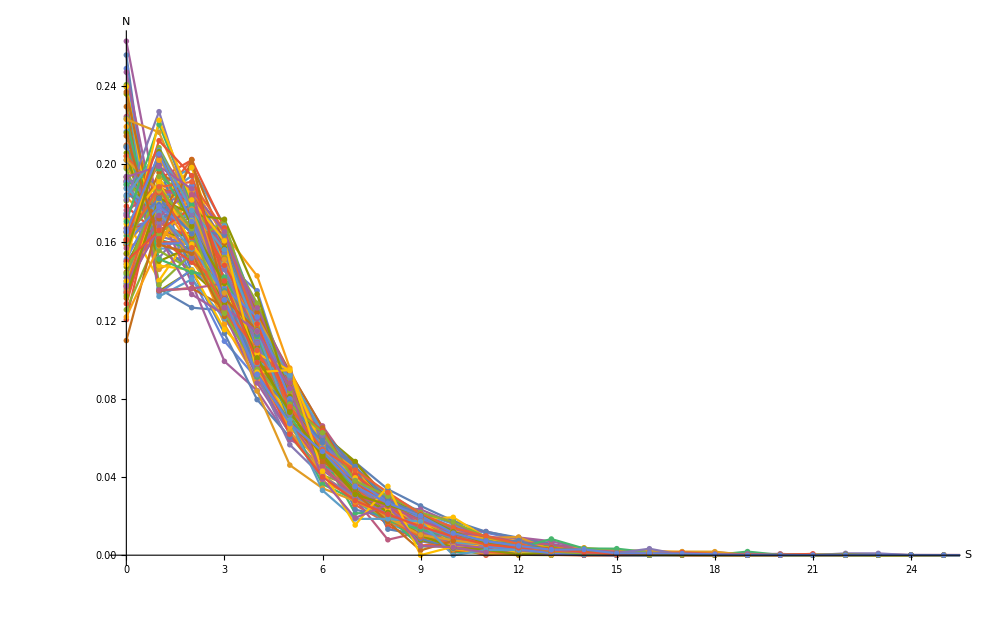

```mathematica
ListPlot[Table[({#⟦1⟧,#⟦2⟧/nblocks⟦i⟧})&/@sdistros⟦i⟧,{i,1,102}],PlotMarkers->fm["Disk",5],Joined->True, AxesLabel-> {"S","N"}, AxesStyle->{{Black, Large}, {Black, Large}},PlotRange->{{0,25},All}, ImageSize ->1000]
```

```mathematica
TableForm[SetPrecision[divMCL=Table[FindMaximum[{Total[
Table[Log[WilkHeSim2s[0,τ,θ,1,{k}]],{k,0,Length[sdistros⟦i⟧]-1}]
*(#⟦2⟧&/@sdistros⟦i⟧)],{0<τ<2,1/2<θ<10}},{τ,θ}],{i,1,102}],5]]
```

-7210.8 | τ→1.1206×10^-6
θ→2.9113
-5450.6 | τ→0.19024
θ→2.454
-1550.5 | τ→0.36758
θ→1.9346
-1518.8 | τ→0.38869
θ→1.8882
-4654.6 | τ→0.44668
θ→2.0175
-4936.6 | τ→0.53421
θ→2.0085
-4723.4 | τ→0.37461
θ→2.176
-8482.9 | τ→0.16254
θ→2.5411
-5552.9 | τ→0.58288
θ→1.934
-6945.4 | τ→0.19538
θ→2.4944
-4578.6 | τ→0.32008
θ→2.2405
-7331.7 | τ→0.065709
θ→2.8872
-5959.3 | τ→0.085768
θ→2.7107
-5860.2 | τ→0.14828
θ→2.5182
-4279.6 | τ→0.14731
θ→2.5745
-7301.3 | τ→0.17022
θ→2.563
-4565.2 | τ→0.39708
θ→2.1406
-7316.9 | τ→0.20952
θ→2.475
-5244.2 | τ→0.72094
θ→1.7234
-7703.5 | τ→0.22404
θ→2.4373
-4825.3 | τ→0.55309
θ→1.939
-2106.5 | τ→0.79663
θ→1.548
-3821.3 | τ→0.39477
θ→2.1922
-5730.4 | τ→8.4212×10^-9
θ→2.8658
-5448.1 | τ→0.067532
θ→2.7436
-4754.1 | τ→0.37892
θ→2.1607
-4886.9 | τ→0.056252
θ→2.6443
-4045.5 | τ→0.55926
θ→1.8247
-7806.5 | τ→0.21842
θ→2.4685
-6687.6 | τ→0.30054
θ→2.3349
-8672.6 | τ→0.070207
θ→2.9463
-7627.2 | τ→0.16264
θ→2.5728
-5464.7 | τ→0.064078
θ→2.6933
-4686.2 | τ→0.34298
θ→2.1135
-4670.6 | τ→0.55461
θ→1.8994
-5516.3 | τ→0.067258
θ→2.8318
-5306.8 | τ→0.029165
θ→2.9371
-6034.8 | τ→0.028597
θ→2.9155
-6646. | τ→0.0065997
θ→2.9795
-4271.4 | τ→0.14866
θ→2.4811
-3250.2 | τ→1.056
θ→1.3521
-3412.2 | τ→0.72518
θ→1.7029
-6973. | τ→0.37495
θ→2.2314
-4228.7 | τ→0.47403
θ→2.023
-2932.4 | τ→0.75248
θ→1.5943
-3071.1 | τ→0.59995
θ→1.8108
-8420.4 | τ→0.78924
θ→1.5924
-13966. | τ→0.70289
θ→1.8193
-4356.6 | τ→0.56328
θ→1.9006
-2770.5 | τ→0.49136
θ→1.8795
-2482. | τ→0.56527
θ→1.7343
-5869.3 | τ→0.47502
θ→2.0663
-5593.2 | τ→0.485
θ→2.0219
-7426.1 | τ→0.21891
θ→2.4341
-5346.1 | τ→0.22448
θ→2.3575
-5668.7 | τ→0.27619
θ→2.3215
-5707.4 | τ→0.3272
θ→2.1529
-6195.2 | τ→0.29607
θ→2.2761
-5675.7 | τ→0.10264
θ→2.7109
-4636.9 | τ→0.089789
θ→2.7338
-1452.8 | τ→0.31716
θ→2.0567
-5980. | τ→0.26664
θ→2.3692
-4841.7 | τ→0.52687
θ→1.9184
-1499. | τ→0.26389
θ→2.1277
-3842. | τ→0.64762
θ→1.7521
-10407. | τ→1.0151
θ→1.4886
-3520.8 | τ→0.70954
θ→1.6698
-3402.7 | τ→0.67346
θ→1.7067
-3586.5 | τ→0.75731
θ→1.6708
-3099.2 | τ→0.69591
θ→1.6459
-5997.7 | τ→0.47906
θ→2.0939
-3627.2 | τ→0.60278
θ→1.7523
-3697.4 | τ→1.0191
θ→1.4866
-1393.9 | τ→0.58144
θ→1.6513
-1396.6 | τ→0.40332
θ→1.855
-1378.9 | τ→0.50539
θ→1.7632
-1333.9 | τ→0.40437
θ→1.8162
-3978.9 | τ→0.5819
θ→1.8437
-3447.7 | τ→0.74457
θ→1.6082
-3981.1 | τ→0.26835
θ→2.2366
-4226.6 | τ→0.082891
θ→2.586
-3941.4 | τ→0.27963
θ→2.2565
-4177. | τ→0.37401
θ→2.0889
-3861.9 | τ→0.68258
θ→1.7342
-3370.5 | τ→0.81961
θ→1.5809
-6727.2 | τ→0.45184
θ→2.1021
-5380.5 | τ→0.39066
θ→2.1537
-6570.9 | τ→0.25799
θ→2.3623
-6561.4 | τ→0.26255
θ→2.407
-3822.9 | τ→0.2433
θ→2.3079
-7387.3 | τ→0.27568
θ→2.4119
-3580.4 | τ→0.16559
θ→2.1802
-7534.4 | τ→0.25857
θ→2.4902
-7678.8 | τ→0.25378
θ→2.5097
-3505.6 | τ→0.22083
θ→2.2817
-421.36 | τ→0.39401
θ→1.8022
-773.44 | τ→0.48819
θ→1.6977
-464.79 | τ→0.70093
θ→1.5332
-753.43 | τ→0.44909
θ→1.7318
-5890.7 | τ→0.31545
θ→2.2735
-3127.8 | τ→0.34061
θ→2.0954
-6470.6 | τ→0.24939
θ→2.3976

```mathematica
divMCL=Table[FindMaximum[{Total[
Table[Log[WilkHeSim2s[0,τ,θ,1,{k}]],{k,0,Length[sdistro⟦i⟧]-1}]
*(#⟦2⟧&/@sdistro⟦i⟧)],{0<τ<2,1/2<θ<10}},{τ,θ}],{i,1,102}]
```

{{-7210.82,{τ→1.12061×10^-6,θ→2.91134}},{-5450.65,{τ→0.190243,θ→2.45398}},{-1550.52,{τ→0.367576,θ→1.93457}},{-1518.76,{τ→0.388693,θ→1.88816}},{-4654.59,{τ→0.446679,θ→2.01752}},{-4936.58,{τ→0.53421,θ→2.00848}},{-4723.42,{τ→0.374613,θ→2.17597}},{-8482.94,{τ→0.162537,θ→2.54111}},{-5552.91,{τ→0.582879,θ→1.934}},{-6945.43,{τ→0.195375,θ→2.49438}},{-4578.56,{τ→0.320081,θ→2.24049}},{-7331.74,{τ→0.0657089,θ→2.88715}},{-5959.26,{τ→0.0857678,θ→2.71069}},{-5860.16,{τ→0.148282,θ→2.51817}},{-4279.57,{τ→0.147308,θ→2.57448}},{-7301.31,{τ→0.170215,θ→2.56298}},{-4565.18,{τ→0.397075,θ→2.14061}},{-7316.91,{τ→0.209516,θ→2.47504}},{-5244.2,{τ→0.720939,θ→1.72344}},{-7703.51,{τ→0.224036,θ→2.43734}},{-4825.32,{τ→0.553089,θ→1.93904}},{-2106.48,{τ→0.796631,θ→1.548}},{-3821.31,{τ→0.394771,θ→2.19223}},{-5730.43,{τ→8.42124×10^-9,θ→2.86579}},{-5448.12,{τ→0.0675324,θ→2.74361}},{-4754.11,{τ→0.378925,θ→2.16066}},{-4886.86,{τ→0.0562522,θ→2.64432}},{-4045.5,{τ→0.55926,θ→1.82468}},{-7806.51,{τ→0.218424,θ→2.46852}},{-6687.59,{τ→0.300538,θ→2.33487}},{-8672.59,{τ→0.0702073,θ→2.94631}},{-7627.21,{τ→0.162642,θ→2.57277}},{-5464.68,{τ→0.0640781,θ→2.69328}},{-4686.21,{τ→0.342984,θ→2.11347}},{-4670.56,{τ→0.554606,θ→1.89942}},{-5516.31,{τ→0.0672577,θ→2.8318}},{-5306.85,{τ→0.0291648,θ→2.93708}},{-6034.84,{τ→0.028597,θ→2.91551}},{-6645.97,{τ→0.00659973,θ→2.97949}},{-4271.44,{τ→0.148659,θ→2.48111}},{-3250.15,{τ→1.056,θ→1.35212}},{-3412.24,{τ→0.725177,θ→1.70288}},{-6972.98,{τ→0.374947,θ→2.23142}},{-4228.65,{τ→0.474027,θ→2.02295}},{-2932.37,{τ→0.752482,θ→1.59434}},{-3071.13,{τ→0.599949,θ→1.81076}},{-8420.42,{τ→0.789237,θ→1.59244}},{-13966.1,{τ→0.702891,θ→1.8193}},{-4356.61,{τ→0.563276,θ→1.9006}},{-2770.53,{τ→0.491364,θ→1.87949}},{-2481.99,{τ→0.565274,θ→1.73433}},{-5869.3,{τ→0.475016,θ→2.0663}},{-5593.16,{τ→0.485003,θ→2.02191}},{-7426.08,{τ→0.218914,θ→2.43406}},{-5346.06,{τ→0.224478,θ→2.35747}},{-5668.67,{τ→0.276193,θ→2.32152}},{-5707.41,{τ→0.3272,θ→2.15288}},{-6195.16,{τ→0.296069,θ→2.27609}},{-5675.68,{τ→0.102636,θ→2.7109}},{-4636.92,{τ→0.0897892,θ→2.73377}},{-1452.78,{τ→0.317156,θ→2.05666}},{-5979.98,{τ→0.266639,θ→2.3692}},{-4841.68,{τ→0.526873,θ→1.91837}},{-1499.03,{τ→0.26389,θ→2.12771}},{-3841.95,{τ→0.647619,θ→1.75212}},{-10407.,{τ→1.01514,θ→1.48863}},{-3520.83,{τ→0.709545,θ→1.66975}},{-3402.66,{τ→0.67346,θ→1.70671}},{-3586.51,{τ→0.757311,θ→1.6708}},{-3099.21,{τ→0.695915,θ→1.6459}},{-5997.67,{τ→0.479064,θ→2.09388}},{-3627.16,{τ→0.602776,θ→1.75226}},{-3697.42,{τ→1.01913,θ→1.48665}},{-1393.94,{τ→0.581444,θ→1.6513}},{-1396.61,{τ→0.40332,θ→1.85499}},{-1378.86,{τ→0.505395,θ→1.76316}},{-1333.95,{τ→0.404366,θ→1.81615}},{-3978.89,{τ→0.581899,θ→1.84375}},{-3447.74,{τ→0.744574,θ→1.60819}},{-3981.05,{τ→0.268353,θ→2.2366}},{-4226.56,{τ→0.0828906,θ→2.58596}},{-3941.41,{τ→0.279632,θ→2.25651}},{-4177.,{τ→0.374009,θ→2.08887}},{-3861.88,{τ→0.682578,θ→1.73422}},{-3370.54,{τ→0.819613,θ→1.58091}},{-6727.23,{τ→0.451838,θ→2.10207}},{-5380.5,{τ→0.390663,θ→2.15371}},{-6570.93,{τ→0.257995,θ→2.3623}},{-6561.43,{τ→0.262551,θ→2.40704}},{-3822.9,{τ→0.243303,θ→2.30786}},{-7387.31,{τ→0.275676,θ→2.41193}},{-3580.41,{τ→0.165586,θ→2.18021}},{-7534.44,{τ→0.258569,θ→2.49023}},{-7678.78,{τ→0.253776,θ→2.5097}},{-3505.61,{τ→0.220832,θ→2.28171}},{-421.358,{τ→0.39401,θ→1.80218}},{-773.444,{τ→0.488185,θ→1.69772}},{-464.789,{τ→0.700935,θ→1.53323}},{-753.431,{τ→0.449094,θ→1.7318}},{-5890.69,{τ→0.315445,θ→2.27348}},{-3127.79,{τ→0.340611,θ→2.09536}},{-6470.56,{τ→0.249388,θ→2.39761}}}

#### Fitting the IM model

```mathematica
TableForm[SetPrecision[imMCL=Table[FindMaximum[{Total[
Table[Log[WilkHeSim2s[M, τ,θ,1,{k}]],{k,0,Length[sdistros⟦i⟧]-1}]
*(#⟦2⟧&/@sdistros⟦i⟧)],{1/1000<M< 15,1/1000<τ<15,1/1000<θ<6}},{M,τ,θ}],{i,1,102}],5]]
```

Part::partd: Part specification sdistros⟦1⟧ is longer than depth of object.

Part::partd: Part specification sdistros⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression 1⟦2⟧ cannot be used as a part specification.

FindMaximum::nrnum: The function value 2.02664 sdistros⟦2⟧⟦1⟦2⟧⟧ is not a real number at {M,τ,θ} = {1.00099,1.001,0.6009}.

FindMaximum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[-(Log[If[«3»]] Part[«2»]⟦Part[«2»]⟧+Log[If[«3»]] Part[«2»]⟦Part[«2»]⟧)],Block},{0,{{{},1,0,Hold[M],0,0},{{},1,1,Hold[τ],0,0},{{},1,2,Hold[θ],0,0}}},{{{1,3,817},{{Automatic,Automatic,{Hold[Automatic],Block},2,Automatic,Automatic},{}}}},{«1»},{904,MachinePrecision,{{Automatic},{Hold[Block[{Compile`$6,Compile`$11,Compile`$12,Compile`$13,Compile`$24,Compile`$7,Compile`$1,Compile`$2,Compile`$3,Compile`$5,«27»},Set[«2»];Set[«2»];Set[«2»];Times[«2»]]],Block}},True,{«1»},FindMaximum,Automatic,None},{None,None,None}] failed at {1.001,1.001,0.6009}.

Part::pkspec1: The expression 2⟦2⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindMaximum::nrnum: The function value 2.02664 sdistros⟦2⟧⟦2⟦2⟧⟧ is not a real number at {M,τ,θ} = {1.00099,1.001,0.6009}.

FindMaximum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[-(Log[If[«3»]] Part[«2»]⟦Part[«2»]⟧+Log[If[«3»]] Part[«2»]⟦Part[«2»]⟧)],Block},{0,{{{},1,0,Hold[M],0,0},{{},1,1,Hold[τ],0,0},{{},1,2,Hold[θ],0,0}}},{{{1,3,817},{{Automatic,Automatic,{Hold[Automatic],Block},2,Automatic,Automatic},{}}}},{«1»},{904,MachinePrecision,{{Automatic},{Hold[Block[{Compile`$6,Compile`$11,Compile`$12,Compile`$13,Compile`$24,Compile`$7,Compile`$1,Compile`$2,Compile`$3,Compile`$5,«27»},Set[«2»];Set[«2»];Set[«2»];Times[«2»]]],Block}},True,{«1»},FindMaximum,Automatic,None},{None,None,None}] failed at {1.001,1.001,0.6009}.

FindMaximum::nrnum: The function value 2.02664 sdistros⟦2⟧⟦3⟦2⟧⟧ is not a real number at {M,τ,θ} = {1.00099,1.001,0.6009}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[-(Log[If[«3»]] Part[«2»]⟦Part[«2»]⟧+Log[If[«3»]] Part[«2»]⟦Part[«2»]⟧)],Block},{0,{{{},1,0,Hold[M],0,0},{{},1,1,Hold[τ],0,0},{{},1,2,Hold[θ],0,0}}},{{{1,3,817},{{Automatic,Automatic,{Hold[Automatic],Block},2,Automatic,Automatic},{}}}},{«1»},{904,MachinePrecision,{{Automatic},{Hold[Block[{Compile`$6,Compile`$11,Compile`$12,Compile`$13,Compile`$24,Compile`$7,Compile`$1,Compile`$2,Compile`$3,Compile`$5,«27»},Set[«2»];Set[«2»];Set[«2»];Times[«2»]]],Block}},True,{«1»},FindMaximum,Automatic,None},{None,None,None}] failed at {1.001,1.001,0.6009}.

General::stop: Further output of FindMaximum::grad will be suppressed during this calculation.

FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]
FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1.,{k}]],{k,0,Length[sdistros⟦i⟧]-1.}] (#1⟦2⟧&)/@sdistros⟦i⟧],{1. 0.001<M<15.,1. 0.001<τ<15.,1. 0.001<θ<6.}},{M,τ,θ}]

```mathematica
deltaIM= (Table[imMCL⟦i,1⟧-divMCL⟦i,1⟧,{i,1,102}]/nblocks)*500
```

{5.71026,13.0262,3.99129,6.28946,14.9507,10.732,13.8997,8.34997,9.8551,7.73695,8.39552,2.42818,1.186,1.7465,7.36969,11.9809,12.1844,11.8744,7.75568,8.29882,2.65465,2.39267,10.6455,2.51192,10.9766,9.46724,10.4539,10.3974,0.278495,2.52955,2.78328,6.62731,9.12057,14.2239,8.31074,11.6213,9.74284,3.16084,2.78789,6.27905,3.5721,8.91621,3.61186,10.6418,5.54846,8.72005,7.24996,6.35574,3.64805,6.96525,6.22305,4.5113,2.63669,-1.15959,15.7545,14.2044,12.4403,12.2928,12.3252,6.37683,11.3081,-3.25652,2.14485,11.5385,5.42175,5.08902,6.43444,5.15255,8.0617,7.74895,0.903529,6.57691,8.16694,8.70044,8.84222,12.1319,11.9475,6.35647,4.33163,9.33726,5.95776,12.5808,11.2197,5.06018,6.04156,5.52699,8.30434,-2.33003,-3.03576,-2.44845,6.11526,-0.455417,5.65752,5.46812,-2.85068,13.1678,4.27297,4.39559,8.96001,-1.19473,-5.70887,-0.756603}

#### Fitting the IIM model

```mathematica
iimMCL=Table[FindMaximum[{Total[Table[Log[WilkHeSimIIMs[M,τ1,τ1+τ0,θ,1,{k}]],{k,0,Length[sdistros⟦i⟧]-1}]*(#⟦2⟧&/@sdistros⟦i⟧)],{0/1000<M<16,1/1000<τ1<3,1/1000<τ0<12,1/1000<θ<8}},{M,τ1,τ0,θ}],{i,1,102}]
```

{{-7140.62,{M→16.,τ1→0.00100003,τ0→2.52642,θ→1.6477}},{-5387.84,{M→0.178401,τ1→0.00100032,τ0→12.,θ→0.450585}},{-1543.35,{M→0.250094,τ1→0.547118,τ0→11.9997,θ→0.437738}},{-1509.65,{M→1.06459,τ1→0.00100192,τ0→2.91051,θ→1.11659}},{-4590.93,{M→0.114516,τ1→0.00100135,τ0→11.9999,θ→0.37136}},{-4888.61,{M→0.364174,τ1→0.00100436,τ0→4.69979,θ→0.859172}},{-4664.02,{M→0.130659,τ1→0.00100148,τ0→11.9997,θ→0.401337}},{-8419.26,{M→6.31907,τ1→0.00100029,τ0→2.14753,θ→1.67648}},{-5503.04,{M→0.372804,τ1→0.0358234,τ0→4.46045,θ→0.867735}},{-6897.19,{M→2.81042,τ1→0.0010004,τ0→2.68878,θ→1.50532}},{-4543.71,{M→1.15763,τ1→0.00100054,τ0→3.10683,θ→1.25717}},{-7303.98,{M→8.71473,τ1→0.00100185,τ0→3.81245,θ→1.5809}},{-5952.93,{M→2.38045,τ1→0.00100085,τ0→6.90022,θ→1.24702}},{-5850.89,{M→0.575052,τ1→0.00100125,τ0→11.9996,θ→0.786551}},{-4251.23,{M→15.9979,τ1→0.00100072,τ0→1.81991,θ→1.80296}},{-7224.95,{M→0.194351,τ1→0.00100025,τ0→12.,θ→0.482011}},{-4514.69,{M→0.223104,τ1→0.0010022,τ0→8.03998,θ→0.580055}},{-7240.,{M→0.176114,τ1→0.0010003,τ0→12.,θ→0.458811}},{-5206.1,{M→0.346084,τ1→0.181651,τ0→4.47631,θ→0.790516}},{-7646.07,{M→2.69569,τ1→0.00100024,τ0→2.42744,θ→1.53623}},{-4812.13,{M→2.96461,τ1→0.321947,τ0→1.96139,θ→1.40659}},{-2101.65,{M→0.521203,τ1→0.0010093,τ0→1.65174,θ→1.27154}},{-3784.79,{M→1.0681,τ1→0.0010003,τ0→2.57102,θ→1.35005}},{-5717.32,{M→15.9999,τ1→0.00100008,τ0→5.02708,θ→1.44949}},{-5397.51,{M→0.212085,τ1→0.00100015,τ0→12.,θ→0.491401}},{-4713.24,{M→0.597268,τ1→0.00100097,τ0→4.29214,θ→0.987134}},{-4843.08,{M→0.204336,τ1→0.00100016,τ0→12.,θ→0.46023}},{-4006.22,{M→0.249876,τ1→0.00104513,τ0→6.1493,θ→0.636554}},{-7799.22,{M→0.616565,τ1→0.208256,τ0→11.9997,θ→0.796333}},{-6682.32,{M→0.673253,τ1→0.426131,τ0→11.9999,θ→0.785717}},{-8638.54,{M→5.46143,τ1→0.00100153,τ0→4.39774,θ→1.54163}},{-7581.96,{M→6.23801,τ1→0.00100083,τ0→2.17674,θ→1.69293}},{-5422.45,{M→0.232295,τ1→0.00100015,τ0→12.,θ→0.502741}},{-4625.26,{M→0.136491,τ1→0.00100091,τ0→12.,θ→0.388096}},{-4634.48,{M→0.343644,τ1→0.179614,τ0→5.63374,θ→0.724299}},{-5462.64,{M→0.204219,τ1→0.00100014,τ0→12.,θ→0.497839}},{-5265.02,{M→0.225387,τ1→0.00100012,τ0→12.,θ→0.522869}},{-5998.42,{M→15.9999,τ1→0.00100008,τ0→3.02951,θ→1.6383}},{-6629.44,{M→15.9999,τ1→0.0010001,τ0→4.69235,θ→1.52863}},{-4246.98,{M→15.9998,τ1→0.00100029,τ0→1.63146,θ→1.787}},{-3235.89,{M→0.134713,τ1→2.43521,τ0→11.9992,θ→0.283961}},{-3383.39,{M→0.219586,τ1→0.334658,τ0→6.62786,θ→0.571497}},{-6965.85,{M→0.617146,τ1→0.623471,τ0→11.9999,θ→0.732699}},{-4187.53,{M→0.324979,τ1→0.0122362,τ0→5.6701,θ→0.747374}},{-2916.88,{M→0.47422,τ1→0.00100762,τ0→2.64586,θ→1.04045}},{-3046.17,{M→0.345904,τ1→0.0755152,τ0→4.85776,θ→0.770316}},{-8360.04,{M→0.177038,τ1→0.738476,τ0→8.4247,θ→0.440995}},{-13884.4,{M→0.537701,τ1→0.15134,τ0→3.16686,θ→1.0497}},{-4339.13,{M→1.01179,τ1→0.4088,τ0→3.83646,θ→1.00233}},{-2752.46,{M→0.76081,τ1→0.00100216,τ0→2.91948,θ→1.11202}},{-2465.77,{M→0.163536,τ1→0.922411,τ0→11.9992,θ→0.353737}},{-5844.32,{M→1.33068,τ1→0.224267,τ0→3.03922,θ→1.21949}},{-5573.96,{M→0.776446,τ1→0.505619,τ0→5.7211,θ→0.857033}},{-7425.17,{M→2.37099,τ1→0.313545,τ0→11.9995,θ→1.08717}},{-5271.07,{M→0.160065,τ1→0.00100036,τ0→12.,θ→0.423814}},{-5596.62,{M→0.151667,τ1→0.0010006,τ0→12.,θ→0.424236}},{-5642.37,{M→0.145256,τ1→0.00100085,τ0→11.9999,θ→0.401162}},{-6126.27,{M→0.154732,τ1→0.00100102,τ0→11.9999,θ→0.425991}},{-5615.78,{M→0.192544,τ1→0.00100017,τ0→12.,θ→0.478302}},{-4610.44,{M→15.9999,τ1→0.0010001,τ0→1.87712,θ→1.80977}},{-1437.39,{M→0.156382,τ1→0.00102536,τ0→11.9999,θ→0.393225}},{-5980.89,{M→15.9982,τ1→0.504096,τ0→12.,θ→1.17234}},{-4830.82,{M→6.30004,τ1→0.360082,τ0→1.78794,θ→1.434}},{-1482.99,{M→0.164421,τ1→0.00100131,τ0→11.9999,θ→0.399492}},{-3822.2,{M→0.633987,τ1→0.202386,τ0→3.3547,θ→0.978384}},{-10345.9,{M→0.124636,τ1→2.17646,τ0→11.9998,θ→0.306947}},{-3498.35,{M→0.287999,τ1→0.519924,τ0→6.36535,θ→0.590081}},{-3384.23,{M→0.236192,τ1→0.941605,τ0→8.93329,θ→0.463322}},{-3559.5,{M→0.335198,τ1→0.00102432,τ0→3.71316,θ→0.880782}},{-3075.47,{M→0.136509,τ1→0.890101,τ0→11.2173,θ→0.348496}},{-5990.22,{M→15.9947,τ1→0.704452,τ0→4.19603,θ→1.17593}},{-3603.35,{M→0.236962,τ1→0.603255,τ0→8.38951,θ→0.491554}},{-3669.09,{M→0.219091,τ1→0.00100483,τ0→3.94842,θ→0.795453}},{-1382.23,{M→0.38033,τ1→0.00100197,τ0→4.38498,θ→0.75668}},{-1384.78,{M→0.274013,τ1→0.00101192,τ0→7.30897,θ→0.564308}},{-1362.9,{M→0.110353,τ1→0.00100434,τ0→11.9995,θ→0.332868}},{-1318.67,{M→0.12884,τ1→0.00100236,τ0→11.9999,θ→0.340386}},{-3955.15,{M→0.589314,τ1→0.153781,τ0→3.7165,θ→0.956888}},{-3432.09,{M→0.347886,τ1→0.79471,τ0→6.52414,θ→0.576532}},{-3947.32,{M→0.26869,τ1→0.00100095,τ0→8.95234,θ→0.572929}},{-4195.33,{M→15.9999,τ1→0.00100019,τ0→2.37867,θ→1.60786}},{-3896.43,{M→0.158499,τ1→0.00100144,τ0→11.9999,θ→0.421719}},{-4133.54,{M→0.150492,τ1→0.170695,τ0→11.9998,θ→0.399774}},{-3843.57,{M→0.637013,τ1→0.14124,τ0→2.86281,θ→1.06413}},{-3351.27,{M→0.399344,τ1→0.058955,τ0→3.07087,θ→0.954181}},{-6693.57,{M→1.29903,τ1→0.00100093,τ0→1.83352,θ→1.5419}},{-5339.72,{M→0.389231,τ1→0.0949785,τ0→6.32867,θ→0.754382}},{-6570.04,{M→2.85911,τ1→0.411237,τ0→11.5855,θ→1.07911}},{-6561.59,{M→15.9951,τ1→0.499107,τ0→11.9999,θ→1.18809}},{-3822.65,{M→15.9888,τ1→0.460031,τ0→11.999,θ→1.13915}},{-7346.34,{M→0.443716,τ1→0.0963507,τ0→7.68257,θ→0.775687}},{-3580.69,{M→15.9974,τ1→0.298929,τ0→12.,θ→1.07997}},{-7494.6,{M→0.258743,τ1→0.23687,τ0→11.9999,θ→0.555698}},{-7640.47,{M→0.284122,τ1→0.192478,τ0→11.2979,θ→0.594723}},{-3507.35,{M→15.9992,τ1→0.405417,τ0→12.,θ→1.13536}},{-416.042,{M→0.128753,τ1→0.00100127,τ0→11.9999,θ→0.335253}},{-770.222,{M→1.17427,τ1→0.00100366,τ0→1.98379,θ→1.22737}},{-462.066,{M→0.160506,τ1→1.4075,τ0→11.9998,θ→0.317439}},{-746.845,{M→0.151059,τ1→0.157501,τ0→11.1615,θ→0.359987}},{-5884.01,{M→1.73203,τ1→0.401384,τ0→6.57327,θ→1.03492}},{-3127.87,{M→15.9952,τ1→0.654171,τ0→11.9999,θ→1.03608}},{-6465.98,{M→15.9983,τ1→0.383214,τ0→5.12909,θ→1.26898}}}

```mathematica
Export["/Users/leebanyusuf/Desktop/Drosophilomics_project/IMmodel_FLEX_test.csv",imMCL,"CSV"]
Export["/Users/leebanyusuf/Desktop/Drosophilomics_project/DivModel_FLEX_test.csv",divMCL,"CSV"]
Export["/Users/leebanyusuf/Desktop/Drosophilomics_project/IIMModel_FLEX_test.csv",iimMCL,"CSV"]
Export["/Users/leebanyusuf/Desktop/Drosophilomics_project/MutationTypeFrequencies_FLEX_test.csv", MutTypesPairs, "CSV"]
```

/Users/leebanyusuf/Desktop/Drosophilomics_project/IMmodel_FLEX_test.csv

/Users/leebanyusuf/Desktop/Drosophilomics_project/MutationTypeFrequencies_FLEX_test.csv

```mathematica
imclsurface=Table[{M,FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1,{k}]],{k,0,Length[sdistros[[i]]]-1}]*(#[[2]]&/@sdistros[[i]])],{1/1000<τ<5,1/1000<θ<6}},{τ,θ}]},{i,1,102},{M,0.5,10, 0.5}]
```

{{{0.5,{-7219.12,{τ→5.,θ→0.902171}}},{1.,{-7180.39,{τ→5.,θ→1.07088}}},{1.5,{-7172.63,{τ→4.48213,θ→1.1936}}},{2.,{-7167.11,{τ→3.97259,θ→1.28617}}},{2.5,{-7162.84,{τ→3.65662,θ→1.35073}}},{3.,{-7159.49,{τ→3.44127,θ→1.39851}}},{3.5,{-7156.82,{τ→3.28499,θ→1.43537}}},{4.,{-7154.64,{τ→3.16636,θ→1.4647}}},{4.5,{-7152.84,{τ→3.07322,θ→1.48862}}},{5.,{-7151.33,{τ→2.99814,θ→1.5085}}},{5.5,{-7150.04,{τ→2.93632,θ→1.5253}}},{6.,{-7148.93,{τ→2.88453,θ→1.53968}}},{6.5,{-7147.97,{τ→2.84051,θ→1.55214}}},{7.,{-7147.13,{τ→2.80264,θ→1.56303}}},{7.5,{-7146.38,{τ→2.76971,θ→1.57264}}},{8.,{-7145.71,{τ→2.74081,θ→1.58117}}},{8.5,{-7145.12,{τ→2.71524,θ→1.58881}}},{9.,{-7144.58,{τ→2.69246,θ→1.59568}}},{9.5,{-7144.1,{τ→2.67204,θ→1.60189}}},{10.,{-7143.66,{τ→2.65363,θ→1.60754}}}},{{0.5,{-5395.21,{τ→5.,θ→0.887419}}},{1.,{-5390.76,{τ→4.03828,θ→1.12305}}},{1.5,{-5390.1,{τ→3.25572,θ→1.28601}}},{2.,{-5389.71,{τ→2.84533,θ→1.39106}}},{2.5,{-5389.52,{τ→2.59403,θ→1.46456}}},{3.,{-5389.46,{τ→2.42508,θ→1.51885}}},{3.5,{-5389.47,{τ→2.30407,θ→1.56054}}},{4.,{-5389.52,{τ→2.21332,θ→1.59355}}},{4.5,{-5389.59,{τ→2.14284,θ→1.62031}}},{5.,{-5389.67,{τ→2.08658,θ→1.64243}}},{5.5,{-5389.76,{τ→2.04066,θ→1.66102}}},{6.,{-5389.85,{τ→2.0025,θ→1.67685}}},{6.5,{-5389.93,{τ→1.97029,θ→1.69049}}},{7.,{-5390.01,{τ→1.94274,θ→1.70237}}},{7.5,{-5390.09,{τ→1.91893,θ→1.7128}}},{8.,{-5390.17,{τ→1.89815,θ→1.72203}}},{8.5,{-5390.24,{τ→1.87984,θ→1.73026}}},{9.,{-5390.31,{τ→1.86361,θ→1.73764}}},{9.5,{-5390.38,{τ→1.84911,θ→1.7443}}},{10.,{-5390.44,{τ→1.83608,θ→1.75033}}}},{{0.5,{-1545.4,{τ→5.,θ→0.801398}}},{1.,{-1545.17,{τ→3.74822,θ→1.03875}}},{1.5,{-1545.64,{τ→2.70736,θ→1.22435}}},{2.,{-1545.96,{τ→2.08454,θ→1.36947}}},{2.5,{-1546.22,{τ→1.72134,θ→1.47884}}},{3.,{-1546.49,{τ→1.52511,θ→1.55328}}},{3.5,{-1546.77,{τ→1.41299,θ→1.60416}}},{4.,{-1547.04,{τ→1.34194,θ→1.64087}}},{4.5,{-1547.3,{τ→1.29294,θ→1.66871}}},{5.,{-1547.55,{τ→1.25701,θ→1.69062}}},{5.5,{-1547.77,{τ→1.22948,θ→1.70836}}},{6.,{-1547.98,{τ→1.20767,θ→1.72303}}},{6.5,{-1548.18,{τ→1.18995,θ→1.73539}}},{7.,{-1548.36,{τ→1.17525,θ→1.74594}}},{7.5,{-1548.52,{τ→1.16285,θ→1.75505}}},{8.,{-1548.67,{τ→1.15225,θ→1.76301}}},{8.5,{-1548.82,{τ→1.14308,θ→1.77002}}},{9.,{-1548.95,{τ→1.13506,θ→1.77623}}},{9.5,{-1549.07,{τ→1.128,θ→1.78179}}},{10.,{-1549.18,{τ→1.12172,θ→1.78678}}}},{{0.5,{-1510.03,{τ→5.,θ→0.788956}}},{1.,{-1509.65,{τ→3.03484,θ→1.08995}}},{1.5,{-1509.78,{τ→2.32401,θ→1.26403}}},{2.,{-1510.11,{τ→1.98328,θ→1.37416}}},{2.5,{-1510.52,{τ→1.79147,θ→1.44847}}},{3.,{-1510.92,{τ→1.67084,θ→1.50143}}},{3.5,{-1511.29,{τ→1.58871,θ→1.54089}}},{4.,{-1511.64,{τ→1.52944,θ→1.57135}}},{4.5,{-1511.95,{τ→1.48476,θ→1.59553}}},{5.,{-1512.23,{τ→1.44992,θ→1.61518}}},{5.5,{-1512.48,{τ→1.42202,θ→1.63145}}},{6.,{-1512.71,{τ→1.39919,θ→1.64514}}},{6.5,{-1512.91,{τ→1.38017,θ→1.65681}}},{7.,{-1513.1,{τ→1.36408,θ→1.66687}}},{7.5,{-1513.27,{τ→1.3503,θ→1.67563}}},{8.,{-1513.42,{τ→1.33837,θ→1.68333}}},{8.5,{-1513.56,{τ→1.32793,θ→1.69015}}},{9.,{-1513.69,{τ→1.31874,θ→1.69623}}},{9.5,{-1513.81,{τ→1.31057,θ→1.70168}}},{10.,{-1513.92,{τ→1.30327,θ→1.70659}}}},{{0.5,{-4593.57,{τ→4.14169,θ→0.930434}}},{1.,{-4597.42,{τ→2.71664,θ→1.25049}}},{1.5,{-4601.23,{τ→2.22829,θ→1.42031}}},{2.,{-4604.55,{τ→1.98678,θ→1.52502}}},{2.5,{-4607.34,{τ→1.84402,θ→1.59577}}},{3.,{-4609.67,{τ→1.75011,θ→1.64663}}},{3.5,{-4611.63,{τ→1.68381,θ→1.68489}}},{4.,{-4613.3,{τ→1.63456,θ→1.71467}}},{4.5,{-4614.73,{τ→1.59658,θ→1.73849}}},{5.,{-4615.96,{τ→1.5664,θ→1.75796}}},{5.5,{-4617.04,{τ→1.54187,θ→1.77417}}},{6.,{-4617.99,{τ→1.52154,θ→1.78786}}},{6.5,{-4618.83,{τ→1.50442,θ→1.79958}}},{7.,{-4619.58,{τ→1.4898,θ→1.80972}}},{7.5,{-4620.25,{τ→1.47719,θ→1.81858}}},{8.,{-4620.85,{τ→1.46619,θ→1.82638}}},{8.5,{-4621.4,{τ→1.45652,θ→1.8333}}},{9.,{-4621.9,{τ→1.44795,θ→1.83949}}},{9.5,{-4622.36,{τ→1.4403,θ→1.84505}}},{10.,{-4622.78,{τ→1.43343,θ→1.85007}}}},{{0.5,{-4888.92,{τ→3.72164,θ→1.01983}}},{1.,{-4892.87,{τ→2.35148,θ→1.38081}}},{1.5,{-4897.94,{τ→1.91486,θ→1.56727}}},{2.,{-4902.64,{τ→1.70921,θ→1.67943}}},{2.5,{-4906.68,{τ→1.59067,θ→1.75408}}},{3.,{-4910.11,{τ→1.51378,θ→1.80724}}},{3.5,{-4913.01,{τ→1.45995,θ→1.84694}}},{4.,{-4915.49,{τ→1.42021,θ→1.87768}}},{4.5,{-4917.62,{τ→1.38968,θ→1.90215}}},{5.,{-4919.48,{τ→1.36551,θ→1.92207}}},{5.5,{-4921.1,{τ→1.34592,θ→1.93859}}},{6.,{-4922.53,{τ→1.32972,θ→1.9525}}},{6.5,{-4923.79,{τ→1.3161,θ→1.96437}}},{7.,{-4924.93,{τ→1.30451,θ→1.97462}}},{7.5,{-4925.94,{τ→1.29451,θ→1.98354}}},{8.,{-4926.86,{τ→1.28581,θ→1.99139}}},{8.5,{-4927.7,{τ→1.27817,θ→1.99833}}},{9.,{-4928.46,{τ→1.27141,θ→2.00452}}},{9.5,{-4929.15,{τ→1.26538,θ→2.01008}}},{10.,{-4929.79,{τ→1.25997,θ→2.01509}}}},{{0.5,{-4665.69,{τ→4.61231,θ→0.920874}}},{1.,{-4667.89,{τ→2.97545,θ→1.2481}}},{1.5,{-4670.23,{τ→2.39884,θ→1.42645}}},{2.,{-4672.44,{τ→2.11276,θ→1.53783}}},{2.5,{-4674.41,{τ→1.94426,θ→1.61351}}},{3.,{-4676.12,{τ→1.83395,θ→1.6681}}},{3.5,{-4677.6,{τ→1.7564,θ→1.70923}}},{4.,{-4678.88,{τ→1.69902,θ→1.7413}}},{4.5,{-4679.99,{τ→1.6549,θ→1.76697}}},{5.,{-4680.97,{τ→1.61994,θ→1.78797}}},{5.5,{-4681.83,{τ→1.59158,θ→1.80546}}},{6.,{-4682.59,{τ→1.56813,θ→1.82024}}},{6.5,{-4683.27,{τ→1.54841,θ→1.83289}}},{7.,{-4683.88,{τ→1.53161,θ→1.84384}}},{7.5,{-4684.43,{τ→1.51712,θ→1.85341}}},{8.,{-4684.93,{τ→1.5045,θ→1.86184}}},{8.5,{-4685.39,{τ→1.49342,θ→1.86933}}},{9.,{-4685.8,{τ→1.4836,θ→1.87601}}},{9.5,{-4686.18,{τ→1.47485,θ→1.88202}}},{10.,{-4686.54,{τ→1.467,θ→1.88745}}}},{{0.5,{-8451.36,{τ→5.,θ→0.906993}}},{1.,{-8426.17,{τ→4.85897,θ→1.09132}}},{1.5,{-8423.71,{τ→3.85546,θ→1.25338}}},{2.,{-8422.06,{τ→3.31734,θ→1.36021}}},{2.5,{-8421.,{τ→2.9821,θ→1.43663}}},{3.,{-8420.32,{τ→2.75376,θ→1.4942}}},{3.5,{-8419.87,{τ→2.58862,θ→1.53915}}},{4.,{-8419.59,{τ→2.46388,θ→1.57523}}},{4.5,{-8419.41,{τ→2.3665,θ→1.60481}}},{5.,{-8419.31,{τ→2.28847,θ→1.6295}}},{5.5,{-8419.25,{τ→2.22461,θ→1.6504}}},{6.,{-8419.23,{τ→2.17143,θ→1.66831}}},{6.5,{-8419.23,{τ→2.12649,θ→1.68384}}},{7.,{-8419.25,{τ→2.08803,θ→1.69742}}},{7.5,{-8419.28,{τ→2.05476,θ→1.70939}}},{8.,{-8419.31,{τ→2.02571,θ→1.72002}}},{8.5,{-8419.36,{τ→2.00013,θ→1.72952}}},{9.,{-8419.4,{τ→1.97744,θ→1.73806}}},{9.5,{-8419.45,{τ→1.95718,θ→1.74578}}},{10.,{-8419.5,{τ→1.93898,θ→1.75279}}}},{{0.5,{-5503.44,{τ→3.4753,θ→1.0384}}},{1.,{-5508.95,{τ→2.2177,θ→1.3972}}},{1.5,{-5515.87,{τ→1.82661,θ→1.57853}}},{2.,{-5522.11,{τ→1.64152,θ→1.68727}}},{2.5,{-5527.4,{τ→1.53404,θ→1.75969}}},{3.,{-5531.85,{τ→1.46391,θ→1.81128}}},{3.5,{-5535.59,{τ→1.41462,θ→1.84983}}},{4.,{-5538.78,{τ→1.37813,θ→1.87966}}},{4.5,{-5541.5,{τ→1.35004,θ→1.90341}}},{5.,{-5543.87,{τ→1.32777,θ→1.92273}}},{5.5,{-5545.93,{τ→1.3097,θ→1.93874}}},{6.,{-5547.74,{τ→1.29475,θ→1.95222}}},{6.5,{-5549.35,{τ→1.28217,θ→1.96372}}},{7.,{-5550.78,{τ→1.27146,θ→1.97363}}},{7.5,{-5552.07,{τ→1.26223,θ→1.98227}}},{8.,{-5553.23,{τ→1.25418,θ→1.98985}}},{8.5,{-5554.28,{τ→1.24712,θ→1.99657}}},{9.,{-5555.24,{τ→1.24087,θ→2.00255}}},{9.5,{-5556.12,{τ→1.23529,θ→2.00792}}},{10.,{-5556.92,{τ→1.2303,θ→2.01275}}}},{{0.5,{-6915.13,{τ→5.,θ→0.913661}}},{1.,{-6898.67,{τ→4.69549,θ→1.10967}}},{1.5,{-6897.81,{τ→3.70764,θ→1.27626}}},{2.,{-6897.36,{τ→3.17135,θ→1.38725}}},{2.5,{-6897.19,{τ→2.8347,θ→1.46737}}},{3.,{-6897.18,{τ→2.60454,θ→1.52813}}},{3.5,{-6897.26,{τ→2.43791,θ→1.57579}}},{4.,{-6897.4,{τ→2.31214,θ→1.61415}}},{4.5,{-6897.57,{τ→2.21413,θ→1.64565}}},{5.,{-6897.75,{τ→2.1358,θ→1.67195}}},{5.5,{-6897.94,{τ→2.07187,θ→1.69422}}},{6.,{-6898.12,{τ→2.0188,θ→1.7133}}},{6.5,{-6898.31,{τ→1.97408,θ→1.72981}}},{7.,{-6898.48,{τ→1.93593,θ→1.74424}}},{7.5,{-6898.65,{τ→1.90302,θ→1.75695}}},{8.,{-6898.82,{τ→1.87437,θ→1.76822}}},{8.5,{-6898.97,{τ→1.8492,θ→1.77829}}},{9.,{-6899.12,{τ→1.82693,θ→1.78732}}},{9.5,{-6899.26,{τ→1.80709,θ→1.79548}}},{10.,{-6899.39,{τ→1.78932,θ→1.80288}}}},{{0.5,{-4545.09,{τ→5.,θ→0.89363}}},{1.,{-4543.72,{τ→3.42865,θ→1.18805}}},{1.5,{-4543.81,{τ→2.61588,θ→1.38003}}},{2.,{-4544.27,{τ→2.20761,θ→1.50578}}},{2.5,{-4544.92,{τ→1.97241,θ→1.59267}}},{3.,{-4545.63,{τ→1.82318,θ→1.65544}}},{3.5,{-4546.33,{τ→1.72136,θ→1.70256}}},{4.,{-4547.,{τ→1.64794,θ→1.73909}}},{4.5,{-4547.62,{τ→1.59269,θ→1.76818}}},{5.,{-4548.2,{τ→1.5497,θ→1.79186}}},{5.5,{-4548.72,{τ→1.51534,θ→1.81149}}},{6.,{-4549.2,{τ→1.48727,θ→1.82802}}},{6.5,{-4549.63,{τ→1.46392,θ→1.84212}}},{7.,{-4550.03,{τ→1.4442,θ→1.85429}}},{7.5,{-4550.4,{τ→1.42734,θ→1.86489}}},{8.,{-4550.74,{τ→1.41275,θ→1.87422}}},{8.5,{-4551.05,{τ→1.40001,θ→1.88247}}},{9.,{-4551.34,{τ→1.38878,θ→1.88984}}},{9.5,{-4551.6,{τ→1.37882,θ→1.89645}}},{10.,{-4551.85,{τ→1.36993,θ→1.90241}}}},{{0.5,{-7407.2,{τ→5.,θ→0.972153}}},{1.,{-7334.89,{τ→5.,θ→1.1561}}},{1.5,{-7316.86,{τ→5.,θ→1.25629}}},{2.,{-7310.25,{τ→5.,θ→1.31865}}},{2.5,{-7307.46,{τ→5.,θ→1.36101}}},{3.,{-7306.24,{τ→4.90385,θ→1.3965}}},{3.5,{-7305.51,{τ→4.67776,θ→1.43176}}},{4.,{-7305.01,{τ→4.50388,θ→1.45984}}},{4.5,{-7304.66,{τ→4.36585,θ→1.48276}}},{5.,{-7304.43,{τ→4.25352,θ→1.50185}}},{5.5,{-7304.26,{τ→4.16028,θ→1.51799}}},{6.,{-7304.15,{τ→4.08161,θ→1.53183}}},{6.5,{-7304.07,{τ→4.01433,θ→1.54384}}},{7.,{-7304.02,{τ→3.95612,θ→1.55435}}},{7.5,{-7303.99,{τ→3.90524,θ→1.56364}}},{8.,{-7303.98,{τ→3.8604,θ→1.5719}}},{8.5,{-7303.97,{τ→3.82057,θ→1.5793}}},{9.,{-7303.97,{τ→3.78496,θ→1.58596}}},{9.5,{-7303.98,{τ→3.75292,θ→1.592}}},{10.,{-7304.,{τ→3.72395,θ→1.59749}}}},{{0.5,{-6047.8,{τ→5.,θ→0.929399}}},{1.,{-5983.38,{τ→5.,θ→1.11179}}},{1.5,{-5966.,{τ→5.,θ→1.21089}}},{2.,{-5959.31,{τ→5.,θ→1.27239}}},{2.5,{-5956.35,{τ→5.,θ→1.31406}}},{3.,{-5954.98,{τ→5.,θ→1.34407}}},{3.5,{-5954.37,{τ→5.,θ→1.36667}}},{4.,{-5954.15,{τ→5.,θ→1.38428}}},{4.5,{-5954.14,{τ→5.,θ→1.39838}}},{5.,{-5954.25,{τ→5.,θ→1.40991}}},{5.5,{-5954.42,{τ→5.,θ→1.41951}}},{6.,{-5954.62,{τ→5.,θ→1.42762}}},{6.5,{-5954.84,{τ→4.98458,θ→1.43521}}},{7.,{-5955.05,{τ→4.89347,θ→1.44506}}},{7.5,{-5955.24,{τ→4.81303,θ→1.45382}}},{8.,{-5955.43,{τ→4.74142,θ→1.46168}}},{8.5,{-5955.59,{τ→4.6772,θ→1.46876}}},{9.,{-5955.75,{τ→4.61924,θ→1.47519}}},{9.5,{-5955.89,{τ→4.56663,θ→1.48106}}},{10.,{-5956.03,{τ→4.51861,θ→1.48643}}}},{{0.5,{-5903.86,{τ→5.,θ→0.898984}}},{1.,{-5862.51,{τ→5.,θ→1.07897}}},{1.5,{-5854.72,{τ→5.,θ→1.17717}}},{2.,{-5853.48,{τ→5.,θ→1.23803}}},{2.5,{-5853.85,{τ→4.5164,θ→1.30088}}},{3.,{-5854.01,{τ→3.8627,θ→1.36842}}},{3.5,{-5853.91,{τ→3.33048,θ→1.43213}}},{4.,{-5853.59,{τ→2.87683,θ→1.49567}}},{4.5,{-5853.12,{τ→2.48149,θ→1.56115}}},{5.,{-5852.53,{τ→2.14042,θ→1.62854}}},{5.5,{-5851.88,{τ→1.85856,θ→1.69498}}},{6.,{-5851.22,{τ→1.63936,θ→1.7559}}},{6.5,{-5850.59,{τ→1.47817,θ→1.80766}}},{7.,{-5850.01,{τ→1.36355,θ→1.84924}}},{7.5,{-5849.49,{τ→1.28245,θ→1.88182}}},{8.,{-5849.03,{τ→1.22407,θ→1.90736}}},{8.5,{-5848.63,{τ→1.18085,θ→1.9277}}},{9.,{-5848.27,{τ→1.14785,θ→1.94422}}},{9.5,{-5847.95,{τ→1.12193,θ→1.95792}}},{10.,{-5847.67,{τ→1.10106,θ→1.96949}}}},{{0.5,{-4274.24,{τ→5.,θ→0.91024}}},{1.,{-4256.78,{τ→5.,θ→1.08795}}},{1.5,{-4255.15,{τ→4.17219,θ→1.23346}}},{2.,{-4254.13,{τ→3.56766,θ→1.33956}}},{2.5,{-4253.42,{τ→3.18701,θ→1.41629}}},{3.,{-4252.92,{τ→2.92508,θ→1.47476}}},{3.5,{-4252.55,{τ→2.73396,θ→1.52094}}},{4.,{-4252.27,{τ→2.58855,θ→1.55839}}},{4.5,{-4252.06,{τ→2.47436,θ→1.58937}}},{5.,{-4251.9,{τ→2.38243,θ→1.61542}}},{5.5,{-4251.77,{τ→2.30692,θ→1.63763}}},{6.,{-4251.67,{τ→2.24387,θ→1.65678}}},{6.5,{-4251.59,{τ→2.19046,θ→1.67346}}},{7.,{-4251.52,{τ→2.14469,θ→1.68811}}},{7.5,{-4251.47,{τ→2.10504,θ→1.70108}}},{8.,{-4251.42,{τ→2.07039,θ→1.71263}}},{8.5,{-4251.39,{τ→2.03985,θ→1.72298}}},{9.,{-4251.36,{τ→2.01275,θ→1.73232}}},{9.5,{-4251.33,{τ→1.98855,θ→1.74077}}},{10.,{-4251.31,{τ→1.9668,θ→1.74846}}}},{{0.5,{-7239.8,{τ→5.,θ→0.915988}}},{1.,{-7228.73,{τ→4.38224,θ→1.1314}}},{1.5,{-7227.8,{τ→3.5581,θ→1.29335}}},{2.,{-7227.26,{τ→3.11957,θ→1.3979}}},{2.5,{-7227.02,{τ→2.84701,θ→1.47143}}},{3.,{-7226.96,{τ→2.66136,θ→1.52607}}},{3.5,{-7227.01,{τ→2.52692,θ→1.56829}}},{4.,{-7227.12,{τ→2.42518,θ→1.60189}}},{4.5,{-7227.26,{τ→2.34558,θ→1.62927}}},{5.,{-7227.41,{τ→2.28164,θ→1.652}}},{5.5,{-7227.57,{τ→2.2292,θ→1.67116}}},{6.,{-7227.73,{τ→2.18542,θ→1.68754}}},{6.5,{-7227.89,{τ→2.14833,θ→1.70169}}},{7.,{-7228.04,{τ→2.11653,θ→1.71404}}},{7.5,{-7228.18,{τ→2.08896,θ→1.7249}}},{8.,{-7228.32,{τ→2.06484,θ→1.73454}}},{8.5,{-7228.45,{τ→2.04356,θ→1.74314}}},{9.,{-7228.58,{τ→2.02465,θ→1.75087}}},{9.5,{-7228.69,{τ→2.00774,θ→1.75785}}},{10.,{-7228.81,{τ→1.99253,θ→1.76418}}}},{{0.5,{-4515.39,{τ→4.57095,θ→0.923578}}},{1.,{-4517.68,{τ→2.9391,θ→1.25269}}},{1.5,{-4520.34,{τ→2.36349,θ→1.43258}}},{2.,{-4522.87,{τ→2.07756,θ→1.54514}}},{2.5,{-4525.12,{τ→1.90912,θ→1.6217}}},{3.,{-4527.09,{τ→1.79891,θ→1.67692}}},{3.5,{-4528.79,{τ→1.72148,θ→1.71853}}},{4.,{-4530.26,{τ→1.66424,θ→1.75094}}},{4.5,{-4531.55,{τ→1.62028,θ→1.77687}}},{5.,{-4532.68,{τ→1.58549,θ→1.79806}}},{5.5,{-4533.68,{τ→1.55729,θ→1.81569}}},{6.,{-4534.57,{τ→1.53399,θ→1.83058}}},{6.5,{-4535.36,{τ→1.51442,θ→1.84332}}},{7.,{-4536.07,{τ→1.49776,θ→1.85433}}},{7.5,{-4536.72,{τ→1.48342,θ→1.86394}}},{8.,{-4537.3,{τ→1.47093,θ→1.87241}}},{8.5,{-4537.83,{τ→1.45997,θ→1.87992}}},{9.,{-4538.32,{τ→1.45027,θ→1.88662}}},{9.5,{-4538.77,{τ→1.44163,θ→1.89264}}},{10.,{-4539.18,{τ→1.43389,θ→1.89807}}}},{{0.5,{-7245.2,{τ→5.,θ→0.908023}}},{1.,{-7239.68,{τ→3.84184,θ→1.166}}},{1.5,{-7238.37,{τ→3.08189,θ→1.33674}}},{2.,{-7237.79,{τ→2.69049,θ→1.44623}}},{2.5,{-7237.64,{τ→2.4536,θ→1.52243}}},{3.,{-7237.71,{τ→2.29554,θ→1.57844}}},{3.5,{-7237.89,{τ→2.18292,θ→1.62131}}},{4.,{-7238.12,{τ→2.09876,θ→1.65514}}},{4.5,{-7238.38,{τ→2.03358,θ→1.68249}}},{5.,{-7238.64,{τ→1.98165,θ→1.70506}}},{5.5,{-7238.9,{τ→1.93933,θ→1.72399}}},{6.,{-7239.15,{τ→1.90421,θ→1.74009}}},{6.5,{-7239.38,{τ→1.87459,θ→1.75394}}},{7.,{-7239.6,{τ→1.84929,θ→1.76598}}},{7.5,{-7239.81,{τ→1.82744,θ→1.77655}}},{8.,{-7240.01,{τ→1.80837,θ→1.78589}}},{8.5,{-7240.2,{τ→1.79159,θ→1.79421}}},{9.,{-7240.37,{τ→1.77671,θ→1.80166}}},{9.5,{-7240.54,{τ→1.76344,θ→1.80838}}},{10.,{-7240.69,{τ→1.75151,θ→1.81446}}}},{{0.5,{-5207.17,{τ→2.86223,θ→1.08207}}},{1.,{-5215.54,{τ→1.89779,θ→1.42274}}},{1.5,{-5224.89,{τ→1.61235,θ→1.58631}}},{2.,{-5232.87,{τ→1.47443,θ→1.68429}}},{2.5,{-5239.43,{τ→1.39281,θ→1.74972}}},{3.,{-5244.83,{τ→1.33888,θ→1.79639}}},{3.5,{-5249.32,{τ→1.30065,θ→1.83126}}},{4.,{-5253.1,{τ→1.27217,θ→1.85825}}},{4.5,{-5256.32,{τ→1.25017,θ→1.87971}}},{5.,{-5259.08,{τ→1.23267,θ→1.89715}}},{5.5,{-5261.48,{τ→1.21843,θ→1.9116}}},{6.,{-5263.58,{τ→1.20662,θ→1.92376}}},{6.5,{-5265.44,{τ→1.19668,θ→1.93411}}},{7.,{-5267.09,{τ→1.1882,θ→1.94303}}},{7.5,{-5268.57,{τ→1.18089,θ→1.9508}}},{8.,{-5269.9,{τ→1.17451,θ→1.95762}}},{8.5,{-5271.1,{τ→1.1689,θ→1.96365}}},{9.,{-5272.2,{τ→1.16394,θ→1.96902}}},{9.5,{-5273.19,{τ→1.15951,θ→1.97383}}},{10.,{-5274.11,{τ→1.15554,θ→1.97817}}}},{{0.5,{-7659.38,{τ→5.,θ→0.910153}}},{1.,{-7647.52,{τ→4.30836,θ→1.13166}}},{1.5,{-7646.66,{τ→3.34844,θ→1.30729}}},{2.,{-7646.21,{τ→2.83214,θ→1.42552}}},{2.5,{-7646.04,{τ→2.51414,θ→1.5108}}},{3.,{-7646.06,{τ→2.30159,θ→1.57496}}},{3.5,{-7646.19,{τ→2.15113,θ→1.62473}}},{4.,{-7646.39,{τ→2.03986,θ→1.6643}}},{4.5,{-7646.61,{τ→1.95469,θ→1.69643}}},{5.,{-7646.86,{τ→1.88765,θ→1.72296}}},{5.5,{-7647.1,{τ→1.83365,θ→1.74521}}},{6.,{-7647.35,{τ→1.78931,θ→1.76411}}},{6.5,{-7647.59,{τ→1.75229,θ→1.78035}}},{7.,{-7647.81,{τ→1.72096,θ→1.79445}}},{7.5,{-7648.03,{τ→1.69411,θ→1.80679}}},{8.,{-7648.24,{τ→1.67087,θ→1.81769}}},{8.5,{-7648.44,{τ→1.65056,θ→1.82737}}},{9.,{-7648.62,{τ→1.63267,θ→1.83603}}},{9.5,{-7648.8,{τ→1.61679,θ→1.84382}}},{10.,{-7648.97,{τ→1.60261,θ→1.85086}}}},{{0.5,{-4819.97,{τ→3.08365,θ→1.07092}}},{1.,{-4813.55,{τ→1.53072,θ→1.5505}}},{1.5,{-4815.74,{τ→1.34453,θ→1.70015}}},{2.,{-4819.47,{τ→1.24951,θ→1.79196}}},{2.5,{-4823.2,{τ→1.19057,θ→1.85458}}},{3.,{-4826.59,{τ→1.1504,θ→1.89988}}},{3.5,{-4829.57,{τ→1.12131,θ→1.93406}}},{4.,{-4832.18,{τ→1.09932,θ→1.96068}}},{4.5,{-4834.48,{τ→1.08215,θ→1.98194}}},{5.,{-4836.49,{τ→1.06838,θ→1.99928}}},{5.5,{-4838.28,{τ→1.0571,θ→2.01368}}},{6.,{-4839.86,{τ→1.04771,θ→2.02581}}},{6.5,{-4841.28,{τ→1.03977,θ→2.03616}}},{7.,{-4842.55,{τ→1.03298,θ→2.04508}}},{7.5,{-4843.7,{τ→1.0271,θ→2.05286}}},{8.,{-4844.74,{τ→1.02197,θ→2.05968}}},{8.5,{-4845.69,{τ→1.01745,θ→2.06572}}},{9.,{-4846.56,{τ→1.01344,θ→2.0711}}},{9.5,{-4847.36,{τ→1.00986,θ→2.07592}}},{10.,{-4848.09,{τ→1.00665,θ→2.08027}}}},{{0.5,{-2101.65,{τ→1.66067,θ→1.2624}}},{1.,{-2104.35,{τ→1.41735,θ→1.46751}}},{1.5,{-2108.32,{τ→1.28626,θ→1.59023}}},{2.,{-2111.81,{τ→1.21143,θ→1.66862}}},{2.5,{-2114.71,{τ→1.16363,θ→1.72248}}},{3.,{-2117.12,{τ→1.13071,θ→1.76146}}},{3.5,{-2119.12,{τ→1.10677,θ→1.79081}}},{4.,{-2120.82,{τ→1.08864,θ→1.81361}}},{4.5,{-2122.26,{τ→1.07447,θ→1.83179}}},{5.,{-2123.5,{τ→1.06311,θ→1.84658}}},{5.5,{-2124.58,{τ→1.0538,θ→1.85884}}},{6.,{-2125.53,{τ→1.04606,θ→1.86915}}},{6.5,{-2126.37,{τ→1.03951,θ→1.87793}}},{7.,{-2127.11,{τ→1.03391,θ→1.8855}}},{7.5,{-2127.78,{τ→1.02906,θ→1.89209}}},{8.,{-2128.38,{τ→1.02482,θ→1.89787}}},{8.5,{-2128.92,{τ→1.0211,θ→1.90298}}},{9.,{-2129.41,{τ→1.01779,θ→1.90752}}},{9.5,{-2129.86,{τ→1.01484,θ→1.9116}}},{10.,{-2130.28,{τ→1.01218,θ→1.91527}}}},{{0.5,{-3786.02,{τ→4.48438,θ→0.950985}}},{1.,{-3784.77,{τ→2.68144,θ→1.31732}}},{1.5,{-3785.18,{τ→2.10053,θ→1.51537}}},{2.,{-3786.22,{τ→1.83637,θ→1.63475}}},{2.5,{-3787.39,{τ→1.68863,θ→1.71384}}},{3.,{-3788.52,{τ→1.59477,θ→1.76996}}},{3.5,{-3789.55,{τ→1.52998,θ→1.81181}}},{4.,{-3790.46,{τ→1.4826,θ→1.84419}}},{4.5,{-3791.27,{τ→1.44646,θ→1.86997}}},{5.,{-3791.99,{τ→1.41798,θ→1.89098}}},{5.5,{-3792.63,{τ→1.39498,θ→1.90842}}},{6.,{-3793.2,{τ→1.376,θ→1.92313}}},{6.5,{-3793.71,{τ→1.36008,θ→1.9357}}},{7.,{-3794.17,{τ→1.34653,θ→1.94656}}},{7.5,{-3794.58,{τ→1.33486,θ→1.95604}}},{8.,{-3794.96,{τ→1.32471,θ→1.96438}}},{8.5,{-3795.3,{τ→1.3158,θ→1.97178}}},{9.,{-3795.61,{τ→1.30791,θ→1.97839}}},{9.5,{-3795.9,{τ→1.30088,θ→1.98433}}},{10.,{-3796.17,{τ→1.29458,θ→1.98969}}}},{{0.5,{-5868.36,{τ→5.,θ→0.920159}}},{1.,{-5785.16,{τ→5.,θ→1.09232}}},{1.5,{-5758.49,{τ→5.,θ→1.1857}}},{2.,{-5745.66,{τ→5.,θ→1.24392}}},{2.5,{-5738.23,{τ→5.,θ→1.2836}}},{3.,{-5733.46,{τ→5.,θ→1.31233}}},{3.5,{-5730.17,{τ→5.,θ→1.33408}}},{4.,{-5727.78,{τ→5.,θ→1.3511}}},{4.5,{-5725.98,{τ→5.,θ→1.36479}}},{5.,{-5724.59,{τ→5.,θ→1.37602}}},{5.5,{-5723.48,{τ→5.,θ→1.3854}}},{6.,{-5722.58,{τ→5.,θ→1.39336}}},{6.5,{-5721.84,{τ→5.,θ→1.40018}}},{7.,{-5721.22,{τ→5.,θ→1.40611}}},{7.5,{-5720.7,{τ→5.,θ→1.41129}}},{8.,{-5720.25,{τ→5.,θ→1.41587}}},{8.5,{-5719.86,{τ→5.,θ→1.41994}}},{9.,{-5719.52,{τ→5.,θ→1.42359}}},{9.5,{-5719.22,{τ→5.,θ→1.42687}}},{10.,{-5718.96,{τ→5.,θ→1.42984}}}},{{0.5,{-5417.17,{τ→5.,θ→0.900252}}},{1.,{-5400.13,{τ→4.87827,θ→1.07819}}},{1.5,{-5397.33,{τ→4.00529,θ→1.22898}}},{2.,{-5395.09,{τ→3.54001,θ→1.3255}}},{2.5,{-5393.39,{τ→3.24979,θ→1.3931}}},{3.,{-5392.08,{τ→3.05129,θ→1.44324}}},{3.5,{-5391.04,{τ→2.90692,θ→1.48199}}},{4.,{-5390.2,{τ→2.7972,θ→1.51286}}},{4.5,{-5389.52,{τ→2.711,θ→1.53804}}},{5.,{-5388.94,{τ→2.6415,θ→1.55898}}},{5.5,{-5388.46,{τ→2.58428,θ→1.57668}}},{6.,{-5388.04,{τ→2.53635,θ→1.59182}}},{6.5,{-5387.69,{τ→2.49563,θ→1.60494}}},{7.,{-5387.37,{τ→2.4606,θ→1.6164}}},{7.5,{-5387.1,{τ→2.43016,θ→1.62652}}},{8.,{-5386.85,{τ→2.40345,θ→1.6355}}},{8.5,{-5386.64,{τ→2.37983,θ→1.64353}}},{9.,{-5386.44,{τ→2.3588,θ→1.65076}}},{9.5,{-5386.26,{τ→2.33994,θ→1.65729}}},{10.,{-5386.1,{τ→2.32295,θ→1.66323}}}},{{0.5,{-4713.27,{τ→4.86134,θ→0.903241}}},{1.,{-4713.68,{τ→3.00434,θ→1.24114}}},{1.5,{-4714.99,{τ→2.3405,θ→1.43237}}},{2.,{-4716.63,{τ→2.01926,θ→1.55265}}},{2.5,{-4718.28,{τ→1.83582,θ→1.63395}}},{3.,{-4719.81,{τ→1.71881,θ→1.69214}}},{3.5,{-4721.2,{τ→1.63818,θ→1.73569}}},{4.,{-4722.44,{τ→1.57944,θ→1.76944}}},{4.5,{-4723.54,{τ→1.53482,θ→1.79632}}},{5.,{-4724.53,{τ→1.49981,θ→1.81822}}},{5.5,{-4725.41,{τ→1.47163,θ→1.83639}}},{6.,{-4726.19,{τ→1.44847,θ→1.8517}}},{6.5,{-4726.9,{τ→1.42911,θ→1.86477}}},{7.,{-4727.55,{τ→1.41269,θ→1.87606}}},{7.5,{-4728.13,{τ→1.39859,θ→1.8859}}},{8.,{-4728.66,{τ→1.38635,θ→1.89456}}},{8.5,{-4729.14,{τ→1.37563,θ→1.90222}}},{9.,{-4729.59,{τ→1.36617,θ→1.90907}}},{9.5,{-4730.,{τ→1.35775,θ→1.9152}}},{10.,{-4730.38,{τ→1.35021,θ→1.92074}}}},{{0.5,{-4858.18,{τ→5.,θ→0.856205}}},{1.,{-4844.56,{τ→4.69419,θ→1.03666}}},{1.5,{-4841.39,{τ→3.84691,θ→1.18223}}},{2.,{-4838.91,{τ→3.40291,θ→1.27497}}},{2.5,{-4837.03,{τ→3.12937,θ→1.33955}}},{3.,{-4835.57,{τ→2.94391,θ→1.38724}}},{3.5,{-4834.42,{τ→2.80988,θ→1.42393}}},{4.,{-4833.49,{τ→2.70849,θ→1.45306}}},{4.5,{-4832.72,{τ→2.62912,θ→1.47676}}},{5.,{-4832.08,{τ→2.5653,θ→1.49642}}},{5.5,{-4831.54,{τ→2.51287,θ→1.513}}},{6.,{-4831.07,{τ→2.46903,θ→1.52717}}},{6.5,{-4830.67,{τ→2.43183,θ→1.53942}}},{7.,{-4830.31,{τ→2.39986,θ→1.55012}}},{7.5,{-4830.,{τ→2.37211,θ→1.55954}}},{8.,{-4829.73,{τ→2.34777,θ→1.5679}}},{8.5,{-4829.48,{τ→2.32627,θ→1.57538}}},{9.,{-4829.26,{τ→2.30713,θ→1.58209}}},{9.5,{-4829.05,{τ→2.28999,θ→1.58816}}},{10.,{-4828.87,{τ→2.27454,θ→1.59368}}}},{{0.5,{-4007.18,{τ→3.71314,θ→0.942118}}},{1.,{-4011.25,{τ→2.37075,θ→1.27152}}},{1.5,{-4015.72,{τ→1.93828,θ→1.44191}}},{2.,{-4019.7,{τ→1.73332,θ→1.54459}}},{2.5,{-4023.08,{τ→1.61482,θ→1.61302}}},{3.,{-4025.91,{τ→1.53782,θ→1.66177}}},{3.5,{-4028.3,{τ→1.48386,θ→1.69821}}},{4.,{-4030.33,{τ→1.44398,θ→1.72643}}},{4.5,{-4032.07,{τ→1.41334,θ→1.7489}}},{5.,{-4033.59,{τ→1.38907,θ→1.76721}}},{5.5,{-4034.9,{τ→1.36938,θ→1.78239}}},{6.,{-4036.07,{τ→1.3531,θ→1.79518}}},{6.5,{-4037.1,{τ→1.33942,θ→1.8061}}},{7.,{-4038.02,{τ→1.32776,θ→1.81553}}},{7.5,{-4038.84,{τ→1.3177,θ→1.82374}}},{8.,{-4039.59,{τ→1.30895,θ→1.83096}}},{8.5,{-4040.26,{τ→1.30126,θ→1.83736}}},{9.,{-4040.88,{τ→1.29445,θ→1.84307}}},{9.5,{-4041.44,{τ→1.28839,θ→1.84818}}},{10.,{-4041.95,{τ→1.28295,θ→1.8528}}}},{{0.5,{-7867.71,{τ→5.,θ→0.933726}}},{1.,{-7819.13,{τ→5.,θ→1.12235}}},{1.5,{-7813.39,{τ→5.,θ→1.22511}}},{2.,{-7815.34,{τ→4.99997,θ→1.28867}}},{2.5,{-7818.06,{τ→4.13382,θ→1.37587}}},{3.,{-7819.71,{τ→3.25046,θ→1.47499}}},{3.5,{-7803.81,{τ→0.412017,θ→2.37039}}},{4.,{-7803.51,{τ→0.444944,θ→2.35664}}},{4.5,{-7803.28,{τ→0.474166,θ→2.3455}}},{5.,{-7803.12,{τ→0.498914,θ→2.3371}}},{5.5,{-7803.02,{τ→0.519281,θ→2.33112}}},{6.,{-7802.97,{τ→0.53582,θ→2.32707}}},{6.5,{-7802.96,{τ→0.54921,θ→2.32448}}},{7.,{-7802.99,{τ→0.560088,θ→2.32294}}},{7.5,{-7803.04,{τ→0.568986,θ→2.32215}}},{8.,{-7803.11,{τ→0.576327,θ→2.3219}}},{8.5,{-7803.2,{τ→0.582438,θ→2.32201}}},{9.,{-7803.29,{τ→0.587573,θ→2.32238}}},{9.5,{-7803.39,{τ→0.591924,θ→2.32292}}},{10.,{-7803.5,{τ→0.595642,θ→2.32358}}}},{{0.5,{-6705.48,{τ→5.,θ→0.926719}}},{1.,{-6689.61,{τ→3.85631,θ→1.18798}}},{1.5,{-6682.61,{τ→1.90109,θ→1.55413}}},{2.,{-6676.65,{τ→1.15195,θ→1.84622}}},{2.5,{-6673.95,{τ→1.12691,θ→1.89692}}},{3.,{-6672.79,{τ→1.09232,θ→1.94156}}},{3.5,{-6672.41,{τ→1.0648,θ→1.97653}}},{4.,{-6672.42,{τ→1.04314,θ→2.00429}}},{4.5,{-6672.65,{τ→1.02582,θ→2.02675}}},{5.,{-6672.99,{τ→1.01171,θ→2.04526}}},{5.5,{-6673.39,{τ→1.00002,θ→2.06076}}},{6.,{-6673.81,{τ→0.990188,θ→2.0739}}},{6.5,{-6674.23,{τ→0.981815,θ→2.08518}}},{7.,{-6674.65,{τ→0.974601,θ→2.09496}}},{7.5,{-6675.05,{τ→0.968326,θ→2.10352}}},{8.,{-6675.44,{τ→0.962819,θ→2.11107}}},{8.5,{-6675.81,{τ→0.957949,θ→2.11777}}},{9.,{-6676.16,{τ→0.953612,θ→2.12376}}},{9.5,{-6676.49,{τ→0.949727,θ→2.12915}}},{10.,{-6676.81,{τ→0.946227,θ→2.13402}}}},{{0.5,{-8772.07,{τ→5.,θ→1.00283}}},{1.,{-8677.61,{τ→5.,θ→1.19001}}},{1.5,{-8653.85,{τ→5.,θ→1.29138}}},{2.,{-8645.15,{τ→5.,θ→1.35443}}},{2.5,{-8641.5,{τ→5.,θ→1.39727}}},{3.,{-8639.96,{τ→5.,θ→1.42819}}},{3.5,{-8639.26,{τ→4.82325,θ→1.46155}}},{4.,{-8638.86,{τ→4.67517,θ→1.48863}}},{4.5,{-8638.65,{τ→4.5586,θ→1.51052}}},{5.,{-8638.55,{τ→4.46443,θ→1.52859}}},{5.5,{-8638.54,{τ→4.38676,θ→1.54376}}},{6.,{-8638.57,{τ→4.32162,θ→1.55667}}},{6.5,{-8638.64,{τ→4.26618,θ→1.56779}}},{7.,{-8638.72,{τ→4.21845,θ→1.57748}}},{7.5,{-8638.83,{τ→4.17691,θ→1.58598}}},{8.,{-8638.93,{τ→4.14044,θ→1.59351}}},{8.5,{-8639.05,{τ→4.10816,θ→1.60021}}},{9.,{-8639.16,{τ→4.0794,θ→1.60623}}},{9.5,{-8639.28,{τ→4.0536,θ→1.61166}}},{10.,{-8639.39,{τ→4.03033,θ→1.61658}}}},{{0.5,{-7617.51,{τ→5.,θ→0.921609}}},{1.,{-7587.82,{τ→5.,θ→1.10156}}},{1.5,{-7585.62,{τ→4.12648,θ→1.25219}}},{2.,{-7584.29,{τ→3.51854,θ→1.36093}}},{2.5,{-7583.42,{τ→3.1365,θ→1.43973}}},{3.,{-7582.85,{τ→2.8743,θ→1.49982}}},{3.5,{-7582.49,{τ→2.68346,θ→1.54727}}},{4.,{-7582.25,{τ→2.53855,θ→1.58574}}},{4.5,{-7582.1,{τ→2.42494,θ→1.61755}}},{5.,{-7582.01,{τ→2.3336,θ→1.64429}}},{5.5,{-7581.97,{τ→2.25866,θ→1.66708}}},{6.,{-7581.95,{τ→2.19613,θ→1.68672}}},{6.5,{-7581.95,{τ→2.14322,θ→1.70381}}},{7.,{-7581.97,{τ→2.09789,θ→1.71882}}},{7.5,{-7582.,{τ→2.05865,θ→1.73209}}},{8.,{-7582.03,{τ→2.02436,θ→1.74392}}},{8.5,{-7582.07,{τ→1.99417,θ→1.75451}}},{9.,{-7582.12,{τ→1.96739,θ→1.76406}}},{9.5,{-7582.16,{τ→1.94347,θ→1.7727}}},{10.,{-7582.21,{τ→1.922,θ→1.78057}}}},{{0.5,{-5446.6,{τ→5.,θ→0.883954}}},{1.,{-5424.19,{τ→5.,θ→1.05262}}},{1.5,{-5421.16,{τ→4.28629,θ→1.18659}}},{2.,{-5418.89,{τ→3.78242,θ→1.27991}}},{2.5,{-5417.17,{τ→3.46626,θ→1.34546}}},{3.,{-5415.84,{τ→3.24892,θ→1.39425}}},{3.5,{-5414.8,{τ→3.09019,θ→1.43207}}},{4.,{-5413.96,{τ→2.96914,θ→1.46228}}},{4.5,{-5413.26,{τ→2.87376,θ→1.48699}}},{5.,{-5412.69,{τ→2.79667,θ→1.50759}}},{5.5,{-5412.2,{τ→2.73306,θ→1.52504}}},{6.,{-5411.78,{τ→2.67969,θ→1.54}}},{6.5,{-5411.42,{τ→2.63427,θ→1.55297}}},{7.,{-5411.11,{τ→2.59515,θ→1.56433}}},{7.5,{-5410.83,{τ→2.5611,θ→1.57437}}},{8.,{-5410.58,{τ→2.5312,θ→1.58329}}},{8.5,{-5410.36,{τ→2.50474,θ→1.59128}}},{9.,{-5410.17,{τ→2.48115,θ→1.59848}}},{9.5,{-5409.99,{τ→2.46,θ→1.60499}}},{10.,{-5409.83,{τ→2.44092,θ→1.61092}}}},{{0.5,{-4628.41,{τ→4.88429,θ→0.858288}}},{1.,{-4630.63,{τ→3.1817,θ→1.16174}}},{1.5,{-4632.55,{τ→2.56554,θ→1.32876}}},{2.,{-4634.29,{τ→2.2544,θ→1.43414}}},{2.5,{-4635.83,{τ→2.06942,θ→1.50627}}},{3.,{-4637.16,{τ→1.94775,θ→1.55855}}},{3.5,{-4638.32,{τ→1.86199,θ→1.59808}}},{4.,{-4639.32,{τ→1.79843,θ→1.62898}}},{4.5,{-4640.19,{τ→1.74951,θ→1.65377}}},{5.,{-4640.96,{τ→1.71074,θ→1.67408}}},{5.5,{-4641.64,{τ→1.67928,θ→1.69101}}},{6.,{-4642.25,{τ→1.65324,θ→1.70535}}},{6.5,{-4642.79,{τ→1.63135,θ→1.71763}}},{7.,{-4643.27,{τ→1.61269,θ→1.72827}}},{7.5,{-4643.71,{τ→1.59661,θ→1.73758}}},{8.,{-4644.1,{τ→1.58259,θ→1.74578}}},{8.5,{-4644.47,{τ→1.57028,θ→1.75307}}},{9.,{-4644.8,{τ→1.55938,θ→1.75959}}},{9.5,{-4645.1,{τ→1.54965,θ→1.76545}}},{10.,{-4645.38,{τ→1.54093,θ→1.77075}}}},{{0.5,{-4634.9,{τ→3.69904,θ→0.979567}}},{1.,{-4638.09,{τ→2.26849,θ→1.33863}}},{1.5,{-4642.68,{τ→1.82786,θ→1.52291}}},{2.,{-4647.09,{τ→1.62739,θ→1.63209}}},{2.5,{-4650.95,{τ→1.51387,θ→1.70417}}},{3.,{-4654.25,{τ→1.44095,θ→1.75525}}},{3.5,{-4657.07,{τ→1.39019,θ→1.79328}}},{4.,{-4659.48,{τ→1.35287,θ→1.82266}}},{4.5,{-4661.55,{τ→1.32428,θ→1.84601}}},{5.,{-4663.36,{τ→1.3017,θ→1.86499}}},{5.5,{-4664.94,{τ→1.28343,θ→1.88072}}},{6.,{-4666.34,{τ→1.26834,θ→1.89394}}},{6.5,{-4667.58,{τ→1.25567,θ→1.90522}}},{7.,{-4668.68,{τ→1.2449,θ→1.91494}}},{7.5,{-4669.68,{τ→1.23562,θ→1.92341}}},{8.,{-4670.58,{τ→1.22754,θ→1.93085}}},{8.5,{-4671.39,{τ→1.22046,θ→1.93743}}},{9.,{-4672.14,{τ→1.21419,θ→1.9433}}},{9.5,{-4672.82,{τ→1.2086,θ→1.94855}}},{10.,{-4673.44,{τ→1.2036,θ→1.9533}}}},{{0.5,{-5480.33,{τ→5.,θ→0.927554}}},{1.,{-5465.12,{τ→4.69833,θ→1.12124}}},{1.5,{-5461.99,{τ→3.85057,θ→1.27867}}},{2.,{-5459.52,{τ→3.40341,θ→1.37923}}},{2.5,{-5457.65,{τ→3.1267,θ→1.44943}}},{3.,{-5456.21,{τ→2.93854,θ→1.50136}}},{3.5,{-5455.08,{τ→2.8023,θ→1.54138}}},{4.,{-5454.18,{τ→2.69911,θ→1.57319}}},{4.5,{-5453.44,{τ→2.61826,θ→1.59909}}},{5.,{-5452.83,{τ→2.5532,θ→1.62059}}},{5.5,{-5452.31,{τ→2.49973,θ→1.63873}}},{6.,{-5451.87,{τ→2.45501,θ→1.65423}}},{6.5,{-5451.49,{τ→2.41706,θ→1.66764}}},{7.,{-5451.16,{τ→2.38445,θ→1.67936}}},{7.5,{-5450.87,{τ→2.35613,θ→1.68968}}},{8.,{-5450.61,{τ→2.33131,θ→1.69884}}},{8.5,{-5450.38,{τ→2.30937,θ→1.70702}}},{9.,{-5450.18,{τ→2.28985,θ→1.71438}}},{9.5,{-5449.99,{τ→2.27236,θ→1.72103}}},{10.,{-5449.83,{τ→2.2566,θ→1.72707}}}},{{0.5,{-5292.66,{τ→5.,θ→0.935475}}},{1.,{-5268.46,{τ→5.,θ→1.10989}}},{1.5,{-5264.71,{τ→4.37372,θ→1.24491}}},{2.,{-5261.9,{τ→3.89739,θ→1.34007}}},{2.5,{-5259.74,{τ→3.59903,θ→1.40639}}},{3.,{-5258.06,{τ→3.39396,θ→1.45547}}},{3.5,{-5256.73,{τ→3.24412,θ→1.49334}}},{4.,{-5255.65,{τ→3.12974,θ→1.52349}}},{4.5,{-5254.77,{τ→3.03952,θ→1.54809}}},{5.,{-5254.03,{τ→2.9665,θ→1.56854}}},{5.5,{-5253.4,{τ→2.9062,θ→1.58583}}},{6.,{-5252.86,{τ→2.85554,θ→1.60064}}},{6.5,{-5252.4,{τ→2.81237,θ→1.61347}}},{7.,{-5251.99,{τ→2.77516,θ→1.62469}}},{7.5,{-5251.63,{τ→2.74274,θ→1.63459}}},{8.,{-5251.31,{τ→2.71424,θ→1.64339}}},{8.5,{-5251.02,{τ→2.689,θ→1.65126}}},{9.,{-5250.76,{τ→2.66648,θ→1.65835}}},{9.5,{-5250.53,{τ→2.64626,θ→1.66476}}},{10.,{-5250.32,{τ→2.62802,θ→1.67059}}}},{{0.5,{-6078.17,{τ→5.,θ→0.940506}}},{1.,{-6027.95,{τ→5.,θ→1.11852}}},{1.5,{-6015.93,{τ→5.,θ→1.21569}}},{2.,{-6011.5,{τ→5.,θ→1.27615}}},{2.5,{-6009.19,{τ→4.64354,θ→1.33612}}},{3.,{-6007.44,{τ→4.3544,θ→1.38292}}},{3.5,{-6006.08,{τ→4.14038,θ→1.41929}}},{4.,{-6004.99,{τ→3.97519,θ→1.44847}}},{4.5,{-6004.1,{τ→3.84364,θ→1.47243}}},{5.,{-6003.37,{τ→3.7363,θ→1.4925}}},{5.5,{-6002.75,{τ→3.64699,θ→1.50957}}},{6.,{-6002.23,{τ→3.57148,θ→1.52427}}},{6.5,{-6001.77,{τ→3.50678,θ→1.53708}}},{7.,{-6001.38,{τ→3.4507,θ→1.54834}}},{7.5,{-6001.03,{τ→3.40163,θ→1.55833}}},{8.,{-6000.73,{τ→3.35831,θ→1.56724}}},{8.5,{-6000.45,{τ→3.31979,θ→1.57524}}},{9.,{-6000.21,{τ→3.28532,θ→1.58248}}},{9.5,{-5999.98,{τ→3.25427,θ→1.58904}}},{10.,{-5999.78,{τ→3.22617,θ→1.59503}}}},{{0.5,{-6775.56,{τ→5.,θ→0.956075}}},{1.,{-6690.61,{τ→5.,θ→1.13757}}},{1.5,{-6664.65,{τ→5.,θ→1.23612}}},{2.,{-6652.71,{τ→5.,θ→1.29741}}},{2.5,{-6646.07,{τ→5.,θ→1.33907}}},{3.,{-6641.94,{τ→5.,θ→1.36918}}},{3.5,{-6639.17,{τ→5.,θ→1.39194}}},{4.,{-6637.22,{τ→5.,θ→1.40973}}},{4.5,{-6635.78,{τ→5.,θ→1.42401}}},{5.,{-6634.69,{τ→5.,θ→1.43573}}},{5.5,{-6633.85,{τ→5.,θ→1.44551}}},{6.,{-6633.17,{τ→5.,θ→1.45379}}},{6.5,{-6632.63,{τ→5.,θ→1.4609}}},{7.,{-6632.18,{τ→5.,θ→1.46706}}},{7.5,{-6631.81,{τ→5.,θ→1.47246}}},{8.,{-6631.49,{τ→5.,θ→1.47722}}},{8.5,{-6631.23,{τ→4.99999,θ→1.48146}}},{9.,{-6631.,{τ→4.98017,θ→1.48618}}},{9.5,{-6630.79,{τ→4.94532,θ→1.49123}}},{10.,{-6630.61,{τ→4.91377,θ→1.49582}}}},{{0.5,{-4274.65,{τ→5.,θ→0.878898}}},{1.,{-4254.85,{τ→5.,θ→1.05287}}},{1.5,{-4252.89,{τ→4.46433,θ→1.17512}}},{2.,{-4251.97,{τ→3.70993,θ→1.28284}}},{2.5,{-4251.18,{τ→3.22871,θ→1.36373}}},{3.,{-4250.53,{τ→2.89837,θ→1.42712}}},{3.5,{-4249.99,{τ→2.66017,θ→1.47809}}},{4.,{-4249.54,{τ→2.48196,θ→1.51981}}},{4.5,{-4249.17,{τ→2.34464,θ→1.55446}}},{5.,{-4248.86,{τ→2.23621,θ→1.58361}}},{5.5,{-4248.6,{τ→2.1488,θ→1.6084}}},{6.,{-4248.38,{τ→2.07707,θ→1.62969}}},{6.5,{-4248.19,{τ→2.01731,θ→1.64815}}},{7.,{-4248.03,{τ→1.96684,θ→1.66429}}},{7.5,{-4247.89,{τ→1.92372,θ→1.67849}}},{8.,{-4247.77,{τ→1.8865,θ→1.69109}}},{8.5,{-4247.67,{τ→1.85408,θ→1.70233}}},{9.,{-4247.58,{τ→1.8256,θ→1.71241}}},{9.5,{-4247.5,{τ→1.8004,θ→1.72151}}},{10.,{-4247.42,{τ→1.77796,θ→1.72974}}}},{{0.5,{-3242.54,{τ→2.02315,θ→1.16371}}},{1.,{-3254.55,{τ→1.55153,θ→1.42377}}},{1.5,{-3264.6,{τ→1.37958,θ→1.55694}}},{2.,{-3272.42,{τ→1.2886,θ→1.63933}}},{2.5,{-3278.58,{τ→1.23244,θ→1.69506}}},{3.,{-3283.52,{τ→1.19452,θ→1.735}}},{3.5,{-3287.57,{τ→1.16731,θ→1.76487}}},{4.,{-3290.93,{τ→1.1469,θ→1.78795}}},{4.5,{-3293.77,{τ→1.13107,θ→1.80627}}},{5.,{-3296.2,{τ→1.11846,θ→1.82114}}},{5.5,{-3298.29,{τ→1.10818,θ→1.83341}}},{6.,{-3300.12,{τ→1.09965,θ→1.84371}}},{6.5,{-3301.73,{τ→1.09248,θ→1.85247}}},{7.,{-3303.15,{τ→1.08636,θ→1.85999}}},{7.5,{-3304.43,{τ→1.08107,θ→1.86653}}},{8.,{-3305.57,{τ→1.07648,θ→1.87225}}},{8.5,{-3306.6,{τ→1.07243,θ→1.8773}}},{9.,{-3307.53,{τ→1.06886,θ→1.8818}}},{9.5,{-3308.39,{τ→1.06567,θ→1.88581}}},{10.,{-3309.17,{τ→1.06281,θ→1.88943}}}},{{0.5,{-3385.17,{τ→2.98081,θ→1.05479}}},{1.,{-3391.56,{τ→1.99215,θ→1.38701}}},{1.5,{-3397.94,{τ→1.68686,θ→1.5502}}},{2.,{-3403.26,{τ→1.53852,θ→1.64833}}},{2.5,{-3407.59,{τ→1.45072,θ→1.71389}}},{3.,{-3411.14,{τ→1.39273,θ→1.76067}}},{3.5,{-3414.08,{τ→1.35163,θ→1.79564}}},{4.,{-3416.55,{τ→1.32103,θ→1.82271}}},{4.5,{-3418.65,{τ→1.29739,θ→1.84424}}},{5.,{-3420.46,{τ→1.27859,θ→1.86175}}},{5.5,{-3422.03,{τ→1.26329,θ→1.87626}}},{6.,{-3423.4,{τ→1.25062,θ→1.88846}}},{6.5,{-3424.62,{τ→1.23995,θ→1.89886}}},{7.,{-3425.7,{τ→1.23085,θ→1.90782}}},{7.5,{-3426.66,{τ→1.22299,θ→1.91562}}},{8.,{-3427.53,{τ→1.21615,θ→1.92247}}},{8.5,{-3428.32,{τ→1.21013,θ→1.92852}}},{9.,{-3429.04,{τ→1.20481,θ→1.93392}}},{9.5,{-3429.69,{τ→1.20006,θ→1.93875}}},{10.,{-3430.29,{τ→1.1958,θ→1.94311}}}},{{0.5,{-6982.78,{τ→5.,θ→0.928596}}},{1.,{-6961.23,{τ→0.784507,θ→1.93567}}},{1.5,{-6953.22,{τ→1.20411,θ→1.78684}}},{2.,{-6950.63,{τ→1.16416,θ→1.86016}}},{2.5,{-6950.39,{τ→1.12313,θ→1.91785}}},{3.,{-6951.06,{τ→1.09151,θ→1.96139}}},{3.5,{-6952.08,{τ→1.06728,θ→1.99496}}},{4.,{-6953.2,{τ→1.04833,θ→2.02147}}},{4.5,{-6954.33,{τ→1.03319,θ→2.04287}}},{5.,{-6955.4,{τ→1.02084,θ→2.06048}}},{5.5,{-6956.41,{τ→1.01059,θ→2.0752}}},{6.,{-6957.35,{τ→1.00197,θ→2.08767}}},{6.5,{-6958.22,{τ→0.994606,θ→2.09837}}},{7.,{-6959.02,{τ→0.988258,θ→2.10764}}},{7.5,{-6959.76,{τ→0.982729,θ→2.11575}}},{8.,{-6960.44,{τ→0.97787,θ→2.1229}}},{8.5,{-6961.07,{τ→0.973569,θ→2.12925}}},{9.,{-6961.65,{τ→0.969735,θ→2.13492}}},{9.5,{-6962.19,{τ→0.966296,θ→2.14003}}},{10.,{-6962.7,{τ→0.963194,θ→2.14464}}}},{{0.5,{-4187.88,{τ→4.14299,θ→0.95105}}},{1.,{-4190.76,{τ→2.63897,θ→1.28975}}},{1.5,{-4194.31,{τ→2.12744,θ→1.47159}}},{2.,{-4197.62,{τ→1.87906,θ→1.58356}}},{2.5,{-4200.52,{τ→1.73448,θ→1.65893}}},{3.,{-4203.,{τ→1.6405,θ→1.7129}}},{3.5,{-4205.13,{τ→1.57472,θ→1.75335}}},{4.,{-4206.96,{τ→1.52622,θ→1.78473}}},{4.5,{-4208.54,{τ→1.48902,θ→1.80976}}},{5.,{-4209.93,{τ→1.45962,θ→1.83016}}},{5.5,{-4211.15,{τ→1.43582,θ→1.84709}}},{6.,{-4212.22,{τ→1.41617,θ→1.86136}}},{6.5,{-4213.18,{τ→1.39968,θ→1.87354}}},{7.,{-4214.04,{τ→1.38565,θ→1.88406}}},{7.5,{-4214.82,{τ→1.37357,θ→1.89322}}},{8.,{-4215.52,{τ→1.36306,θ→1.90128}}},{8.5,{-4216.16,{τ→1.35384,θ→1.90842}}},{9.,{-4216.74,{τ→1.34569,θ→1.91479}}},{9.5,{-4217.27,{τ→1.33843,θ→1.9205}}},{10.,{-4217.76,{τ→1.33192,θ→1.92565}}}},{{0.5,{-2916.89,{τ→2.54002,θ→1.06877}}},{1.,{-2920.63,{τ→1.73698,θ→1.37973}}},{1.5,{-2925.65,{τ→1.50522,θ→1.52529}}},{2.,{-2930.04,{τ→1.39038,θ→1.61321}}},{2.5,{-2933.68,{τ→1.32132,θ→1.67224}}},{3.,{-2936.68,{τ→1.27522,θ→1.7145}}},{3.5,{-2939.19,{τ→1.24233,θ→1.74614}}},{4.,{-2941.29,{τ→1.21771,θ→1.77066}}},{4.5,{-2943.08,{τ→1.19861,θ→1.79018}}},{5.,{-2944.63,{τ→1.18339,θ→1.80606}}},{5.5,{-2945.97,{τ→1.17097,θ→1.81922}}},{6.,{-2947.14,{τ→1.16066,θ→1.83029}}},{6.5,{-2948.18,{τ→1.15196,θ→1.83974}}},{7.,{-2949.1,{τ→1.14453,θ→1.84787}}},{7.5,{-2949.92,{τ→1.13811,θ→1.85496}}},{8.,{-2950.66,{τ→1.13251,θ→1.86118}}},{8.5,{-2951.33,{τ→1.12758,θ→1.86669}}},{9.,{-2951.94,{τ→1.12321,θ→1.87159}}},{9.5,{-2952.5,{τ→1.11931,θ→1.87599}}},{10.,{-2953.01,{τ→1.11581,θ→1.87995}}}},{{0.5,{-3046.47,{τ→3.46055,θ→0.984198}}},{1.,{-3049.51,{τ→2.18707,θ→1.32823}}},{1.5,{-3053.27,{τ→1.7948,θ→1.50176}}},{2.,{-3056.66,{τ→1.61166,θ→1.6052}}},{2.5,{-3059.55,{τ→1.50617,θ→1.67384}}},{3.,{-3061.97,{τ→1.43769,θ→1.72263}}},{3.5,{-3064.,{τ→1.38971,θ→1.75902}}},{4.,{-3065.73,{τ→1.35427,θ→1.78717}}},{4.5,{-3067.22,{τ→1.32704,θ→1.80955}}},{5.,{-3068.5,{τ→1.30548,θ→1.82776}}},{5.5,{-3069.62,{τ→1.28799,θ→1.84285}}},{6.,{-3070.61,{τ→1.27354,θ→1.85555}}},{6.5,{-3071.48,{τ→1.26139,θ→1.86637}}},{7.,{-3072.26,{τ→1.25104,θ→1.87571}}},{7.5,{-3072.95,{τ→1.24212,θ→1.88384}}},{8.,{-3073.58,{τ→1.23436,θ→1.89098}}},{8.5,{-3074.15,{τ→1.22754,θ→1.89731}}},{9.,{-3074.67,{τ→1.2215,θ→1.90294}}},{9.5,{-3075.15,{τ→1.21612,θ→1.908}}},{10.,{-3075.58,{τ→1.21129,θ→1.91255}}}},{{0.5,{-8366.17,{τ→2.7429,θ→1.05645}}},{1.,{-8383.91,{τ→1.86098,θ→1.37525}}},{1.5,{-8401.33,{τ→1.59284,θ→1.52928}}},{2.,{-8415.67,{τ→1.46144,θ→1.62198}}},{2.5,{-8427.29,{τ→1.38317,θ→1.68399}}},{3.,{-8436.77,{τ→1.33127,θ→1.72826}}},{3.5,{-8444.6,{τ→1.2944,θ→1.76134}}},{4.,{-8451.17,{τ→1.26691,θ→1.78694}}},{4.5,{-8456.75,{τ→1.24565,θ→1.80729}}},{5.,{-8461.53,{τ→1.22874,θ→1.82383}}},{5.5,{-8465.68,{τ→1.21497,θ→1.83753}}},{6.,{-8469.32,{τ→1.20357,θ→1.84904}}},{6.5,{-8472.52,{τ→1.19396,θ→1.85885}}},{7.,{-8475.37,{τ→1.18576,θ→1.8673}}},{7.5,{-8477.91,{τ→1.17869,θ→1.87465}}},{8.,{-8480.2,{τ→1.17253,θ→1.8811}}},{8.5,{-8482.27,{τ→1.16711,θ→1.88681}}},{9.,{-8484.16,{τ→1.16231,θ→1.89189}}},{9.5,{-8485.87,{τ→1.15804,θ→1.89644}}},{10.,{-8487.44,{τ→1.1542,θ→1.90053}}}},{{0.5,{-13884.9,{τ→2.68527,θ→1.15943}}},{1.,{-13900.7,{τ→1.7652,θ→1.52188}}},{1.5,{-13923.8,{τ→1.51243,θ→1.68889}}},{2.,{-13944.5,{τ→1.38992,θ→1.78892}}},{2.5,{-13961.8,{τ→1.31694,θ→1.85586}}},{3.,{-13976.2,{τ→1.26848,θ→1.90368}}},{3.5,{-13988.3,{τ→1.234,θ→1.93945}}},{4.,{-13998.4,{τ→1.20826,θ→1.96712}}},{4.5,{-14007.1,{τ→1.18833,θ→1.98913}}},{5.,{-14014.6,{τ→1.17246,θ→2.00703}}},{5.5,{-14021.1,{τ→1.15954,θ→2.02184}}},{6.,{-14026.8,{τ→1.14882,θ→2.03429}}},{6.5,{-14031.9,{τ→1.13979,θ→2.0449}}},{7.,{-14036.4,{τ→1.13208,θ→2.05404}}},{7.5,{-14040.4,{τ→1.12543,θ→2.06199}}},{8.,{-14044.,{τ→1.11963,θ→2.06897}}},{8.5,{-14047.3,{τ→1.11453,θ→2.07514}}},{9.,{-14050.3,{τ→1.11001,θ→2.08063}}},{9.5,{-14053.,{τ→1.10598,θ→2.08555}}},{10.,{-14055.5,{τ→1.10236,θ→2.08998}}}},{{0.5,{-4343.56,{τ→3.47158,θ→1.00982}}},{1.,{-4342.24,{τ→1.86583,θ→1.43488}}},{1.5,{-4345.2,{τ→1.51569,θ→1.6198}}},{2.,{-4348.98,{τ→1.37201,θ→1.72308}}},{2.5,{-4352.57,{τ→1.29092,θ→1.79088}}},{3.,{-4355.75,{τ→1.23827,θ→1.83904}}},{3.5,{-4358.53,{τ→1.20124,θ→1.87499}}},{4.,{-4360.95,{τ→1.17378,θ→1.90281}}},{4.5,{-4363.06,{τ→1.1526,θ→1.92494}}},{5.,{-4364.91,{τ→1.13579,θ→1.94293}}},{5.5,{-4366.54,{τ→1.12213,θ→1.95784}}},{6.,{-4367.99,{τ→1.11082,θ→1.97037}}},{6.5,{-4369.28,{τ→1.1013,θ→1.98105}}},{7.,{-4370.44,{τ→1.09319,θ→1.99026}}},{7.5,{-4371.49,{τ→1.08619,θ→1.99827}}},{8.,{-4372.43,{τ→1.0801,θ→2.00529}}},{8.5,{-4373.3,{τ→1.07475,θ→2.01151}}},{9.,{-4374.08,{τ→1.07001,θ→2.01704}}},{9.5,{-4374.81,{τ→1.06579,θ→2.022}}},{10.,{-4375.47,{τ→1.062,θ→2.02647}}}},{{0.5,{-2752.84,{τ→4.03312,θ→0.903067}}},{1.,{-2752.68,{τ→2.39833,θ→1.24963}}},{1.5,{-2753.99,{τ→1.89101,θ→1.43219}}},{2.,{-2755.62,{τ→1.66541,θ→1.54013}}},{2.5,{-2757.19,{τ→1.54026,θ→1.611}}},{3.,{-2758.6,{τ→1.46093,θ→1.66105}}},{3.5,{-2759.84,{τ→1.40622,θ→1.69825}}},{4.,{-2760.92,{τ→1.36622,θ→1.72696}}},{4.5,{-2761.86,{τ→1.33571,θ→1.74977}}},{5.,{-2762.69,{τ→1.31169,θ→1.76831}}},{5.5,{-2763.42,{τ→1.29228,θ→1.78367}}},{6.,{-2764.07,{τ→1.27629,θ→1.7966}}},{6.5,{-2764.65,{τ→1.26289,θ→1.80762}}},{7.,{-2765.17,{τ→1.25149,θ→1.81714}}},{7.5,{-2765.64,{τ→1.24168,θ→1.82542}}},{8.,{-2766.07,{τ→1.23315,θ→1.83271}}},{8.5,{-2766.45,{τ→1.22567,θ→1.83916}}},{9.,{-2766.81,{τ→1.21905,θ→1.84491}}},{9.5,{-2767.13,{τ→1.21316,θ→1.85007}}},{10.,{-2767.43,{τ→1.20788,θ→1.85472}}}},{{0.5,{-2467.4,{τ→3.81272,θ→0.890988}}},{1.,{-2469.11,{τ→2.28741,θ→1.22774}}},{1.5,{-2471.43,{τ→1.81147,θ→1.40424}}},{2.,{-2473.68,{τ→1.602,θ→1.50762}}},{2.5,{-2475.68,{τ→1.48615,θ→1.57523}}},{3.,{-2477.4,{τ→1.41275,θ→1.62288}}},{3.5,{-2478.87,{τ→1.36211,θ→1.65825}}},{4.,{-2480.14,{τ→1.32508,θ→1.68551}}},{4.5,{-2481.24,{τ→1.29683,θ→1.70714}}},{5.,{-2482.2,{τ→1.2746,θ→1.7247}}},{5.5,{-2483.04,{τ→1.25665,θ→1.73924}}},{6.,{-2483.79,{τ→1.24186,θ→1.75145}}},{6.5,{-2484.45,{τ→1.22946,θ→1.76186}}},{7.,{-2485.04,{τ→1.21893,θ→1.77083}}},{7.5,{-2485.58,{τ→1.20988,θ→1.77864}}},{8.,{-2486.06,{τ→1.20201,θ→1.78549}}},{8.5,{-2486.5,{τ→1.1951,θ→1.79155}}},{9.,{-2486.9,{τ→1.18901,θ→1.79695}}},{9.5,{-2487.26,{τ→1.18358,θ→1.80179}}},{10.,{-2487.6,{τ→1.17871,θ→1.80615}}}},{{0.5,{-5848.8,{τ→4.26938,θ→0.964084}}},{1.,{-5845.38,{τ→2.21609,θ→1.39402}}},{1.5,{-5846.1,{τ→1.65961,θ→1.61865}}},{2.,{-5848.71,{τ→1.45906,θ→1.73813}}},{2.5,{-5851.72,{τ→1.35495,θ→1.81391}}},{3.,{-5854.62,{τ→1.29019,θ→1.86688}}},{3.5,{-5857.27,{τ→1.24573,θ→1.90611}}},{4.,{-5859.64,{τ→1.21323,θ→1.93634}}},{4.5,{-5861.75,{τ→1.18842,θ→1.96034}}},{5.,{-5863.63,{τ→1.16886,θ→1.97983}}},{5.5,{-5865.3,{τ→1.15303,θ→1.99597}}},{6.,{-5866.8,{τ→1.13998,θ→2.00954}}},{6.5,{-5868.14,{τ→1.12902,θ→2.02111}}},{7.,{-5869.36,{τ→1.11969,θ→2.03108}}},{7.5,{-5870.46,{τ→1.11166,θ→2.03976}}},{8.,{-5871.46,{τ→1.10468,θ→2.04738}}},{8.5,{-5872.37,{τ→1.09855,θ→2.05412}}},{9.,{-5873.21,{τ→1.09313,θ→2.06013}}},{9.5,{-5873.98,{τ→1.0883,θ→2.06551}}},{10.,{-5874.69,{τ→1.08397,θ→2.07036}}}},{{0.5,{-5583.52,{τ→4.39002,θ→0.941305}}},{1.,{-5580.08,{τ→2.06781,θ→1.40408}}},{1.5,{-5580.19,{τ→1.46961,θ→1.65226}}},{2.,{-5582.61,{τ→1.31202,θ→1.76325}}},{2.5,{-5585.56,{τ→1.23126,θ→1.83313}}},{3.,{-5588.46,{τ→1.18018,θ→1.88229}}},{3.5,{-5591.12,{τ→1.14458,θ→1.91891}}},{4.,{-5593.51,{τ→1.11827,θ→1.94724}}},{4.5,{-5595.65,{τ→1.09802,θ→1.96977}}},{5.,{-5597.56,{τ→1.08195,θ→1.98812}}},{5.5,{-5599.26,{τ→1.06889,θ→2.00332}}},{6.,{-5600.79,{τ→1.05807,θ→2.01611}}},{6.5,{-5602.16,{τ→1.04897,θ→2.02702}}},{7.,{-5603.41,{τ→1.0412,θ→2.03642}}},{7.5,{-5604.53,{τ→1.03451,θ→2.04461}}},{8.,{-5605.56,{τ→1.02867,θ→2.0518}}},{8.5,{-5606.49,{τ→1.02354,θ→2.05816}}},{9.,{-5607.35,{τ→1.019,θ→2.06383}}},{9.5,{-5608.14,{τ→1.01495,θ→2.0689}}},{10.,{-5608.87,{τ→1.01132,θ→2.07348}}}},{{0.5,{-7526.22,{τ→5.,θ→0.926263}}},{1.,{-7465.91,{τ→5.,θ→1.11585}}},{1.5,{-7454.77,{τ→5.,θ→1.21862}}},{2.,{-7453.78,{τ→5.,θ→1.28208}}},{2.5,{-7455.6,{τ→5.,θ→1.32483}}},{3.,{-7458.19,{τ→5.,θ→1.35544}}},{3.5,{-7460.89,{τ→5.,θ→1.37836}}},{4.,{-7463.44,{τ→4.91809,θ→1.39931}}},{4.5,{-7465.63,{τ→4.40961,θ→1.43612}}},{5.,{-7426.37,{τ→0.39974,θ→2.38902}}},{5.5,{-7426.59,{τ→0.41059,θ→2.38887}}},{6.,{-7426.82,{τ→0.419791,θ→2.38909}}},{6.5,{-7427.05,{τ→0.427612,θ→2.38956}}},{7.,{-7427.28,{τ→0.434292,θ→2.39019}}},{7.5,{-7427.51,{τ→0.44003,θ→2.39092}}},{8.,{-7427.74,{τ→0.444991,θ→2.39172}}},{8.5,{-7427.96,{τ→0.449309,θ→2.39254}}},{9.,{-7428.18,{τ→0.45309,θ→2.39337}}},{9.5,{-7428.38,{τ→0.456422,θ→2.39419}}},{10.,{-7428.58,{τ→0.459376,θ→2.39499}}}},{{0.5,{-5278.5,{τ→5.,θ→0.873513}}},{1.,{-5278.39,{τ→3.83346,θ→1.12357}}},{1.5,{-5279.27,{τ→3.13811,θ→1.28156}}},{2.,{-5280.03,{τ→2.77206,θ→1.3825}}},{2.5,{-5280.72,{τ→2.54632,θ→1.45277}}},{3.,{-5281.35,{τ→2.39347,θ→1.50453}}},{3.5,{-5281.9,{τ→2.28331,θ→1.54422}}},{4.,{-5282.39,{τ→2.20026,θ→1.57561}}},{4.5,{-5282.83,{τ→2.13547,θ→1.60105}}},{5.,{-5283.22,{τ→2.08355,θ→1.62207}}},{5.5,{-5283.57,{τ→2.04104,θ→1.63972}}},{6.,{-5283.89,{τ→2.00562,θ→1.65476}}},{6.5,{-5284.17,{τ→1.97565,θ→1.66771}}},{7.,{-5284.43,{τ→1.94997,θ→1.67899}}},{7.5,{-5284.67,{τ→1.92773,θ→1.68889}}},{8.,{-5284.88,{τ→1.90829,θ→1.69766}}},{8.5,{-5285.08,{τ→1.89114,θ→1.70547}}},{9.,{-5285.26,{τ→1.87592,θ→1.71247}}},{9.5,{-5285.42,{τ→1.8623,θ→1.71879}}},{10.,{-5285.58,{τ→1.85006,θ→1.72451}}}},{{0.5,{-5600.12,{τ→5.,θ→0.892923}}},{1.,{-5601.12,{τ→3.49848,θ→1.18162}}},{1.5,{-5602.38,{τ→2.83449,θ→1.35072}}},{2.,{-5603.66,{τ→2.4918,θ→1.45844}}},{2.5,{-5604.87,{τ→2.28408,θ→1.53299}}},{3.,{-5605.97,{τ→2.14539,θ→1.58755}}},{3.5,{-5606.96,{τ→2.04653,θ→1.62914}}},{4.,{-5607.84,{τ→1.97267,θ→1.66185}}},{4.5,{-5608.62,{τ→1.91546,θ→1.68823}}},{5.,{-5609.32,{τ→1.8699,θ→1.70994}}},{5.5,{-5609.94,{τ→1.83278,θ→1.7281}}},{6.,{-5610.5,{τ→1.80198,θ→1.74352}}},{6.5,{-5611.,{τ→1.77602,θ→1.75676}}},{7.,{-5611.46,{τ→1.75385,θ→1.76826}}},{7.5,{-5611.88,{τ→1.7347,θ→1.77833}}},{8.,{-5612.26,{τ→1.71799,θ→1.78722}}},{8.5,{-5612.6,{τ→1.7033,θ→1.79513}}},{9.,{-5612.92,{τ→1.69028,θ→1.80221}}},{9.5,{-5613.22,{τ→1.67865,θ→1.80859}}},{10.,{-5613.49,{τ→1.66822,θ→1.81435}}}},{{0.5,{-5643.87,{τ→5.,θ→0.858752}}},{1.,{-5645.02,{τ→3.24365,θ→1.16379}}},{1.5,{-5646.41,{τ→2.59104,θ→1.3347}}},{2.,{-5647.92,{τ→2.26304,θ→1.44296}}},{2.5,{-5649.36,{τ→2.06902,θ→1.51716}}},{3.,{-5650.67,{τ→1.94195,θ→1.57096}}},{3.5,{-5651.84,{τ→1.85269,θ→1.61164}}},{4.,{-5652.88,{τ→1.78674,θ→1.64343}}},{4.5,{-5653.8,{τ→1.7361,θ→1.66892}}},{5.,{-5654.61,{τ→1.69604,θ→1.6898}}},{5.5,{-5655.34,{τ→1.66359,θ→1.70722}}},{6.,{-5655.99,{τ→1.63677,θ→1.72195}}},{6.5,{-5656.57,{τ→1.61425,θ→1.73457}}},{7.,{-5657.1,{τ→1.59507,θ→1.74551}}},{7.5,{-5657.57,{τ→1.57855,θ→1.75507}}},{8.,{-5658.01,{τ→1.56417,θ→1.76349}}},{8.5,{-5658.41,{τ→1.55154,θ→1.77098}}},{9.,{-5658.77,{τ→1.54036,θ→1.77767}}},{9.5,{-5659.1,{τ→1.5304,θ→1.78369}}},{10.,{-5659.41,{τ→1.52147,θ→1.78913}}}},{{0.5,{-6128.42,{τ→5.,θ→0.889338}}},{1.,{-6129.18,{τ→3.46284,θ→1.18032}}},{1.5,{-6130.54,{τ→2.7767,θ→1.35292}}},{2.,{-6132.03,{τ→2.42438,θ→1.46333}}},{2.5,{-6133.48,{τ→2.21226,θ→1.53981}}},{3.,{-6134.82,{τ→2.07154,θ→1.59574}}},{3.5,{-6136.02,{τ→1.9718,θ→1.63832}}},{4.,{-6137.1,{τ→1.89762,θ→1.67177}}},{4.5,{-6138.07,{τ→1.84041,θ→1.6987}}},{5.,{-6138.93,{τ→1.795,θ→1.72083}}},{5.5,{-6139.7,{τ→1.75811,θ→1.73932}}},{6.,{-6140.4,{τ→1.72758,θ→1.755}}},{6.5,{-6141.02,{τ→1.7019,θ→1.76845}}},{7.,{-6141.59,{τ→1.68002,θ→1.78012}}},{7.5,{-6142.11,{τ→1.66116,θ→1.79033}}},{8.,{-6142.59,{τ→1.64473,θ→1.79933}}},{8.5,{-6143.02,{τ→1.63029,θ→1.80734}}},{9.,{-6143.42,{τ→1.61752,θ→1.8145}}},{9.5,{-6143.79,{τ→1.60613,θ→1.82094}}},{10.,{-6144.13,{τ→1.59592,θ→1.82676}}}},{{0.5,{-5627.62,{τ→5.,θ→0.912491}}},{1.,{-5617.19,{τ→4.34043,θ→1.12929}}},{1.5,{-5614.38,{τ→3.51708,θ→1.29139}}},{2.,{-5612.24,{τ→3.08791,θ→1.39524}}},{2.5,{-5610.66,{τ→2.82545,θ→1.4677}}},{3.,{-5609.47,{τ→2.64879,θ→1.52118}}},{3.5,{-5608.54,{τ→2.52196,θ→1.56229}}},{4.,{-5607.81,{τ→2.42658,θ→1.59487}}},{4.5,{-5607.22,{τ→2.35228,θ→1.62133}}},{5.,{-5606.73,{τ→2.2928,θ→1.64325}}},{5.5,{-5606.33,{τ→2.24412,θ→1.6617}}},{6.,{-5605.98,{τ→2.20356,θ→1.67744}}},{6.5,{-5605.69,{τ→2.16924,θ→1.69103}}},{7.,{-5605.43,{τ→2.13983,θ→1.70288}}},{7.5,{-5605.21,{τ→2.11436,θ→1.7133}}},{8.,{-5605.02,{τ→2.09207,θ→1.72255}}},{8.5,{-5604.84,{τ→2.07242,θ→1.7308}}},{9.,{-5604.69,{τ→2.05496,θ→1.7382}}},{9.5,{-5604.55,{τ→2.03934,θ→1.74489}}},{10.,{-5604.43,{τ→2.02529,θ→1.75096}}}},{{0.5,{-4655.8,{τ→5.,θ→0.925695}}},{1.,{-4625.44,{τ→5.,θ→1.1072}}},{1.5,{-4619.73,{τ→5.,θ→1.20639}}},{2.,{-4618.43,{τ→4.68358,θ→1.28318}}},{2.5,{-4617.62,{τ→4.10062,θ→1.35832}}},{3.,{-4616.87,{τ→3.67632,θ→1.41869}}},{3.5,{-4616.2,{τ→3.35603,θ→1.4688}}},{4.,{-4615.59,{τ→3.10851,θ→1.51112}}},{4.5,{-4615.04,{τ→2.91363,θ→1.54724}}},{5.,{-4614.55,{τ→2.75763,θ→1.5783}}},{5.5,{-4614.11,{τ→2.63082,θ→1.6052}}},{6.,{-4613.72,{τ→2.52627,θ→1.62864}}},{6.5,{-4613.37,{τ→2.43892,θ→1.64921}}},{7.,{-4613.05,{τ→2.36508,θ→1.66735}}},{7.5,{-4612.76,{τ→2.30197,θ→1.68346}}},{8.,{-4612.51,{τ→2.24752,θ→1.69784}}},{8.5,{-4612.27,{τ→2.20011,θ→1.71073}}},{9.,{-4612.06,{τ→2.15852,θ→1.72236}}},{9.5,{-4611.87,{τ→2.12175,θ→1.73288}}},{10.,{-4611.69,{τ→2.08905,θ→1.74245}}}},{{0.5,{-1438.44,{τ→5.,θ→0.817723}}},{1.,{-1439.02,{τ→3.64456,θ→1.06922}}},{1.5,{-1439.69,{τ→2.9536,θ→1.22267}}},{2.,{-1440.28,{τ→2.5881,θ→1.32163}}},{2.5,{-1440.8,{τ→2.3625,θ→1.39091}}},{3.,{-1441.25,{τ→2.20998,θ→1.44207}}},{3.5,{-1441.64,{τ→2.10035,θ→1.48134}}},{4.,{-1441.99,{τ→2.01797,θ→1.51239}}},{4.5,{-1442.29,{τ→1.95394,θ→1.53752}}},{5.,{-1442.56,{τ→1.90282,θ→1.55825}}},{5.5,{-1442.79,{τ→1.86112,θ→1.57563}}},{6.,{-1443.01,{τ→1.8265,θ→1.59041}}},{6.5,{-1443.2,{τ→1.7973,θ→1.60311}}},{7.,{-1443.37,{τ→1.77237,θ→1.61414}}},{7.5,{-1443.53,{τ→1.75084,θ→1.62381}}},{8.,{-1443.67,{τ→1.73207,θ→1.63235}}},{8.5,{-1443.8,{τ→1.71557,θ→1.63995}}},{9.,{-1443.92,{τ→1.70095,θ→1.64675}}},{9.5,{-1444.03,{τ→1.68791,θ→1.65287}}},{10.,{-1444.13,{τ→1.67621,θ→1.65841}}}},{{0.5,{-6060.62,{τ→5.,θ→0.930038}}},{1.,{-6020.88,{τ→5.,θ→1.1241}}},{1.5,{-6015.56,{τ→5.,θ→1.22959}}},{2.,{-6016.96,{τ→5.,θ→1.29461}}},{2.5,{-6019.95,{τ→5.,θ→1.33831}}},{3.,{-5979.65,{τ→0.450425,θ→2.31359}}},{3.5,{-5979.94,{τ→0.47313,θ→2.31329}}},{4.,{-5980.29,{τ→0.490933,θ→2.31486}}},{4.5,{-5980.69,{τ→0.504734,θ→2.31749}}},{5.,{-5981.1,{τ→0.51546,θ→2.32063}}},{5.5,{-5981.52,{τ→0.523878,θ→2.32394}}},{6.,{-5981.94,{τ→0.530569,θ→2.32725}}},{6.5,{-5982.34,{τ→0.53596,θ→2.33043}}},{7.,{-5982.73,{τ→0.540361,θ→2.33344}}},{7.5,{-5983.1,{τ→0.544,θ→2.33627}}},{8.,{-5983.45,{τ→0.547043,θ→2.3389}}},{8.5,{-5983.79,{τ→0.549617,θ→2.34135}}},{9.,{-5984.11,{τ→0.551813,θ→2.34362}}},{9.5,{-5984.41,{τ→0.553705,θ→2.34572}}},{10.,{-5984.7,{τ→0.555348,θ→2.34768}}}},{{0.5,{-4840.81,{τ→3.41283,θ→1.00324}}},{1.,{-4832.24,{τ→1.39904,θ→1.55221}}},{1.5,{-4833.15,{τ→1.28534,θ→1.67522}}},{2.,{-4836.07,{τ→1.20693,θ→1.75943}}},{2.5,{-4839.23,{τ→1.15523,θ→1.81817}}},{3.,{-4842.19,{τ→1.11908,θ→1.86109}}},{3.5,{-4844.85,{τ→1.09252,θ→1.89364}}},{4.,{-4847.21,{τ→1.07227,θ→1.91909}}},{4.5,{-4849.29,{τ→1.05635,θ→1.93946}}},{5.,{-4851.14,{τ→1.04353,θ→1.95611}}},{5.5,{-4852.77,{τ→1.033,θ→1.96996}}},{6.,{-4854.23,{τ→1.0242,θ→1.98163}}},{6.5,{-4855.54,{τ→1.01675,θ→1.9916}}},{7.,{-4856.72,{τ→1.01036,θ→2.00021}}},{7.5,{-4857.79,{τ→1.00483,θ→2.00771}}},{8.,{-4858.76,{τ→0.999988,θ→2.01431}}},{8.5,{-4859.64,{τ→0.995721,θ→2.02014}}},{9.,{-4860.45,{τ→0.991932,θ→2.02535}}},{9.5,{-4861.19,{τ→0.988547,θ→2.03001}}},{10.,{-4861.88,{τ→0.985504,θ→2.03422}}}},{{0.5,{-1484.16,{τ→5.,θ→0.813665}}},{1.,{-1483.93,{τ→3.77649,θ→1.0519}}},{1.5,{-1484.17,{τ→3.0755,θ→1.20142}}},{2.,{-1484.44,{τ→2.70925,θ→1.29697}}},{2.5,{-1484.72,{τ→2.48438,θ→1.36348}}},{3.,{-1484.98,{τ→2.33254,θ→1.41245}}},{3.5,{-1485.22,{τ→2.22331,θ→1.44999}}},{4.,{-1485.44,{τ→2.14106,θ→1.47965}}},{4.5,{-1485.63,{τ→2.07698,θ→1.50367}}},{5.,{-1485.81,{τ→2.02569,θ→1.52351}}},{5.5,{-1485.97,{τ→1.98373,θ→1.54016}}},{6.,{-1486.11,{τ→1.94879,θ→1.55432}}},{6.5,{-1486.24,{τ→1.91926,θ→1.56651}}},{7.,{-1486.36,{τ→1.89399,θ→1.57712}}},{7.5,{-1486.47,{τ→1.87211,θ→1.58642}}},{8.,{-1486.57,{τ→1.853,θ→1.59465}}},{8.5,{-1486.66,{τ→1.83616,θ→1.60198}}},{9.,{-1486.74,{τ→1.82122,θ→1.60855}}},{9.5,{-1486.82,{τ→1.80787,θ→1.61446}}},{10.,{-1486.89,{τ→1.79587,θ→1.61982}}}},{{0.5,{-3822.58,{τ→2.98191,θ→1.03771}}},{1.,{-3824.68,{τ→1.83909,θ→1.39981}}},{1.5,{-3829.41,{τ→1.54939,θ→1.56297}}},{2.,{-3833.98,{τ→1.41521,θ→1.65903}}},{2.5,{-3837.94,{τ→1.33674,θ→1.72293}}},{3.,{-3841.29,{τ→1.2851,θ→1.7685}}},{3.5,{-3844.12,{τ→1.24856,θ→1.80255}}},{4.,{-3846.54,{τ→1.22136,θ→1.82891}}},{4.5,{-3848.61,{τ→1.20034,θ→1.84989}}},{5.,{-3850.41,{τ→1.18363,θ→1.86695}}},{5.5,{-3851.98,{τ→1.17003,θ→1.88109}}},{6.,{-3853.36,{τ→1.15876,θ→1.89298}}},{6.5,{-3854.59,{τ→1.14927,θ→1.90312}}},{7.,{-3855.68,{τ→1.14117,θ→1.91186}}},{7.5,{-3856.66,{τ→1.13418,θ→1.91946}}},{8.,{-3857.54,{τ→1.12809,θ→1.92614}}},{8.5,{-3858.34,{τ→1.12273,θ→1.93205}}},{9.,{-3859.07,{τ→1.11799,θ→1.93732}}},{9.5,{-3859.74,{τ→1.11376,θ→1.94204}}},{10.,{-3860.35,{τ→1.10996,θ→1.94629}}}},{{0.5,{-10369.9,{τ→2.15244,θ→1.22437}}},{1.,{-10408.9,{τ→1.60801,θ→1.51827}}},{1.5,{-10441.4,{τ→1.41822,θ→1.66621}}},{2.,{-10466.8,{τ→1.31931,θ→1.75716}}},{2.5,{-10486.8,{τ→1.2587,θ→1.81848}}},{3.,{-10502.8,{τ→1.21792,θ→1.86235}}},{3.5,{-10515.9,{τ→1.18874,θ→1.89512}}},{4.,{-10526.8,{τ→1.16689,θ→1.92042}}},{4.5,{-10536.,{τ→1.14995,θ→1.94048}}},{5.,{-10543.8,{τ→1.13647,θ→1.95675}}},{5.5,{-10550.6,{τ→1.1255,θ→1.97017}}},{6.,{-10556.5,{τ→1.11641,θ→1.98143}}},{6.5,{-10561.7,{τ→1.10876,θ→1.99099}}},{7.,{-10566.3,{τ→1.10223,θ→1.99921}}},{7.5,{-10570.4,{τ→1.09661,θ→2.00634}}},{8.,{-10574.1,{τ→1.09171,θ→2.01258}}},{8.5,{-10577.5,{τ→1.08741,θ→2.01809}}},{9.,{-10580.5,{τ→1.08361,θ→2.02299}}},{9.5,{-10583.3,{τ→1.08022,θ→2.02737}}},{10.,{-10585.8,{τ→1.07718,θ→2.0313}}}},{{0.5,{-3499.79,{τ→2.91409,θ→1.03439}}},{1.,{-3504.7,{τ→1.89509,θ→1.37019}}},{1.5,{-3510.57,{τ→1.60324,θ→1.5296}}},{2.,{-3515.68,{τ→1.464,θ→1.62465}}},{2.5,{-3519.93,{τ→1.38197,θ→1.68804}}},{3.,{-3523.45,{τ→1.32787,θ→1.73325}}},{3.5,{-3526.39,{τ→1.28956,θ→1.76703}}},{4.,{-3528.87,{τ→1.26104,θ→1.79318}}},{4.5,{-3530.99,{τ→1.23902,θ→1.81396}}},{5.,{-3532.82,{τ→1.22152,θ→1.83087}}},{5.5,{-3534.41,{τ→1.20728,θ→1.84486}}},{6.,{-3535.81,{τ→1.19549,θ→1.85663}}},{6.5,{-3537.04,{τ→1.18556,θ→1.86666}}},{7.,{-3538.14,{τ→1.1771,θ→1.8753}}},{7.5,{-3539.13,{τ→1.16979,θ→1.88282}}},{8.,{-3540.01,{τ→1.16343,θ→1.88942}}},{8.5,{-3540.82,{τ→1.15784,θ→1.89525}}},{9.,{-3541.55,{τ→1.15289,θ→1.90045}}},{9.5,{-3542.21,{τ→1.14848,θ→1.9051}}},{10.,{-3542.82,{τ→1.14452,θ→1.9093}}}},{{0.5,{-3386.16,{τ→2.96088,θ→1.0291}}},{1.,{-3389.17,{τ→1.83283,θ→1.38629}}},{1.5,{-3393.96,{τ→1.54352,θ→1.54803}}},{2.,{-3398.4,{τ→1.40947,θ→1.64324}}},{2.5,{-3402.18,{τ→1.3311,θ→1.70655}}},{3.,{-3405.36,{τ→1.27956,θ→1.75168}}},{3.5,{-3408.03,{τ→1.2431,θ→1.78539}}},{4.,{-3410.31,{τ→1.21599,θ→1.81147}}},{4.5,{-3412.26,{τ→1.19506,θ→1.8322}}},{5.,{-3413.95,{τ→1.17842,θ→1.84906}}},{5.5,{-3415.42,{τ→1.1649,θ→1.86302}}},{6.,{-3416.71,{τ→1.1537,θ→1.87476}}},{6.5,{-3417.86,{τ→1.14427,θ→1.88476}}},{7.,{-3418.88,{τ→1.13623,θ→1.89338}}},{7.5,{-3419.8,{τ→1.1293,θ→1.90087}}},{8.,{-3420.62,{τ→1.12326,θ→1.90745}}},{8.5,{-3421.37,{τ→1.11795,θ→1.91327}}},{9.,{-3422.05,{τ→1.11325,θ→1.91845}}},{9.5,{-3422.67,{τ→1.10906,θ→1.9231}}},{10.,{-3423.24,{τ→1.1053,θ→1.92728}}}},{{0.5,{-3560.3,{τ→2.75239,θ→1.08747}}},{1.,{-3566.87,{τ→1.86676,θ→1.4158}}},{1.5,{-3573.77,{τ→1.59847,θ→1.57416}}},{2.,{-3579.54,{τ→1.467,θ→1.66946}}},{2.5,{-3584.23,{τ→1.38868,θ→1.73321}}},{3.,{-3588.07,{τ→1.33674,θ→1.77872}}},{3.5,{-3591.24,{τ→1.29983,θ→1.81275}}},{4.,{-3593.9,{τ→1.27229,θ→1.83908}}},{4.5,{-3596.15,{τ→1.25098,θ→1.86002}}},{5.,{-3598.09,{τ→1.23402,θ→1.87705}}},{5.5,{-3599.77,{τ→1.22022,θ→1.89116}}},{6.,{-3601.23,{τ→1.20876,θ→1.90303}}},{6.5,{-3602.53,{τ→1.19911,θ→1.91314}}},{7.,{-3603.68,{τ→1.19087,θ→1.92185}}},{7.5,{-3604.7,{τ→1.18376,θ→1.92944}}},{8.,{-3605.63,{τ→1.17755,θ→1.9361}}},{8.5,{-3606.46,{τ→1.1721,θ→1.942}}},{9.,{-3607.22,{τ→1.16727,θ→1.94725}}},{9.5,{-3607.91,{τ→1.16295,θ→1.95195}}},{10.,{-3608.54,{τ→1.15908,θ→1.95619}}}},{{0.5,{-3077.37,{τ→3.11746,θ→0.985392}}},{1.,{-3082.19,{τ→2.01724,θ→1.3129}}},{1.5,{-3087.26,{τ→1.68802,θ→1.473}}},{2.,{-3091.59,{τ→1.53227,θ→1.56837}}},{2.5,{-3095.16,{τ→1.44136,θ→1.6318}}},{3.,{-3098.11,{τ→1.38181,θ→1.67696}}},{3.5,{-3100.57,{τ→1.33983,θ→1.71067}}},{4.,{-3102.65,{τ→1.30869,θ→1.73674}}},{4.5,{-3104.41,{τ→1.28469,θ→1.75747}}},{5.,{-3105.94,{τ→1.26564,θ→1.77433}}},{5.5,{-3107.26,{τ→1.25017,θ→1.78829}}},{6.,{-3108.42,{τ→1.23736,θ→1.80004}}},{6.5,{-3109.45,{τ→1.22659,θ→1.81005}}},{7.,{-3110.37,{τ→1.21741,θ→1.81868}}},{7.5,{-3111.18,{τ→1.20949,θ→1.82619}}},{8.,{-3111.92,{τ→1.2026,θ→1.83278}}},{8.5,{-3112.59,{τ→1.19654,θ→1.83862}}},{9.,{-3113.19,{τ→1.19118,θ→1.84381}}},{9.5,{-3113.75,{τ→1.18639,θ→1.84847}}},{10.,{-3114.26,{τ→1.18211,θ→1.85267}}}},{{0.5,{-6014.85,{τ→4.52775,θ→0.963043}}},{1.,{-5992.92,{τ→0.829119,θ→1.92591}}},{1.5,{-5993.42,{τ→0.950836,θ→1.92612}}},{2.,{-5995.93,{τ→0.965508,θ→1.97259}}},{2.5,{-5999.06,{τ→0.955861,θ→2.01703}}},{3.,{-6002.18,{τ→0.942866,θ→2.05317}}},{3.5,{-6005.09,{τ→0.930807,θ→2.08203}}},{4.,{-6007.72,{τ→0.920423,θ→2.10524}}},{4.5,{-6010.09,{τ→0.911636,θ→2.12416}}},{5.,{-6012.21,{τ→0.904203,θ→2.13982}}},{5.5,{-6014.11,{τ→0.897879,θ→2.15294}}},{6.,{-6015.82,{τ→0.892458,θ→2.16408}}},{6.5,{-6017.36,{τ→0.887773,θ→2.17363}}},{7.,{-6018.75,{τ→0.883691,θ→2.18191}}},{7.5,{-6020.02,{τ→0.880109,θ→2.18914}}},{8.,{-6021.17,{τ→0.876943,θ→2.19551}}},{8.5,{-6022.23,{τ→0.874127,θ→2.20117}}},{9.,{-6023.19,{τ→0.871608,θ→2.20621}}},{9.5,{-6024.09,{τ→0.869342,θ→2.21074}}},{10.,{-6024.91,{τ→0.867294,θ→2.21482}}}},{{0.5,{-3604.79,{τ→3.49269,θ→0.951075}}},{1.,{-3607.7,{τ→2.12463,θ→1.29994}}},{1.5,{-3611.77,{τ→1.72278,θ→1.47391}}},{2.,{-3615.61,{τ→1.54308,θ→1.57566}}},{2.5,{-3618.95,{τ→1.44153,θ→1.6426}}},{3.,{-3621.78,{τ→1.37622,θ→1.69}}},{3.5,{-3624.19,{τ→1.33071,θ→1.72527}}},{4.,{-3626.25,{τ→1.29719,θ→1.75251}}},{4.5,{-3628.02,{τ→1.2715,θ→1.77414}}},{5.,{-3629.55,{τ→1.2512,θ→1.79172}}},{5.5,{-3630.9,{τ→1.23475,θ→1.80627}}},{6.,{-3632.08,{τ→1.22118,θ→1.81851}}},{6.5,{-3633.13,{τ→1.20978,θ→1.82893}}},{7.,{-3634.07,{τ→1.20007,θ→1.83792}}},{7.5,{-3634.92,{τ→1.19172,θ→1.84574}}},{8.,{-3635.68,{τ→1.18445,θ→1.85261}}},{8.5,{-3636.37,{τ→1.17807,θ→1.85869}}},{9.,{-3637.,{τ→1.17242,θ→1.8641}}},{9.5,{-3637.57,{τ→1.1674,θ→1.86895}}},{10.,{-3638.1,{τ→1.16289,θ→1.87333}}}},{{0.5,{-3674.18,{τ→2.30059,θ→1.19256}}},{1.,{-3687.97,{τ→1.70508,θ→1.48995}}},{1.5,{-3699.22,{τ→1.49894,θ→1.6395}}},{2.,{-3707.86,{τ→1.39258,θ→1.73099}}},{2.5,{-3714.6,{τ→1.32778,θ→1.79249}}},{3.,{-3719.97,{τ→1.28432,θ→1.83644}}},{3.5,{-3724.33,{τ→1.25325,θ→1.86925}}},{4.,{-3727.94,{τ→1.22999,θ→1.89461}}},{4.5,{-3730.97,{τ→1.21195,θ→1.91474}}},{5.,{-3733.55,{τ→1.19758,θ→1.93108}}},{5.5,{-3735.77,{τ→1.18586,θ→1.94459}}},{6.,{-3737.7,{τ→1.17613,θ→1.95594}}},{6.5,{-3739.4,{τ→1.16794,θ→1.96559}}},{7.,{-3740.9,{τ→1.16094,θ→1.97391}}},{7.5,{-3742.24,{τ→1.1549,θ→1.98113}}},{8.,{-3743.43,{τ→1.14963,θ→1.98747}}},{8.5,{-3744.51,{τ→1.14499,θ→1.99307}}},{9.,{-3745.49,{τ→1.14089,θ→1.99805}}},{9.5,{-3746.38,{τ→1.13723,θ→2.00252}}},{10.,{-3747.19,{τ→1.13394,θ→2.00654}}}},{{0.5,{-1382.29,{τ→3.58404,θ→0.876085}}},{1.,{-1383.36,{τ→2.29499,θ→1.17931}}},{1.5,{-1384.78,{τ→1.89218,θ→1.33303}}},{2.,{-1386.07,{τ→1.70158,θ→1.42528}}},{2.5,{-1387.18,{τ→1.591,θ→1.48675}}},{3.,{-1388.12,{τ→1.51891,θ→1.53057}}},{3.5,{-1388.91,{τ→1.46824,θ→1.56334}}},{4.,{-1389.58,{τ→1.43072,θ→1.58874}}},{4.5,{-1390.15,{τ→1.40183,θ→1.60898}}},{5.,{-1390.65,{τ→1.37891,θ→1.62548}}},{5.5,{-1391.09,{τ→1.3603,θ→1.63918}}},{6.,{-1391.47,{τ→1.34489,θ→1.65072}}},{6.5,{-1391.81,{τ→1.33193,θ→1.66058}}},{7.,{-1392.11,{τ→1.32087,θ→1.66909}}},{7.5,{-1392.38,{τ→1.31133,θ→1.67651}}},{8.,{-1392.63,{τ→1.30302,θ→1.68304}}},{8.5,{-1392.85,{τ→1.29571,θ→1.68883}}},{9.,{-1393.05,{τ→1.28924,θ→1.69399}}},{9.5,{-1393.24,{τ→1.28346,θ→1.69862}}},{10.,{-1393.4,{τ→1.27828,θ→1.70281}}}},{{0.5,{-1384.9,{τ→4.82685,θ→0.79064}}},{1.,{-1385.43,{τ→3.08006,θ→1.07633}}},{1.5,{-1386.08,{τ→2.4461,θ→1.23598}}},{2.,{-1386.72,{τ→2.12786,θ→1.33732}}},{2.5,{-1387.31,{τ→1.94058,θ→1.40669}}},{3.,{-1387.83,{τ→1.81869,θ→1.45682}}},{3.5,{-1388.29,{τ→1.73362,θ→1.49461}}},{4.,{-1388.69,{τ→1.67111,θ→1.52402}}},{4.5,{-1389.04,{τ→1.62337,θ→1.54754}}},{5.,{-1389.35,{τ→1.58577,θ→1.56674}}},{5.5,{-1389.63,{τ→1.55542,θ→1.5827}}},{6.,{-1389.88,{τ→1.53044,θ→1.59617}}},{6.5,{-1390.1,{τ→1.50952,θ→1.60768}}},{7.,{-1390.3,{τ→1.49176,θ→1.61763}}},{7.5,{-1390.48,{τ→1.4765,θ→1.62631}}},{8.,{-1390.64,{τ→1.46325,θ→1.63395}}},{8.5,{-1390.79,{τ→1.45164,θ→1.64072}}},{9.,{-1390.93,{τ→1.44138,θ→1.64676}}},{9.5,{-1391.05,{τ→1.43226,θ→1.65219}}},{10.,{-1391.17,{τ→1.42409,θ→1.65709}}}},{{0.5,{-1363.65,{τ→4.0031,θ→0.856031}}},{1.,{-1364.9,{τ→2.60535,θ→1.15199}}},{1.5,{-1366.14,{τ→2.13421,θ→1.30808}}},{2.,{-1367.23,{τ→1.90477,θ→1.4036}}},{2.5,{-1368.14,{τ→1.77045,θ→1.46777}}},{3.,{-1368.91,{τ→1.68263,θ→1.51373}}},{3.5,{-1369.55,{τ→1.62087,θ→1.54822}}},{4.,{-1370.1,{τ→1.57513,θ→1.575}}},{4.5,{-1370.57,{τ→1.53992,θ→1.5964}}},{5.,{-1370.97,{τ→1.512,θ→1.61386}}},{5.5,{-1371.33,{τ→1.48932,θ→1.62838}}},{6.,{-1371.64,{τ→1.47054,θ→1.64063}}},{6.5,{-1371.92,{τ→1.45475,θ→1.65111}}},{7.,{-1372.16,{τ→1.44127,θ→1.66017}}},{7.5,{-1372.38,{τ→1.42965,θ→1.66808}}},{8.,{-1372.58,{τ→1.41952,θ→1.67504}}},{8.5,{-1372.76,{τ→1.41062,θ→1.68121}}},{9.,{-1372.93,{τ→1.40273,θ→1.68673}}},{9.5,{-1373.08,{τ→1.39569,θ→1.69168}}},{10.,{-1373.22,{τ→1.38938,θ→1.69615}}}},{{0.5,{-1319.51,{τ→4.6443,θ→0.783474}}},{1.,{-1320.28,{τ→3.01872,θ→1.05995}}},{1.5,{-1321.,{τ→2.43888,θ→1.21108}}},{2.,{-1321.64,{τ→2.14966,θ→1.30566}}},{2.5,{-1322.2,{τ→1.97909,θ→1.36998}}},{3.,{-1322.68,{τ→1.86745,θ→1.41638}}},{3.5,{-1323.1,{τ→1.789,θ→1.45135}}},{4.,{-1323.46,{τ→1.731,θ→1.4786}}},{4.5,{-1323.77,{τ→1.68642,θ→1.50042}}},{5.,{-1324.04,{τ→1.65113,θ→1.51827}}},{5.5,{-1324.28,{τ→1.62251,θ→1.53314}}},{6.,{-1324.49,{τ→1.59884,θ→1.5457}}},{6.5,{-1324.68,{τ→1.57895,θ→1.55646}}},{7.,{-1324.85,{τ→1.56201,θ→1.56576}}},{7.5,{-1325.01,{τ→1.54741,θ→1.5739}}},{8.,{-1325.15,{τ→1.53469,θ→1.58107}}},{8.5,{-1325.27,{τ→1.52353,θ→1.58743}}},{9.,{-1325.39,{τ→1.51364,θ→1.59311}}},{9.5,{-1325.5,{τ→1.50482,θ→1.59822}}},{10.,{-1325.59,{τ→1.49692,θ→1.60284}}}},{{0.5,{-3955.54,{τ→3.44064,θ→0.993695}}},{1.,{-3956.84,{τ→2.04638,θ→1.36666}}},{1.5,{-3960.51,{τ→1.67228,θ→1.54429}}},{2.,{-3964.32,{τ→1.50684,θ→1.64734}}},{2.5,{-3967.73,{τ→1.41284,θ→1.71523}}},{3.,{-3970.68,{τ→1.352,θ→1.76341}}},{3.5,{-3973.2,{τ→1.30938,θ→1.79933}}},{4.,{-3975.36,{τ→1.27786,θ→1.8271}}},{4.5,{-3977.24,{τ→1.25361,θ→1.8492}}},{5.,{-3978.87,{τ→1.23439,θ→1.86717}}},{5.5,{-3980.3,{τ→1.21879,θ→1.88206}}},{6.,{-3981.57,{τ→1.20587,θ→1.89459}}},{6.5,{-3982.69,{τ→1.19501,θ→1.90527}}},{7.,{-3983.7,{τ→1.18575,θ→1.91449}}},{7.5,{-3984.6,{τ→1.17777,θ→1.92251}}},{8.,{-3985.42,{τ→1.17082,θ→1.92956}}},{8.5,{-3986.16,{τ→1.16471,θ→1.93579}}},{9.,{-3986.84,{τ→1.1593,θ→1.94135}}},{9.5,{-3987.46,{τ→1.15448,θ→1.94633}}},{10.,{-3988.03,{τ→1.15015,θ→1.95082}}}},{{0.5,{-3433.54,{τ→2.53372,θ→1.07423}}},{1.,{-3437.8,{τ→1.68891,θ→1.39828}}},{1.5,{-3443.72,{τ→1.46117,θ→1.54527}}},{2.,{-3448.96,{τ→1.34922,θ→1.63379}}},{2.5,{-3453.32,{τ→1.28199,θ→1.69323}}},{3.,{-3456.95,{τ→1.23713,θ→1.73577}}},{3.5,{-3459.98,{τ→1.20513,θ→1.76762}}},{4.,{-3462.54,{τ→1.1812,θ→1.79228}}},{4.5,{-3464.73,{τ→1.16266,θ→1.81191}}},{5.,{-3466.61,{τ→1.14788,θ→1.82787}}},{5.5,{-3468.25,{τ→1.13584,θ→1.84108}}},{6.,{-3469.69,{τ→1.12585,θ→1.85219}}},{6.5,{-3470.96,{τ→1.11743,θ→1.86165}}},{7.,{-3472.1,{τ→1.11025,θ→1.86981}}},{7.5,{-3473.11,{τ→1.10404,θ→1.8769}}},{8.,{-3474.02,{τ→1.09863,θ→1.88313}}},{8.5,{-3474.85,{τ→1.09388,θ→1.88863}}},{9.,{-3475.6,{τ→1.08967,θ→1.89353}}},{9.5,{-3476.29,{τ→1.08591,θ→1.89792}}},{10.,{-3476.92,{τ→1.08254,θ→1.90187}}}},{{0.5,{-3948.95,{τ→5.,θ→0.859517}}},{1.,{-3946.95,{τ→3.76627,θ→1.11122}}},{1.5,{-3946.93,{τ→2.96583,θ→1.28013}}},{2.,{-3947.17,{τ→2.55092,θ→1.39027}}},{2.5,{-3947.53,{τ→2.30102,θ→1.46749}}},{3.,{-3947.94,{τ→2.13583,θ→1.52438}}},{3.5,{-3948.36,{τ→2.01933,θ→1.56788}}},{4.,{-3948.76,{τ→1.93315,θ→1.60213}}},{4.5,{-3949.13,{τ→1.86702,θ→1.62974}}},{5.,{-3949.48,{τ→1.81476,θ→1.65245}}},{5.5,{-3949.8,{τ→1.7725,θ→1.67144}}},{6.,{-3950.1,{τ→1.73765,θ→1.68754}}},{6.5,{-3950.37,{τ→1.70843,θ→1.70135}}},{7.,{-3950.62,{τ→1.68361,θ→1.71333}}},{7.5,{-3950.86,{τ→1.66226,θ→1.72382}}},{8.,{-3951.07,{τ→1.64371,θ→1.73307}}},{8.5,{-3951.27,{τ→1.62745,θ→1.74129}}},{9.,{-3951.45,{τ→1.61309,θ→1.74864}}},{9.5,{-3951.62,{τ→1.60031,θ→1.75525}}},{10.,{-3951.78,{τ→1.58886,θ→1.76123}}}},{{0.5,{-4229.5,{τ→5.,θ→0.867743}}},{1.,{-4206.11,{τ→5.,θ→1.03544}}},{1.5,{-4202.63,{τ→4.79993,θ→1.13696}}},{2.,{-4201.19,{τ→4.19742,θ→1.2277}}},{2.5,{-4200.12,{τ→3.81504,θ→1.29208}}},{3.,{-4199.31,{τ→3.54992,θ→1.34049}}},{3.5,{-4198.68,{τ→3.355,θ→1.37835}}},{4.,{-4198.18,{τ→3.20556,θ→1.40885}}},{4.5,{-4197.78,{τ→3.08731,θ→1.43398}}},{5.,{-4197.45,{τ→2.99139,θ→1.45506}}},{5.5,{-4197.18,{τ→2.91203,θ→1.47301}}},{6.,{-4196.94,{τ→2.84529,θ→1.48848}}},{6.5,{-4196.74,{τ→2.78837,θ→1.50195}}},{7.,{-4196.57,{τ→2.73927,θ→1.5138}}},{7.5,{-4196.42,{τ→2.69648,θ→1.5243}}},{8.,{-4196.29,{τ→2.65885,θ→1.53366}}},{8.5,{-4196.17,{τ→2.62552,θ→1.54207}}},{9.,{-4196.06,{τ→2.59578,θ→1.54966}}},{9.5,{-4195.97,{τ→2.56909,θ→1.55655}}},{10.,{-4195.89,{τ→2.54501,θ→1.56283}}}},{{0.5,{-3899.01,{τ→5.,θ→0.87214}}},{1.,{-3899.42,{τ→3.6336,θ→1.14053}}},{1.5,{-3900.41,{τ→2.94255,θ→1.3043}}},{2.,{-3901.41,{τ→2.58243,θ→1.4092}}},{2.5,{-3902.36,{τ→2.36244,θ→1.48219}}},{3.,{-3903.22,{τ→2.21467,θ→1.53585}}},{3.5,{-3903.99,{τ→2.10889,θ→1.5769}}},{4.,{-3904.67,{τ→2.0296,θ→1.60928}}},{4.5,{-3905.29,{τ→1.96806,θ→1.63545}}},{5.,{-3905.83,{τ→1.91895,θ→1.65701}}},{5.5,{-3906.32,{τ→1.8789,θ→1.67508}}},{6.,{-3906.76,{τ→1.84564,θ→1.69044}}},{6.5,{-3907.16,{τ→1.81759,θ→1.70364}}},{7.,{-3907.52,{τ→1.79362,θ→1.7151}}},{7.5,{-3907.85,{τ→1.77291,θ→1.72515}}},{8.,{-3908.15,{τ→1.75485,θ→1.73403}}},{8.5,{-3908.43,{τ→1.73895,θ→1.74192}}},{9.,{-3908.68,{τ→1.72486,θ→1.74899}}},{9.5,{-3908.92,{τ→1.71229,θ→1.75536}}},{10.,{-3909.14,{τ→1.70101,θ→1.76112}}}},{{0.5,{-4135.35,{τ→4.98427,θ→0.862943}}},{1.,{-4138.16,{τ→3.25225,θ→1.16813}}},{1.5,{-4140.74,{τ→2.6082,θ→1.33851}}},{2.,{-4143.04,{τ→2.27505,θ→1.44783}}},{2.5,{-4145.04,{τ→2.07408,θ→1.52357}}},{3.,{-4146.78,{τ→1.94091,θ→1.57888}}},{3.5,{-4148.28,{τ→1.84675,θ→1.6209}}},{4.,{-4149.59,{τ→1.77693,θ→1.65381}}},{4.5,{-4150.73,{τ→1.72325,θ→1.68024}}},{5.,{-4151.74,{τ→1.68077,θ→1.7019}}},{5.5,{-4152.63,{τ→1.64636,θ→1.71995}}},{6.,{-4153.43,{τ→1.61796,θ→1.73521}}},{6.5,{-4154.14,{τ→1.59413,θ→1.74827}}},{7.,{-4154.78,{τ→1.57387,θ→1.75958}}},{7.5,{-4155.36,{τ→1.55644,θ→1.76945}}},{8.,{-4155.89,{τ→1.54129,θ→1.77815}}},{8.5,{-4156.37,{τ→1.52801,θ→1.78586}}},{9.,{-4156.82,{τ→1.51627,θ→1.79275}}},{9.5,{-4157.22,{τ→1.50582,θ→1.79893}}},{10.,{-4157.6,{τ→1.49646,θ→1.80451}}}},{{0.5,{-3843.74,{τ→2.71969,θ→1.08694}}},{1.,{-3846.37,{τ→1.72542,θ→1.44439}}},{1.5,{-3851.76,{τ→1.47897,θ→1.60149}}},{2.,{-3856.83,{τ→1.36115,θ→1.69506}}},{2.5,{-3861.17,{τ→1.29111,θ→1.75766}}},{3.,{-3864.81,{τ→1.24461,θ→1.80241}}},{3.5,{-3867.87,{τ→1.21151,θ→1.8359}}},{4.,{-3870.47,{τ→1.1868,θ→1.86184}}},{4.5,{-3872.7,{τ→1.16765,θ→1.88248}}},{5.,{-3874.62,{τ→1.1524,θ→1.89927}}},{5.5,{-3876.3,{τ→1.13998,θ→1.91318}}},{6.,{-3877.77,{τ→1.12966,θ→1.92489}}},{6.5,{-3879.07,{τ→1.12097,θ→1.93486}}},{7.,{-3880.24,{τ→1.11355,θ→1.94345}}},{7.5,{-3881.28,{τ→1.10714,θ→1.95094}}},{8.,{-3882.21,{τ→1.10155,θ→1.95751}}},{8.5,{-3883.06,{τ→1.09664,θ→1.96332}}},{9.,{-3883.84,{τ→1.09228,θ→1.96849}}},{9.5,{-3884.54,{τ→1.08839,θ→1.97313}}},{10.,{-3885.19,{τ→1.0849,θ→1.97731}}}},{{0.5,{-3351.8,{τ→2.43806,θ→1.11788}}},{1.,{-3358.48,{τ→1.72123,θ→1.42438}}},{1.5,{-3365.62,{τ→1.49926,θ→1.57194}}},{2.,{-3371.55,{τ→1.3875,θ→1.66157}}},{2.5,{-3376.35,{τ→1.31992,θ→1.72182}}},{3.,{-3380.27,{τ→1.27472,θ→1.76493}}},{3.5,{-3383.51,{τ→1.24242,θ→1.7972}}},{4.,{-3386.23,{τ→1.21824,θ→1.82218}}},{4.5,{-3388.53,{τ→1.19949,θ→1.84205}}},{5.,{-3390.5,{τ→1.18453,θ→1.85821}}},{5.5,{-3392.22,{τ→1.17233,θ→1.87159}}},{6.,{-3393.71,{τ→1.16221,θ→1.88284}}},{6.5,{-3395.03,{τ→1.15367,θ→1.89242}}},{7.,{-3396.21,{τ→1.14637,θ→1.90068}}},{7.5,{-3397.25,{τ→1.14007,θ→1.90786}}},{8.,{-3398.2,{τ→1.13458,θ→1.91417}}},{8.5,{-3399.05,{τ→1.12974,θ→1.91975}}},{9.,{-3399.82,{τ→1.12546,θ→1.92471}}},{9.5,{-3400.53,{τ→1.12164,θ→1.92916}}},{10.,{-3401.18,{τ→1.11821,θ→1.93317}}}},{{0.5,{-6703.06,{τ→4.05061,θ→0.983631}}},{1.,{-6694.45,{τ→2.18099,θ→1.40319}}},{1.5,{-6693.84,{τ→1.69355,θ→1.61125}}},{2.,{-6695.94,{τ→1.49861,θ→1.7275}}},{2.5,{-6698.71,{τ→1.39325,θ→1.80269}}},{3.,{-6701.48,{τ→1.3267,θ→1.85562}}},{3.5,{-6704.05,{τ→1.28069,θ→1.89496}}},{4.,{-6706.38,{τ→1.24694,θ→1.92534}}},{4.5,{-6708.46,{τ→1.22111,θ→1.94949}}},{5.,{-6710.32,{τ→1.2007,θ→1.96914}}},{5.5,{-6711.97,{τ→1.18418,θ→1.98543}}},{6.,{-6713.46,{τ→1.17053,θ→1.99913}}},{6.5,{-6714.8,{τ→1.15906,θ→2.01083}}},{7.,{-6716.01,{τ→1.14929,θ→2.02092}}},{7.5,{-6717.1,{τ→1.14088,θ→2.02971}}},{8.,{-6718.1,{τ→1.13355,θ→2.03744}}},{8.5,{-6719.01,{τ→1.12711,θ→2.04428}}},{9.,{-6719.84,{τ→1.12142,θ→2.05038}}},{9.5,{-6720.61,{τ→1.11634,θ→2.05585}}},{10.,{-6721.31,{τ→1.11178,θ→2.06078}}}},{{0.5,{-5339.94,{τ→4.96393,θ→0.902336}}},{1.,{-5341.15,{τ→3.05691,θ→1.24167}}},{1.5,{-5343.1,{τ→2.34801,θ→1.43903}}},{2.,{-5345.24,{τ→2.00043,θ→1.56534}}},{2.5,{-5347.33,{τ→1.80327,θ→1.65101}}},{3.,{-5349.26,{τ→1.67901,θ→1.71218}}},{3.5,{-5351.01,{τ→1.59439,θ→1.75778}}},{4.,{-5352.57,{τ→1.53333,θ→1.79297}}},{4.5,{-5353.96,{τ→1.48732,θ→1.82091}}},{5.,{-5355.2,{τ→1.45146,θ→1.84361}}},{5.5,{-5356.31,{τ→1.42275,θ→1.86238}}},{6.,{-5357.31,{τ→1.39926,θ→1.87817}}},{6.5,{-5358.21,{τ→1.37971,θ→1.89162}}},{7.,{-5359.03,{τ→1.36317,θ→1.90322}}},{7.5,{-5359.76,{τ→1.34902,θ→1.91331}}},{8.,{-5360.44,{τ→1.33676,θ→1.92217}}},{8.5,{-5361.06,{τ→1.32605,θ→1.93001}}},{9.,{-5361.62,{τ→1.31661,θ→1.937}}},{9.5,{-5362.14,{τ→1.30824,θ→1.94326}}},{10.,{-5362.63,{τ→1.30075,θ→1.94891}}}},{{0.5,{-6667.45,{τ→5.,θ→0.923307}}},{1.,{-6619.31,{τ→5.,θ→1.11655}}},{1.5,{-6611.41,{τ→5.,θ→1.22165}}},{2.,{-6611.78,{τ→5.,θ→1.28648}}},{2.5,{-6614.29,{τ→5.,θ→1.33007}}},{3.,{-6617.29,{τ→5.,θ→1.36121}}},{3.5,{-6620.23,{τ→5.,θ→1.38449}}},{4.,{-6622.94,{τ→5.,θ→1.40251}}},{4.5,{-6625.4,{τ→5.,θ→1.41684}}},{5.,{-6572.62,{τ→0.480146,θ→2.32584}}},{5.5,{-6573.06,{τ→0.488724,θ→2.32865}}},{6.,{-6573.5,{τ→0.495677,θ→2.33147}}},{6.5,{-6573.92,{τ→0.501376,θ→2.3342}}},{7.,{-6574.32,{τ→0.506101,θ→2.3368}}},{7.5,{-6574.71,{τ→0.51006,θ→2.33925}}},{8.,{-6575.08,{τ→0.513413,θ→2.34154}}},{8.5,{-6575.43,{τ→0.51628,θ→2.34368}}},{9.,{-6575.76,{τ→0.518752,θ→2.34567}}},{9.5,{-6576.08,{τ→0.520901,θ→2.34752}}},{10.,{-6576.37,{τ→0.522784,θ→2.34924}}}},{{0.5,{-6649.35,{τ→5.,θ→0.944479}}},{1.,{-6603.7,{τ→5.,θ→1.13999}}},{1.5,{-6597.54,{τ→5.,θ→1.24612}}},{2.,{-6599.06,{τ→5.,θ→1.31159}}},{2.5,{-6602.4,{τ→5.,θ→1.3556}}},{3.,{-6606.,{τ→4.99999,θ→1.38706}}},{3.5,{-6563.17,{τ→0.435492,θ→2.37603}}},{4.,{-6563.71,{τ→0.450982,θ→2.37839}}},{4.5,{-6564.28,{τ→0.463404,θ→2.38134}}},{5.,{-6564.84,{τ→0.47336,θ→2.38454}}},{5.5,{-6565.39,{τ→0.481389,θ→2.38777}}},{6.,{-6565.93,{τ→0.487923,θ→2.39092}}},{6.5,{-6566.44,{τ→0.493297,θ→2.3939}}},{7.,{-6566.93,{τ→0.497765,θ→2.39671}}},{7.5,{-6567.39,{τ→0.501519,θ→2.39932}}},{8.,{-6567.83,{τ→0.504705,θ→2.40175}}},{8.5,{-6568.25,{τ→0.507435,θ→2.404}}},{9.,{-6568.64,{τ→0.509793,θ→2.40608}}},{9.5,{-6569.01,{τ→0.511847,θ→2.40801}}},{10.,{-6569.35,{τ→0.513648,θ→2.40981}}}},{{0.5,{-3895.4,{τ→5.,θ→0.894218}}},{1.,{-3861.99,{τ→5.,θ→1.08336}}},{1.5,{-3854.78,{τ→5.,θ→1.18636}}},{2.,{-3853.48,{τ→5.,θ→1.24996}}},{2.5,{-3853.98,{τ→5.,θ→1.29276}}},{3.,{-3855.06,{τ→5.,θ→1.32336}}},{3.5,{-3856.28,{τ→5.,θ→1.34624}}},{4.,{-3857.5,{τ→5.,θ→1.36396}}},{4.5,{-3858.64,{τ→5.,θ→1.37805}}},{5.,{-3859.7,{τ→5.,θ→1.38952}}},{5.5,{-3860.66,{τ→5.,θ→1.39902}}},{6.,{-3861.54,{τ→5.,θ→1.40701}}},{6.5,{-3862.34,{τ→5.,θ→1.41382}}},{7.,{-3863.06,{τ→5.,θ→1.41969}}},{7.5,{-3863.73,{τ→5.,θ→1.42481}}},{8.,{-3864.34,{τ→5.,θ→1.4293}}},{8.5,{-3864.89,{τ→5.,θ→1.43327}}},{9.,{-3865.41,{τ→5.,θ→1.43682}}},{9.5,{-3865.88,{τ→5.,θ→1.43999}}},{10.,{-3866.32,{τ→5.,θ→1.44285}}}},{{0.5,{-7357.43,{τ→5.,θ→0.939379}}},{1.,{-7347.98,{τ→4.33733,θ→1.16625}}},{1.5,{-7349.66,{τ→3.37814,θ→1.34658}}},{2.,{-7351.32,{τ→2.83411,θ→1.47128}}},{2.5,{-7352.81,{τ→2.47851,θ→1.56512}}},{3.,{-7354.12,{τ→2.22812,θ→1.63902}}},{3.5,{-7355.29,{τ→2.04403,θ→1.69869}}},{4.,{-7356.32,{τ→1.90485,θ→1.74756}}},{4.5,{-7357.26,{τ→1.79742,θ→1.78799}}},{5.,{-7358.1,{τ→1.71302,θ→1.82172}}},{5.5,{-7358.87,{τ→1.64564,θ→1.8501}}},{6.,{-7359.57,{τ→1.59102,θ→1.87416}}},{6.5,{-7360.21,{τ→1.54613,θ→1.89475}}},{7.,{-7360.81,{τ→1.50873,θ→1.91251}}},{7.5,{-7361.35,{τ→1.4772,θ→1.92795}}},{8.,{-7361.86,{τ→1.45032,θ→1.94148}}},{8.5,{-7362.33,{τ→1.42717,θ→1.95341}}},{9.,{-7362.77,{τ→1.40706,θ→1.964}}},{9.5,{-7363.18,{τ→1.38945,θ→1.97346}}},{10.,{-7363.56,{τ→1.3739,θ→1.98196}}}},{{0.5,{-3651.55,{τ→5.,θ→0.79415}}},{1.,{-3614.86,{τ→5.,θ→0.960393}}},{1.5,{-3604.84,{τ→5.,θ→1.05074}}},{2.,{-3601.31,{τ→5.,θ→1.1066}}},{2.5,{-3600.02,{τ→5.,θ→1.1443}}},{3.,{-3599.65,{τ→5.,θ→1.17136}}},{3.5,{-3599.69,{τ→5.,θ→1.19166}}},{4.,{-3599.91,{τ→5.,θ→1.20743}}},{4.5,{-3600.22,{τ→5.,θ→1.22002}}},{5.,{-3600.56,{τ→5.,θ→1.2303}}},{5.5,{-3600.9,{τ→5.,θ→1.23883}}},{6.,{-3601.24,{τ→5.,θ→1.24604}}},{6.5,{-3601.56,{τ→5.,θ→1.25219}}},{7.,{-3601.86,{τ→5.,θ→1.25751}}},{7.5,{-3602.15,{τ→5.,θ→1.26215}}},{8.,{-3602.42,{τ→5.,θ→1.26624}}},{8.5,{-3602.67,{τ→5.,θ→1.26986}}},{9.,{-3602.9,{τ→5.,θ→1.27309}}},{9.5,{-3603.12,{τ→5.,θ→1.276}}},{10.,{-3603.32,{τ→5.,θ→1.27862}}}},{{0.5,{-7515.04,{τ→5.,θ→0.961811}}},{1.,{-7499.06,{τ→4.79125,θ→1.16267}}},{1.5,{-7501.75,{τ→3.80431,θ→1.33543}}},{2.,{-7504.25,{τ→3.23808,θ→1.45299}}},{2.5,{-7506.42,{τ→2.85796,θ→1.54132}}},{3.,{-7508.26,{τ→2.57879,θ→1.61201}}},{3.5,{-7509.82,{τ→2.36181,θ→1.67102}}},{4.,{-7511.14,{τ→2.18677,θ→1.72172}}},{4.5,{-7512.27,{τ→2.04211,θ→1.76611}}},{5.,{-7513.25,{τ→1.92076,θ→1.80541}}},{5.5,{-7514.11,{τ→1.81813,θ→1.8404}}},{6.,{-7514.86,{τ→1.73102,θ→1.87158}}},{6.5,{-7515.53,{τ→1.65698,θ→1.89933}}},{7.,{-7516.14,{τ→1.59402,θ→1.92397}}},{7.5,{-7516.68,{τ→1.54043,θ→1.94581}}},{8.,{-7517.18,{τ→1.49473,θ→1.96516}}},{8.5,{-7517.64,{τ→1.45561,θ→1.98229}}},{9.,{-7518.07,{τ→1.42199,θ→1.99751}}},{9.5,{-7518.46,{τ→1.39293,θ→2.01104}}},{10.,{-7518.82,{τ→1.36767,θ→2.02313}}}},{{0.5,{-7659.25,{τ→5.,θ→0.964946}}},{1.,{-7642.98,{τ→4.73161,θ→1.17048}}},{1.5,{-7644.88,{τ→3.70747,θ→1.34851}}},{2.,{-7646.69,{τ→3.12011,θ→1.47136}}},{2.5,{-7648.27,{τ→2.72896,θ→1.56452}}},{3.,{-7649.63,{τ→2.44617,θ→1.63919}}},{3.5,{-7650.79,{τ→2.23142,θ→1.70109}}},{4.,{-7651.79,{τ→2.06333,θ→1.75342}}},{4.5,{-7652.67,{τ→1.92924,θ→1.79815}}},{5.,{-7653.45,{τ→1.82093,θ→1.83659}}},{5.5,{-7654.15,{τ→1.73266,θ→1.86973}}},{6.,{-7654.78,{τ→1.66014,θ→1.89838}}},{6.5,{-7655.35,{τ→1.60009,θ→1.92321}}},{7.,{-7655.88,{τ→1.54998,θ→1.9448}}},{7.5,{-7656.37,{τ→1.5078,θ→1.96365}}},{8.,{-7656.82,{τ→1.47199,θ→1.9802}}},{8.5,{-7657.24,{τ→1.44135,θ→1.99479}}},{9.,{-7657.64,{τ→1.4149,θ→2.00773}}},{9.5,{-7658.,{τ→1.3919,θ→2.01926}}},{10.,{-7658.35,{τ→1.37176,θ→2.02958}}}},{{0.5,{-3570.91,{τ→5.,θ→0.868029}}},{1.,{-3539.77,{τ→5.,θ→1.04919}}},{1.5,{-3532.89,{τ→5.,θ→1.14775}}},{2.,{-3531.45,{τ→5.,θ→1.2087}}},{2.5,{-3531.67,{τ→5.,θ→1.2498}}},{3.,{-3532.46,{τ→5.,θ→1.27924}}},{3.5,{-3533.41,{τ→5.,θ→1.3013}}},{4.,{-3534.38,{τ→5.,θ→1.3184}}},{4.5,{-3535.31,{τ→5.,θ→1.33202}}},{5.,{-3536.17,{τ→5.,θ→1.34312}}},{5.5,{-3507.16,{τ→0.377318,θ→2.27131}}},{6.,{-3507.34,{τ→0.384806,θ→2.27248}}},{6.5,{-3507.51,{τ→0.391269,θ→2.27367}}},{7.,{-3507.68,{τ→0.396871,θ→2.27484}}},{7.5,{-3507.84,{τ→0.401748,θ→2.27597}}},{8.,{-3507.99,{τ→0.406019,θ→2.27705}}},{8.5,{-3508.13,{τ→0.40978,θ→2.27808}}},{9.,{-3508.27,{τ→0.41311,θ→2.27905}}},{9.5,{-3508.4,{τ→0.416074,θ→2.27998}}},{10.,{-3508.53,{τ→0.418727,θ→2.28084}}}},{{0.5,{-416.417,{τ→4.70969,θ→0.768145}}},{1.,{-416.697,{τ→3.09043,θ→1.03672}}},{1.5,{-416.927,{τ→2.50631,θ→1.18361}}},{2.,{-417.124,{τ→2.21115,θ→1.27596}}},{2.5,{-417.291,{τ→2.03551,θ→1.33902}}},{3.,{-417.432,{τ→1.9199,θ→1.38466}}},{3.5,{-417.551,{τ→1.83837,θ→1.41912}}},{4.,{-417.653,{τ→1.77795,θ→1.44603}}},{4.5,{-417.741,{τ→1.73144,θ→1.46761}}},{5.,{-417.817,{τ→1.69457,θ→1.48527}}},{5.5,{-417.883,{τ→1.66465,θ→1.49999}}},{6.,{-417.942,{τ→1.63989,θ→1.51245}}},{6.5,{-417.994,{τ→1.61907,θ→1.52312}}},{7.,{-418.041,{τ→1.60133,θ→1.53237}}},{7.5,{-418.083,{τ→1.58603,θ→1.54045}}},{8.,{-418.12,{τ→1.5727,θ→1.54758}}},{8.5,{-418.155,{τ→1.56098,θ→1.55391}}},{9.,{-418.186,{τ→1.5506,θ→1.55957}}},{9.5,{-418.214,{τ→1.54135,θ→1.56465}}},{10.,{-418.24,{τ→1.53305,θ→1.56926}}}},{{0.5,{-770.767,{τ→4.17064,θ→0.805277}}},{1.,{-770.252,{τ→2.22688,θ→1.15368}}},{1.5,{-770.301,{τ→1.71958,θ→1.32789}}},{2.,{-770.582,{τ→1.52559,θ→1.42313}}},{2.5,{-770.912,{τ→1.42228,θ→1.48429}}},{3.,{-771.232,{τ→1.35737,θ→1.52725}}},{3.5,{-771.525,{τ→1.31258,θ→1.55917}}},{4.,{-771.786,{τ→1.27975,θ→1.58381}}},{4.5,{-772.019,{τ→1.25463,θ→1.60341}}},{5.,{-772.226,{τ→1.23478,θ→1.61937}}},{5.5,{-772.41,{τ→1.2187,θ→1.6326}}},{6.,{-772.575,{τ→1.20541,θ→1.64375}}},{6.5,{-772.723,{τ→1.19424,θ→1.65326}}},{7.,{-772.856,{τ→1.18473,θ→1.66148}}},{7.5,{-772.977,{τ→1.17652,θ→1.66864}}},{8.,{-773.087,{τ→1.16938,θ→1.67494}}},{8.5,{-773.188,{τ→1.1631,θ→1.68052}}},{9.,{-773.28,{τ→1.15755,θ→1.68549}}},{9.5,{-773.364,{τ→1.15259,θ→1.68996}}},{10.,{-773.442,{τ→1.14815,θ→1.69399}}}},{{0.5,{-462.871,{τ→3.11182,θ→0.921572}}},{1.,{-463.465,{τ→1.91065,θ→1.24885}}},{1.5,{-464.17,{τ→1.58921,θ→1.40157}}},{2.,{-464.799,{τ→1.4437,θ→1.49071}}},{2.5,{-465.329,{τ→1.35979,θ→1.54971}}},{3.,{-465.773,{τ→1.30503,θ→1.59166}}},{3.5,{-466.148,{τ→1.26648,θ→1.62296}}},{4.,{-466.466,{τ→1.23791,θ→1.64716}}},{4.5,{-466.739,{τ→1.2159,θ→1.6664}}},{5.,{-466.975,{τ→1.19845,θ→1.68203}}},{5.5,{-467.182,{τ→1.18429,θ→1.69497}}},{6.,{-467.364,{τ→1.17257,θ→1.70584}}},{6.5,{-467.525,{τ→1.16272,θ→1.71511}}},{7.,{-467.669,{τ→1.15433,θ→1.72308}}},{7.5,{-467.798,{τ→1.1471,θ→1.73002}}},{8.,{-467.915,{τ→1.14081,θ→1.73611}}},{8.5,{-468.021,{τ→1.13529,θ→1.7415}}},{9.,{-468.117,{τ→1.13041,θ→1.74629}}},{9.5,{-468.205,{τ→1.12606,θ→1.75058}}},{10.,{-468.286,{τ→1.12216,θ→1.75445}}}},{{0.5,{-747.038,{τ→4.55377,θ→0.775942}}},{1.,{-747.497,{τ→2.90755,θ→1.05479}}},{1.5,{-747.973,{τ→2.31814,θ→1.2092}}},{2.,{-748.415,{τ→2.02735,θ→1.30593}}},{2.5,{-748.804,{τ→1.85815,θ→1.37147}}},{3.,{-749.141,{τ→1.7487,θ→1.41853}}},{3.5,{-749.432,{τ→1.67252,θ→1.45384}}},{4.,{-749.685,{τ→1.61662,θ→1.48125}}},{4.5,{-749.905,{τ→1.57392,θ→1.50312}}},{5.,{-750.098,{τ→1.5403,θ→1.52096}}},{5.5,{-750.268,{τ→1.51315,θ→1.53577}}},{6.,{-750.419,{τ→1.49079,θ→1.54827}}},{6.5,{-750.554,{τ→1.47205,θ→1.55894}}},{7.,{-750.675,{τ→1.45614,θ→1.56815}}},{7.5,{-750.785,{τ→1.44246,θ→1.57619}}},{8.,{-750.884,{τ→1.43057,θ→1.58326}}},{8.5,{-750.974,{τ→1.42016,θ→1.58953}}},{9.,{-751.056,{τ→1.41095,θ→1.59512}}},{9.5,{-751.132,{τ→1.40275,θ→1.60014}}},{10.,{-751.202,{τ→1.39542,θ→1.60467}}}},{{0.5,{-5912.33,{τ→5.,θ→0.915647}}},{1.,{-5897.86,{τ→4.87634,θ→1.10872}}},{1.5,{-5898.31,{τ→3.01106,θ→1.35076}}},{2.,{-5887.97,{τ→0.582219,θ→2.141}}},{2.5,{-5887.64,{τ→0.666226,θ→2.11358}}},{3.,{-5887.65,{τ→0.723086,θ→2.10401}}},{3.5,{-5887.94,{τ→0.754779,θ→2.1065}}},{4.,{-5888.41,{τ→0.771514,θ→2.11413}}},{4.5,{-5888.98,{τ→0.780295,θ→2.12327}}},{5.,{-5889.58,{τ→0.784837,θ→2.13242}}},{5.5,{-5890.19,{τ→0.787051,θ→2.141}}},{6.,{-5890.79,{τ→0.787952,θ→2.14884}}},{6.5,{-5891.36,{τ→0.788095,θ→2.15593}}},{7.,{-5891.91,{τ→0.787798,θ→2.16231}}},{7.5,{-5892.43,{τ→0.787248,θ→2.16805}}},{8.,{-5892.92,{τ→0.786556,θ→2.17323}}},{8.5,{-5893.38,{τ→0.785792,θ→2.17792}}},{9.,{-5893.82,{τ→0.784998,θ→2.18216}}},{9.5,{-5894.23,{τ→0.784199,θ→2.18603}}},{10.,{-5894.61,{τ→0.783411,θ→2.18955}}}},{{0.5,{-3164.1,{τ→5.,θ→0.8612}}},{1.,{-3151.59,{τ→5.,θ→1.04347}}},{1.5,{-3127.87,{τ→0.484168,θ→2.05539}}},{2.,{-3128.2,{τ→0.527865,θ→2.05394}}},{2.5,{-3128.66,{τ→0.560568,θ→2.0587}}},{3.,{-3129.2,{τ→0.583206,θ→2.06675}}},{3.5,{-3129.78,{τ→0.59855,θ→2.07582}}},{4.,{-3130.35,{τ→0.609048,θ→2.08474}}},{4.5,{-3130.9,{τ→0.616386,θ→2.093}}},{5.,{-3131.43,{τ→0.621641,θ→2.10045}}},{5.5,{-3131.92,{τ→0.625495,θ→2.1071}}},{6.,{-3132.37,{τ→0.628384,θ→2.11301}}},{6.5,{-3132.79,{τ→0.630592,θ→2.11827}}},{7.,{-3133.19,{τ→0.63231,θ→2.12296}}},{7.5,{-3133.55,{τ→0.633667,θ→2.12716}}},{8.,{-3133.89,{τ→0.634754,θ→2.13092}}},{8.5,{-3134.2,{τ→0.635635,θ→2.13432}}},{9.,{-3134.49,{τ→0.636357,θ→2.1374}}},{9.5,{-3134.76,{τ→0.636954,θ→2.14019}}},{10.,{-3135.01,{τ→0.637453,θ→2.14274}}}},{{0.5,{-6511.35,{τ→5.,θ→0.925957}}},{1.,{-6479.17,{τ→5.,θ→1.1128}}},{1.5,{-6478.3,{τ→4.79606,θ→1.22427}}},{2.,{-6480.1,{τ→3.81313,θ→1.34631}}},{2.5,{-6481.2,{τ→3.00913,θ→1.46166}}},{3.,{-6469.03,{τ→0.450558,θ→2.30843}}},{3.5,{-6468.96,{τ→0.487206,θ→2.2965}}},{4.,{-6468.97,{τ→0.518318,θ→2.288}}},{4.5,{-6469.05,{τ→0.543381,θ→2.28265}}},{5.,{-6469.19,{τ→0.563021,θ→2.27978}}},{5.5,{-6469.37,{τ→0.57827,θ→2.27867}}},{6.,{-6469.58,{τ→0.590136,θ→2.27872}}},{6.5,{-6469.81,{τ→0.599447,θ→2.2795}}},{7.,{-6470.05,{τ→0.606834,θ→2.28075}}},{7.5,{-6470.29,{τ→0.612765,θ→2.28225}}},{8.,{-6470.53,{τ→0.617585,θ→2.28388}}},{8.5,{-6470.76,{τ→0.621546,θ→2.28557}}},{9.,{-6470.99,{τ→0.624836,θ→2.28727}}},{9.5,{-6471.21,{τ→0.627597,θ→2.28893}}},{10.,{-6471.43,{τ→0.629934,θ→2.29055}}}}}

```mathematica
Export["/Users/leebanyusuf/Desktop/Drosophilomics_project/MigrationLikelihoodSurfaceIMmodel.csv",imclsurface,"CSV"]
```

/Users/leebanyusuf/Desktop/Drosophilomics_project/MigrationLikelihoodSurfaceIMmodel.csv

```mathematica
divtimeimclsurface=Table[{τ,FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1,{k}]],{k,0,Length[sdistros[[i]]]-1}]*(#[[2]]&/@sdistros[[i]])],{1/1000<M<12,1/1000<θ<6}},{M,θ}]},{i,1,102},{τ,0.5,10, 0.5}]
```

FindMaximum::nrnum: The function value 19727.7-3.09251 ⅈ is not a real number at {M,θ} = {0.0270245,0.0190059}.

FindMaximum::nrnum: The function value 20991.5-0.348981 ⅈ is not a real number at {M,θ} = {0.0408085,0.0272475}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{{{0.5,{-7217.59,{M→12.,θ→2.33856}}},{1.,{-7187.3,{M→12.,θ→2.06838}}},{1.5,{-7161.41,{M→12.,θ→1.88121}}},{2.,{-7147.15,{M→12.,θ→1.744}}},{2.5,{-7142.34,{M→12.,θ→1.64203}}},{3.,{-7143.9,{M→12.,θ→1.56591}}},{3.5,{-7149.36,{M→12.,θ→1.50923}}},7,{7.5,{-7184.73,{M→0.583898,θ→0.834471}}},{8.,{-7184.93,{M→0.50188,θ→0.780019}}},{8.5,{-7184.75,{M→0.440706,θ→0.732895}}},{9.,{-7184.32,{M→0.393235,θ→0.691604}}},{9.5,{-7183.71,{M→0.355253,θ→0.65504}}},{10.,{-7182.96,{M→0.324126,θ→0.622373}}}},100,{{0.5,{-6468.95,{M→3.69403,θ→18}}},18,{10.,{1}}}}
 |  |  |  |

```mathematica
Export["/Users/leebanyusuf/Desktop/Drosophilomics_project/DivergenceTimeLikelihoodSurfaceIMmodel.csv",divtimeimclsurface,"CSV"]
```

/Users/leebanyusuf/Desktop/Drosophilomics_project/DivergenceTimeLikelihoodSurfaceIMmodel.csv

```mathematica
thetaimclsurface=Table[{θ,FindMaximum[{Total[Table[Log[WilkHeSim2s[M,τ,θ,1,{k}]],{k,0,Length[sdistros[[i]]]-1}]*(#[[2]]&/@sdistros[[i]])],{1/1000<M<12,1/1000<τ<5}},{M,τ}]},{i,1,102},{θ,0.5,10, 0.5}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMaximum::cvmit will be suppressed during this calculation.

{{{0.5,{-7732.66,{M→0.143534,τ→5.}}},{1.,{-7187.31,{M→0.866796,τ→5.}}},{1.5,{-7146.89,{M→12.,τ→3.1187}}},{2.,{-7168.12,{M→12.,τ→1.51825}}},{2.5,{-7222.79,{M→12.,τ→0.298159}}},{3.,{-7211.98,{M→11.9954,τ→0.001}}},{3.5,{-7251.,{M→11.9986,τ→0.001}}},{4.,{-7327.12,{M→11.9989,τ→0.001}}},{4.5,{-7424.45,{M→11.9991,τ→0.001}}},{5.,{-7533.8,{M→11.9991,τ→0.001}}},{5.5,{-7649.64,{M→11.9992,τ→0.001}}},{6.,{-7768.56,{M→11.9993,τ→0.001}}},{6.5,{-7888.39,{M→11.9993,τ→0.001}}},{7.,{-8007.75,{M→11.9993,τ→0.001}}},{7.5,{-8125.76,{M→11.9994,τ→0.001}}},{8.,{-8241.86,{M→11.9994,τ→0.001}}},{8.5,{-8355.71,{M→11.9994,τ→0.001}}},{9.,{-8467.09,{M→11.9995,τ→0.001}}},{9.5,{-8575.91,{M→11.9995,τ→0.001}}},{10.,{-8682.12,{M→11.9995,τ→0.001}}}},{{0.5,{-5678.24,{M→0.113163,τ→5.}}},{1.,{-5391.1,{M→0.749861,τ→4.78608}}},{1.5,{-5389.47,{M→2.82997,τ→2.48417}}},{2.,{-5396.48,{M→12.,τ→1.28645}}},{2.5,{-5429.85,{M→12.,τ→0.564332}}},{3.,{-5467.3,{M→12.,τ→0.154043}}},{3.5,{-5511.12,{M→11.9999,τ→0.022959}}},{4.,{-5569.46,{M→11.9937,τ→0.001}}},{4.5,{-5642.8,{M→11.9974,τ→0.001}}},{5.,{-5725.36,{M→11.9981,τ→0.001}}},{5.5,{-5812.93,{M→11.9984,τ→0.001}}},{6.,{-5902.89,{M→11.9986,τ→0.001}}},{6.5,{-5993.59,{M→11.9988,τ→0.001}}},{7.,{-6083.96,{M→11.9989,τ→0.001}}},{7.5,{-6173.34,{M→11.999,τ→0.001}}},{8.,{-6261.28,{M→11.999,τ→0.001}}},{8.5,{-6347.53,{M→11.9991,τ→0.001}}},{9.,{-6431.93,{M→11.9992,τ→0.001}}},{9.5,{-6514.4,{M→11.9992,τ→0.001}}},{10.,{-6594.9,{M→11.9993,τ→0.001}}}},{{0.5,{-1586.42,{M→0.134549,τ→5.}}},{1.,{-1545.06,{M→0.893994,τ→3.96984}}},{1.5,{-1546.19,{M→2.28105,τ→1.6029}}},{2.,{-1549.21,{M→3.39315,τ→0.628589}}},{2.5,{-1558.6,{M→0.00100917,τ→0.182405}}},{3.,{-1575.38,{M→0.00100283,τ→0.0976238}}},{3.5,{-1597.5,{M→0.00101254,τ→0.0485597}}},{4.,{-1622.81,{M→0.00116463,τ→0.0189345}}},{4.5,{-1649.91,{M→11.1772,τ→0.00100008}}},{5.,{-1678.37,{M→11.9933,τ→0.001}}},{5.5,{-1707.7,{M→11.9962,τ→0.001}}},{6.,{-1737.26,{M→11.9972,τ→0.001}}},{6.5,{-1766.67,{M→11.9978,τ→0.001}}},{7.,{-1795.68,{M→11.9981,τ→0.001}}},{7.5,{-1824.15,{M→11.9984,τ→0.001}}},{8.,{-1851.99,{M→11.9986,τ→0.001}}},{8.5,{-1879.16,{M→11.9987,τ→0.001}}},{9.,{-1905.63,{M→11.9988,τ→0.001}}},{9.5,{-1931.4,{M→11.9989,τ→0.001}}},{10.,{-1956.48,{M→11.999,τ→0.001}}}},{{0.5,{-1543.28,{M→0.135072,τ→5.}}},{1.,{-1509.7,{M→0.825019,τ→3.51976}}},{1.5,{-1510.58,{M→2.3018,τ→1.59005}}},{2.,{-1515.97,{M→5.22294,τ→0.731455}}},{2.5,{-1527.35,{M→6.64361,τ→0.310323}}},{3.,{-1544.5,{M→0.149972,τ→0.0916489}}},{3.5,{-1566.22,{M→0.00106199,τ→0.0403366}}},{4.,{-1590.89,{M→0.00359449,τ→0.00960306}}},{4.5,{-1617.46,{M→11.9907,τ→0.001}}},{5.,{-1645.73,{M→11.996,τ→0.001}}},{5.5,{-1674.81,{M→11.9972,τ→0.001}}},{6.,{-1704.07,{M→11.9978,τ→0.001}}},{6.5,{-1733.16,{M→11.9981,τ→0.001}}},{7.,{-1761.83,{M→11.9984,τ→0.001}}},{7.5,{-1789.94,{M→11.9986,τ→0.001}}},{8.,{-1817.42,{M→11.9987,τ→0.001}}},{8.5,{-1844.22,{M→11.9988,τ→0.001}}},{9.,{-1870.33,{M→11.9989,τ→0.001}}},{9.5,{-1895.74,{M→11.999,τ→0.001}}},{10.,{-1920.46,{M→11.9991,τ→0.001}}}},{{0.5,{-4740.72,{M→0.0884973,τ→5.}}},{1.,{-4594.11,{M→0.566516,τ→3.72611}}},{1.5,{-4602.31,{M→1.49356,τ→1.95438}}},{2.,{-4621.85,{M→4.06147,τ→1.09855}}},{2.5,{-4655.17,{M→12.,τ→0.625558}}},{3.,{-4702.01,{M→12.,τ→0.30342}}},{3.5,{-4757.47,{M→12.,τ→0.126649}}},{4.,{-4819.74,{M→11.9998,τ→0.0441806}}},{4.5,{-4887.47,{M→0.021149,τ→0.00843899}}},{5.,{-4959.32,{M→11.9904,τ→0.001}}},{5.5,{-5035.22,{M→11.9957,τ→0.001}}},{6.,{-5113.18,{M→11.997,τ→0.001}}},{6.5,{-5191.78,{M→11.9976,τ→0.001}}},{7.,{-5270.09,{M→11.9979,τ→0.001}}},{7.5,{-5347.52,{M→11.9982,τ→0.001}}},{8.,{-5423.72,{M→11.9984,τ→0.001}}},{8.5,{-5498.44,{M→11.9985,τ→0.001}}},{9.,{-5571.56,{M→11.9987,τ→0.001}}},{9.5,{-5643.,{M→11.9988,τ→0.001}}},{10.,{-5712.73,{M→11.9989,τ→0.001}}}},{{0.5,{-5073.22,{M→0.0643635,τ→5.}}},{1.,{-4888.84,{M→0.476468,τ→3.81288}}},{1.5,{-4894.61,{M→1.07976,τ→1.96252}}},{2.,{-4912.18,{M→2.10975,τ→1.07604}}},{2.5,{-4944.37,{M→3.48743,τ→0.600464}}},{3.,{-4990.02,{M→4.1604,τ→0.31666}}},{3.5,{-5046.38,{M→0.65719,τ→0.130572}}},{4.,{-5111.26,{M→0.00100813,τ→0.0766019}}},{4.5,{-5182.26,{M→0.00102313,τ→0.0447835}}},{5.,{-5256.88,{M→0.00111843,τ→0.0233152}}},{5.5,{-5333.42,{M→0.00282614,τ→0.00858055}}},{6.,{-5410.78,{M→11.9779,τ→0.00100001}}},{6.5,{-5489.05,{M→11.9919,τ→0.001}}},{7.,{-5567.55,{M→11.9951,τ→0.001}}},{7.5,{-5645.57,{M→11.9963,τ→0.001}}},{8.,{-5722.66,{M→11.997,τ→0.001}}},{8.5,{-5798.5,{M→11.9975,τ→0.001}}},{9.,{-5872.91,{M→11.9978,τ→0.001}}},{9.5,{-5945.78,{M→11.9981,τ→0.001}}},{10.,{-6017.04,{M→11.9983,τ→0.001}}}},{{0.5,{-4861.22,{M→0.0862718,τ→5.}}},{1.,{-4666.06,{M→0.584133,τ→4.10629}}},{1.5,{-4671.06,{M→1.57886,τ→2.14753}}},{2.,{-4685.42,{M→4.60265,τ→1.19755}}},{2.5,{-4713.36,{M→12.,τ→0.661531}}},{3.,{-4755.22,{M→12.,τ→0.312434}}},{3.5,{-4805.5,{M→12.,τ→0.125779}}},{4.,{-4863.38,{M→11.9996,τ→0.0433125}}},{4.5,{-4927.69,{M→0.00907725,τ→0.00845333}}},{5.,{-4996.84,{M→11.9905,τ→0.001}}},{5.5,{-5070.52,{M→11.9958,τ→0.001}}},{6.,{-5146.63,{M→11.9971,τ→0.001}}},{6.5,{-5223.66,{M→11.9977,τ→0.001}}},{7.,{-5300.63,{M→11.998,τ→0.001}}},{7.5,{-5376.92,{M→11.9983,τ→0.001}}},{8.,{-5452.12,{M→11.9984,τ→0.001}}},{8.5,{-5525.97,{M→11.9986,τ→0.001}}},{9.,{-5598.31,{M→11.9987,τ→0.001}}},{9.5,{-5669.07,{M→11.9988,τ→0.001}}},{10.,{-5738.19,{M→11.9989,τ→0.001}}}},{{0.5,{-8977.52,{M→0.116655,τ→5.}}},{1.,{-8430.2,{M→0.776106,τ→5.}}},{1.5,{-8420.17,{M→3.23136,τ→2.74829}}},{2.,{-8426.52,{M→12.,τ→1.30609}}},{2.5,{-8462.04,{M→12.,τ→0.498759}}},{3.,{-8503.1,{M→12.,τ→0.138108}}},{3.5,{-8566.49,{M→11.9997,τ→0.0298922}}},{4.,{-8654.92,{M→11.9869,τ→0.001}}},{4.5,{-8765.65,{M→11.9967,τ→0.001}}},{5.,{-8891.19,{M→11.9978,τ→0.001}}},{5.5,{-9024.88,{M→11.9983,τ→0.001}}},{6.,{-9162.57,{M→11.9985,τ→0.001}}},{6.5,{-9301.63,{M→11.9987,τ→0.001}}},{7.,{-9440.39,{M→11.9988,τ→0.001}}},{7.5,{-9577.75,{M→11.9989,τ→0.001}}},{8.,{-9713.03,{M→11.999,τ→0.001}}},{8.5,{-9845.78,{M→11.9991,τ→0.001}}},{9.,{-9975.76,{M→11.9991,τ→0.001}}},{9.5,{-10102.8,{M→11.9992,τ→0.001}}},{10.,{-10226.9,{M→11.9993,τ→0.001}}}},{{0.5,{-5687.99,{M→0.0626435,τ→5.}}},{1.,{-5503.25,{M→0.459895,τ→3.65345}}},{1.5,{-5510.54,{M→1.0076,τ→1.86614}}},{2.,{-5532.32,{M→1.82696,τ→1.00775}}},{2.5,{-5570.87,{M→2.60612,τ→0.543438}}},{3.,{-5624.79,{M→2.24381,τ→0.26977}}},{3.5,{-5691.31,{M→0.00100332,τ→0.13127}}},{4.,{-5767.84,{M→0.00100486,τ→0.0827536}}},{4.5,{-5850.76,{M→0.00101457,τ→0.0504599}}},{5.,{-5937.32,{M→0.00106251,τ→0.0284164}}},{5.5,{-6025.67,{M→0.00152199,τ→0.0130872}}},{6.,{-6114.59,{M→5.00534,τ→0.00228972}}},{6.5,{-6203.72,{M→11.9871,τ→0.001}}},{7.,{-6293.03,{M→11.9936,τ→0.001}}},{7.5,{-6381.74,{M→11.9955,τ→0.001}}},{8.,{-6469.33,{M→11.9965,τ→0.001}}},{8.5,{-6555.48,{M→11.9971,τ→0.001}}},{9.,{-6639.97,{M→11.9975,τ→0.001}}},{9.5,{-6722.68,{M→11.9978,τ→0.001}}},{10.,{-6803.56,{M→11.9981,τ→0.001}}}},{{0.5,{-7342.54,{M→0.109083,τ→5.}}},{1.,{-6901.12,{M→0.743816,τ→5.}}},{1.5,{-6897.17,{M→2.75447,τ→2.70881}}},{2.,{-6902.87,{M→12.,τ→1.30682}}},{2.5,{-6928.58,{M→12.,τ→0.529584}}},{3.,{-6965.34,{M→12.,τ→0.177867}}},{3.5,{-7020.45,{M→11.9996,τ→0.0521324}}},{4.,{-7094.66,{M→0.00557553,τ→0.00788087}}},{4.5,{-7183.55,{M→11.9938,τ→0.001}}},{5.,{-7284.59,{M→11.9969,τ→0.001}}},{5.5,{-7392.56,{M→11.9978,τ→0.001}}},{6.,{-7504.,{M→11.9982,τ→0.001}}},{6.5,{-7616.73,{M→11.9984,τ→0.001}}},{7.,{-7729.33,{M→11.9986,τ→0.001}}},{7.5,{-7840.9,{M→11.9988,τ→0.001}}},{8.,{-7950.84,{M→11.9989,τ→0.001}}},{8.5,{-8058.79,{M→11.999,τ→0.001}}},{9.,{-8164.54,{M→11.999,τ→0.001}}},{9.5,{-8267.94,{M→11.9991,τ→0.001}}},{10.,{-8368.94,{M→11.9992,τ→0.001}}}},{{0.5,{-4756.26,{M→0.0958114,τ→5.}}},{1.,{-4544.,{M→0.678063,τ→4.52465}}},{1.5,{-4544.19,{M→1.88652,τ→2.20394}}},{2.,{-4551.4,{M→5.45825,τ→1.12975}}},{2.5,{-4572.29,{M→12.,τ→0.575616}}},{3.,{-4607.9,{M→12.,τ→0.256618}}},{3.5,{-4654.54,{M→12.,τ→0.100206}}},{4.,{-4710.52,{M→0.00145152,τ→0.0278614}}},{4.5,{-4773.41,{M→4.11151,τ→0.00372558}}},{5.,{-4841.64,{M→11.9931,τ→0.001}}},{5.5,{-4914.28,{M→11.9963,τ→0.001}}},{6.,{-4989.13,{M→11.9973,τ→0.001}}},{6.5,{-5064.73,{M→11.9978,τ→0.001}}},{7.,{-5140.18,{M→11.9981,τ→0.001}}},{7.5,{-5214.87,{M→11.9984,τ→0.001}}},{8.,{-5288.44,{M→11.9985,τ→0.001}}},{8.5,{-5360.64,{M→11.9987,τ→0.001}}},{9.,{-5431.34,{M→11.9988,τ→0.001}}},{9.5,{-5500.44,{M→11.9989,τ→0.001}}},{10.,{-5567.93,{M→11.999,τ→0.001}}}},{{0.5,{-8109.81,{M→0.129056,τ→5.}}},{1.,{-7369.56,{M→0.77772,τ→5.}}},{1.5,{-7304.37,{M→5.3474,τ→4.28314}}},{2.,{-7326.94,{M→12.,τ→1.75727}}},{2.5,{-7338.81,{M→12.,τ→0.367664}}},{3.,{-7332.72,{M→12.,τ→0.0732448}}},{3.5,{-7362.36,{M→0.0791289,τ→0.00693092}}},{4.,{-7423.31,{M→11.9963,τ→0.001}}},{4.5,{-7508.25,{M→11.9979,τ→0.001}}},{5.,{-7607.38,{M→11.9984,τ→0.001}}},{5.5,{-7714.63,{M→11.9987,τ→0.001}}},{6.,{-7826.22,{M→11.9989,τ→0.001}}},{6.5,{-7939.7,{M→11.999,τ→0.001}}},{7.,{-8053.51,{M→11.9991,τ→0.001}}},{7.5,{-8166.62,{M→11.9991,τ→0.001}}},{8.,{-8278.35,{M→11.9992,τ→0.001}}},{8.5,{-8388.27,{M→11.9993,τ→0.001}}},{9.,{-8496.11,{M→11.9993,τ→0.001}}},{9.5,{-8601.71,{M→11.9994,τ→0.001}}},{10.,{-8704.97,{M→11.9994,τ→0.001}}}},{{0.5,{-6529.4,{M→0.142764,τ→5.}}},{1.,{-6000.9,{M→0.910291,τ→5.}}},{1.5,{-5955.8,{M→7.7585,τ→4.30561}}},{2.,{-5967.59,{M→12.,τ→1.15612}}},{2.5,{-5959.14,{M→12.,τ→0.282132}}},{3.,{-5965.77,{M→12.,τ→0.0628772}}},{3.5,{-6001.94,{M→5.7094,τ→0.00377755}}},{4.,{-6062.32,{M→11.9963,τ→0.001}}},{4.5,{-6140.64,{M→11.9978,τ→0.001}}},{5.,{-6229.22,{M→11.9983,τ→0.001}}},{5.5,{-6323.43,{M→11.9986,τ→0.001}}},{6.,{-6420.37,{M→11.9988,τ→0.001}}},{6.5,{-6518.22,{M→11.9989,τ→0.001}}},{7.,{-6615.82,{M→11.999,τ→0.001}}},{7.5,{-6712.4,{M→11.9991,τ→0.001}}},{8.,{-6807.49,{M→11.9992,τ→0.001}}},{8.5,{-6900.78,{M→11.9992,τ→0.001}}},{9.,{-6992.11,{M→11.9993,τ→0.001}}},{9.5,{-7081.37,{M→11.9994,τ→0.001}}},{10.,{-7168.53,{M→11.9994,τ→0.001}}}},{{0.5,{-6280.32,{M→0.132577,τ→5.}}},{1.,{-5870.3,{M→0.892625,τ→5.}}},{1.5,{-5853.37,{M→4.57337,τ→2.89703}}},{2.,{-5846.8,{M→12.,τ→1.05161}}},{2.5,{-5853.28,{M→12.,τ→0.36056}}},{3.,{-5877.24,{M→12.,τ→0.1029}}},{3.5,{-5923.62,{M→11.9961,τ→0.0191924}}},{4.,{-5988.54,{M→11.9926,τ→0.001}}},{4.5,{-6069.37,{M→11.997,τ→0.001}}},{5.,{-6159.83,{M→11.9979,τ→0.001}}},{5.5,{-6255.45,{M→11.9983,τ→0.001}}},{6.,{-6353.46,{M→11.9986,τ→0.001}}},{6.5,{-6452.12,{M→11.9987,τ→0.001}}},{7.,{-6550.32,{M→11.9989,τ→0.001}}},{7.5,{-6647.34,{M→11.999,τ→0.001}}},{8.,{-6742.76,{M→11.999,τ→0.001}}},{8.5,{-6836.28,{M→11.9991,τ→0.001}}},{9.,{-6927.75,{M→11.9992,τ→0.001}}},{9.5,{-7017.08,{M→11.9993,τ→0.001}}},{10.,{-7104.26,{M→11.9993,τ→0.001}}}},{{0.5,{-4550.83,{M→0.119916,τ→5.}}},{1.,{-4260.51,{M→0.792488,τ→5.}}},{1.5,{-4252.61,{M→3.56993,τ→2.84646}}},{2.,{-4254.31,{M→12.,τ→1.28749}}},{2.5,{-4269.63,{M→12.,τ→0.474224}}},{3.,{-4288.24,{M→12.,τ→0.124132}}},{3.5,{-4318.71,{M→11.9996,τ→0.0217235}}},{4.,{-4362.49,{M→11.9931,τ→0.001}}},{4.5,{-4418.33,{M→11.9972,τ→0.001}}},{5.,{-4481.63,{M→11.998,τ→0.001}}},{5.5,{-4549.03,{M→11.9984,τ→0.001}}},{6.,{-4618.45,{M→11.9986,τ→0.001}}},{6.5,{-4688.56,{M→11.9988,τ→0.001}}},{7.,{-4758.52,{M→11.9989,τ→0.001}}},{7.5,{-4827.77,{M→11.999,τ→0.001}}},{8.,{-4895.97,{M→11.9991,τ→0.001}}},{8.5,{-4962.89,{M→11.9991,τ→0.001}}},{9.,{-5028.42,{M→11.9992,τ→0.001}}},{9.5,{-5092.47,{M→11.9992,τ→0.001}}},{10.,{-5155.01,{M→11.9993,τ→0.001}}}},{{0.5,{-7695.32,{M→0.108271,τ→5.}}},{1.,{-7229.76,{M→0.719296,τ→5.}}},{1.5,{-7226.98,{M→2.75825,τ→2.74973}}},{2.,{-7235.73,{M→12.,τ→1.41586}}},{2.5,{-7274.39,{M→12.,τ→0.59932}}},{3.,{-7315.04,{M→12.,τ→0.169845}}},{3.5,{-7367.44,{M→11.9999,τ→0.0366402}}},{4.,{-7439.99,{M→11.9788,τ→0.001}}},{4.5,{-7531.44,{M→11.9966,τ→0.001}}},{5.,{-7636.18,{M→11.9978,τ→0.001}}},{5.5,{-7748.34,{M→11.9982,τ→0.001}}},{6.,{-7864.27,{M→11.9985,τ→0.001}}},{6.5,{-7981.66,{M→11.9987,τ→0.001}}},{7.,{-8099.,{M→11.9988,τ→0.001}}},{7.5,{-8215.32,{M→11.9989,τ→0.001}}},{8.,{-8330.01,{M→11.999,τ→0.001}}},{8.5,{-8442.65,{M→11.9991,τ→0.001}}},{9.,{-8553.02,{M→11.9991,τ→0.001}}},{9.5,{-8660.98,{M→11.9992,τ→0.001}}},{10.,{-8766.45,{M→11.9992,τ→0.001}}}},{{0.5,{-4699.69,{M→0.0839575,τ→5.}}},{1.,{-4515.72,{M→0.580399,τ→4.08393}}},{1.5,{-4521.05,{M→1.5225,τ→2.11764}}},{2.,{-4535.92,{M→3.83222,τ→1.15012}}},{2.5,{-4563.25,{M→9.00711,τ→0.623601}}},{3.,{-4602.48,{M→12.,τ→0.308802}}},{3.5,{-4651.7,{M→3.38333,τ→0.101579}}},{4.,{-4709.57,{M→0.00104051,τ→0.0451408}}},{4.5,{-4773.95,{M→0.00130103,τ→0.0186783}}},{5.,{-4842.27,{M→3.04236,τ→0.00145084}}},{5.5,{-4913.68,{M→11.9925,τ→0.001}}},{6.,{-4987.45,{M→11.9958,τ→0.001}}},{6.5,{-5062.11,{M→11.997,τ→0.001}}},{7.,{-5136.7,{M→11.9975,τ→0.001}}},{7.5,{-5210.64,{M→11.9979,τ→0.001}}},{8.,{-5283.51,{M→11.9982,τ→0.001}}},{8.5,{-5355.07,{M→11.9984,τ→0.001}}},{9.,{-5425.18,{M→11.9985,τ→0.001}}},{9.5,{-5493.75,{M→11.9987,τ→0.001}}},{10.,{-5560.73,{M→11.9988,τ→0.001}}}},{{0.5,{-7656.23,{M→0.102995,τ→5.}}},{1.,{-7240.89,{M→0.694354,τ→4.82946}}},{1.5,{-7237.66,{M→2.35041,τ→2.52275}}},{2.,{-7245.26,{M→12.,τ→1.36107}}},{2.5,{-7285.25,{M→12.,τ→0.632922}}},{3.,{-7335.65,{M→12.,τ→0.209904}}},{3.5,{-7394.23,{M→12.,τ→0.0498483}}},{4.,{-7469.95,{M→8.64131,τ→0.00295972}}},{4.5,{-7562.25,{M→11.9957,τ→0.001}}},{5.,{-7667.8,{M→11.9974,τ→0.001}}},{5.5,{-7780.76,{M→11.998,τ→0.001}}},{6.,{-7897.46,{M→11.9984,τ→0.001}}},{6.5,{-8015.58,{M→11.9986,τ→0.001}}},{7.,{-8133.63,{M→11.9987,τ→0.001}}},{7.5,{-8250.63,{M→11.9988,τ→0.001}}},{8.,{-8365.97,{M→11.9989,τ→0.001}}},{8.5,{-8479.25,{M→11.999,τ→0.001}}},{9.,{-8590.23,{M→11.9991,τ→0.001}}},{9.5,{-8698.77,{M→11.9991,τ→0.001}}},{10.,{-8804.81,{M→11.9992,τ→0.001}}}},{{0.5,{-5320.85,{M→0.0639776,τ→5.}}},{1.,{-5206.59,{M→0.420965,τ→3.19277}}},{1.5,{-5215.4,{M→0.837902,τ→1.57788}}},{2.,{-5241.43,{M→1.27876,τ→0.82295}}},{2.5,{-5286.11,{M→1.30555,τ→0.42489}}},{3.,{-5346.69,{M→0.00100115,τ→0.209989}}},{3.5,{-5419.92,{M→0.00100107,τ→0.136}}},{4.,{-5501.51,{M→0.00100285,τ→0.0880247}}},{4.5,{-5587.87,{M→0.00100887,τ→0.0558193}}},{5.,{-5676.67,{M→0.00103335,τ→0.0336356}}},{5.5,{-5766.35,{M→0.00115777,τ→0.0180551}}},{6.,{-5855.9,{M→0.0028984,τ→0.00694996}}},{6.5,{-5944.69,{M→11.9576,τ→0.00100001}}},{7.,{-6032.97,{M→11.9898,τ→0.001}}},{7.5,{-6120.39,{M→11.9939,τ→0.001}}},{8.,{-6206.5,{M→11.9956,τ→0.001}}},{8.5,{-6291.03,{M→11.9965,τ→0.001}}},{9.,{-6373.81,{M→11.9971,τ→0.001}}},{9.5,{-6454.73,{M→11.9975,τ→0.001}}},{10.,{-6533.76,{M→11.9978,τ→0.001}}}},{{0.5,{-8103.18,{M→0.104408,τ→5.}}},{1.,{-7648.58,{M→0.72969,τ→5.}}},{1.5,{-7646.05,{M→2.44197,τ→2.55441}}},{2.,{-7651.44,{M→12.,τ→1.27984}}},{2.5,{-7681.56,{M→12.,τ→0.562335}}},{3.,{-7729.26,{M→12.,τ→0.20669}}},{3.5,{-7794.29,{M→12.,τ→0.0621685}}},{4.,{-7878.11,{M→0.0136193,τ→0.0107161}}},{4.5,{-7976.96,{M→11.9925,τ→0.001}}},{5.,{-8089.04,{M→11.9967,τ→0.001}}},{5.5,{-8208.82,{M→11.9976,τ→0.001}}},{6.,{-8332.48,{M→11.9981,τ→0.001}}},{6.5,{-8457.57,{M→11.9984,τ→0.001}}},{7.,{-8582.53,{M→11.9986,τ→0.001}}},{7.5,{-8706.35,{M→11.9987,τ→0.001}}},{8.,{-8828.38,{M→11.9988,τ→0.001}}},{8.5,{-8948.2,{M→11.9989,τ→0.001}}},{9.,{-9065.56,{M→11.999,τ→0.001}}},{9.5,{-9180.33,{M→11.9991,τ→0.001}}},{10.,{-9292.45,{M→11.9991,τ→0.001}}}},{{0.5,{-4981.1,{M→0.0672821,τ→5.}}},{1.,{-4820.59,{M→0.503489,τ→3.64279}}},{1.5,{-4813.63,{M→0.955827,τ→1.65321}}},{2.,{-4820.61,{M→1.20568,τ→0.769221}}},{2.5,{-4846.99,{M→0.250374,τ→0.331772}}},{3.,{-4893.,{M→0.00100017,τ→0.201755}}},{3.5,{-4954.2,{M→0.00100062,τ→0.131032}}},{4.,{-5024.68,{M→0.00100194,τ→0.0854862}}},{4.5,{-5100.6,{M→0.00100625,τ→0.0550559}}},{5.,{-5179.47,{M→0.00102199,τ→0.0341473}}},{5.5,{-5259.66,{M→0.0011011,τ→0.0194654}}},{6.,{-5340.07,{M→0.00192555,τ→0.00897838}}},{6.5,{-5419.99,{M→2.92618,τ→0.00138861}}},{7.,{-5499.29,{M→11.9859,τ→0.001}}},{7.5,{-5577.93,{M→11.9928,τ→0.001}}},{8.,{-5655.49,{M→11.9951,τ→0.001}}},{8.5,{-5731.69,{M→11.9962,τ→0.001}}},{9.,{-5806.36,{M→11.9969,τ→0.001}}},{9.5,{-5879.41,{M→11.9974,τ→0.001}}},{10.,{-5950.79,{M→11.9977,τ→0.001}}}},{{0.5,{-2130.51,{M→0.0797855,τ→5.}}},{1.,{-2103.09,{M→0.389767,τ→2.58855}}},{1.5,{-2102.82,{M→0.594169,τ→1.15702}}},{2.,{-2113.97,{M→0.392399,τ→0.541106}}},{2.5,{-2135.9,{M→0.00100021,τ→0.297913}}},{3.,{-2166.17,{M→0.00100025,τ→0.190153}}},{3.5,{-2201.41,{M→0.00100073,τ→0.123572}}},{4.,{-2239.43,{M→0.00100243,τ→0.0803826}}},{4.5,{-2278.84,{M→0.00100822,τ→0.0513477}}},{5.,{-2318.77,{M→0.00103164,τ→0.0312965}}},{5.5,{-2358.66,{M→0.0011682,τ→0.0171617}}},{6.,{-2398.15,{M→0.00305878,τ→0.00703824}}},{6.5,{-2437.03,{M→11.9294,τ→0.00100002}}},{7.,{-2475.4,{M→11.9882,τ→0.001}}},{7.5,{-2513.19,{M→11.9933,τ→0.001}}},{8.,{-2550.26,{M→11.9952,τ→0.001}}},{8.5,{-2586.52,{M→11.9963,τ→0.001}}},{9.,{-2621.92,{M→11.9969,τ→0.001}}},{9.5,{-2656.44,{M→11.9974,τ→0.001}}},{10.,{-2690.09,{M→11.9978,τ→0.001}}}},{{0.5,{-3959.39,{M→0.0785213,τ→5.}}},{1.,{-3785.76,{M→0.559083,τ→4.19366}}},{1.5,{-3785.05,{M→1.39047,τ→2.11705}}},{2.,{-3792.19,{M→3.53761,τ→1.17482}}},{2.5,{-3811.35,{M→12.,τ→0.694944}}},{3.,{-3843.47,{M→12.,τ→0.361162}}},{3.5,{-3883.95,{M→12.,τ→0.161912}}},{4.,{-3929.73,{M→12.,τ→0.0582393}}},{4.5,{-3979.96,{M→11.9977,τ→0.0143551}}},{5.,{-4033.7,{M→11.9862,τ→0.001}}},{5.5,{-4091.12,{M→11.9952,τ→0.001}}},{6.,{-4150.77,{M→11.9968,τ→0.001}}},{6.5,{-4211.37,{M→11.9975,τ→0.001}}},{7.,{-4272.09,{M→11.9979,τ→0.001}}},{7.5,{-4332.4,{M→11.9981,τ→0.001}}},{8.,{-4391.94,{M→11.9983,τ→0.001}}},{8.5,{-4450.49,{M→11.9985,τ→0.001}}},{9.,{-4507.92,{M→11.9986,τ→0.001}}},{9.5,{-4564.14,{M→11.9988,τ→0.001}}},{10.,{-4619.1,{M→11.9989,τ→0.001}}}},{{0.5,{-6376.61,{M→0.180294,τ→5.}}},{1.,{-5796.69,{M→1.1135,τ→5.}}},{1.5,{-5719.67,{M→12.,τ→4.60498}}},{2.,{-5776.55,{M→12.,τ→1.52857}}},{2.5,{-5744.54,{M→12.,τ→0.0556065}}},{3.,{-5732.56,{M→11.9965,τ→0.001}}},{3.5,{-5768.07,{M→11.9985,τ→0.001}}},{4.,{-5832.27,{M→11.9988,τ→0.001}}},{4.5,{-5912.75,{M→11.999,τ→0.001}}},{5.,{-6002.36,{M→11.9991,τ→0.001}}},{5.5,{-6096.8,{M→11.9992,τ→0.001}}},{6.,{-6193.42,{M→11.9993,τ→0.001}}},{6.5,{-6290.54,{M→11.9993,τ→0.001}}},{7.,{-6387.12,{M→11.9994,τ→0.001}}},{7.5,{-6482.48,{M→11.9994,τ→0.001}}},{8.,{-6576.19,{M→11.9995,τ→0.001}}},{8.5,{-6668.,{M→11.9995,τ→0.001}}},{9.,{-6757.76,{M→11.9995,τ→0.001}}},{9.5,{-6845.4,{M→11.9996,τ→0.001}}},{10.,{-6930.9,{M→11.9996,τ→0.001}}}},{{0.5,{-5767.04,{M→0.128435,τ→5.}}},{1.,{-5402.52,{M→0.806246,τ→5.}}},{1.5,{-5389.73,{M→5.10116,τ→2.89347}}},{2.,{-5397.9,{M→12.,τ→1.42325}}},{2.5,{-5435.53,{M→12.,τ→0.526337}}},{3.,{-5452.14,{M→12.,τ→0.0355916}}},{3.5,{-5481.8,{M→11.9967,τ→0.001}}},{4.,{-5538.01,{M→11.9983,τ→0.001}}},{4.5,{-5610.45,{M→11.9987,τ→0.001}}},{5.,{-5692.15,{M→11.9989,τ→0.001}}},{5.5,{-5778.88,{M→11.999,τ→0.001}}},{6.,{-5868.03,{M→11.9991,τ→0.001}}},{6.5,{-5957.95,{M→11.9991,τ→0.001}}},{7.,{-6047.58,{M→11.9992,τ→0.001}}},{7.5,{-6136.24,{M→11.9992,τ→0.001}}},{8.,{-6223.51,{M→11.9993,τ→0.001}}},{8.5,{-6309.1,{M→11.9993,τ→0.001}}},{9.,{-6392.87,{M→11.9994,τ→0.001}}},{9.5,{-6474.73,{M→11.9994,τ→0.001}}},{10.,{-6554.64,{M→11.9994,τ→0.001}}}},{{0.5,{-4912.89,{M→0.0871451,τ→5.}}},{1.,{-4713.23,{M→0.612354,τ→4.21123}}},{1.5,{-4715.53,{M→1.59193,τ→2.10504}}},{2.,{-4726.98,{M→3.91393,τ→1.1088}}},{2.5,{-4752.49,{M→8.9757,τ→0.594202}}},{3.,{-4791.94,{M→12.,τ→0.293664}}},{3.5,{-4842.76,{M→3.17333,τ→0.095382}}},{4.,{-4902.95,{M→0.00105082,τ→0.0420359}}},{4.5,{-4970.,{M→0.00145783,τ→0.0161318}}},{5.,{-5041.21,{M→11.9469,τ→0.00100002}}},{5.5,{-5115.99,{M→11.9935,τ→0.001}}},{6.,{-5193.17,{M→11.9961,τ→0.001}}},{6.5,{-5271.23,{M→11.9971,τ→0.001}}},{7.,{-5349.19,{M→11.9976,τ→0.001}}},{7.5,{-5426.43,{M→11.998,τ→0.001}}},{8.,{-5502.55,{M→11.9982,τ→0.001}}},{8.5,{-5577.28,{M→11.9984,τ→0.001}}},{9.,{-5650.48,{M→11.9986,τ→0.001}}},{9.5,{-5722.05,{M→11.9987,τ→0.001}}},{10.,{-5791.97,{M→11.9988,τ→0.001}}}},{{0.5,{-5112.02,{M→0.145231,τ→5.}}},{1.,{-4845.07,{M→0.941211,τ→4.98651}}},{1.5,{-4830.55,{M→9.68984,τ→2.61457}}},{2.,{-4845.99,{M→12.,τ→1.24481}}},{2.5,{-4882.03,{M→12.,τ→0.328978}}},{3.,{-4894.21,{M→11.9424,τ→0.00201365}}},{3.5,{-4930.71,{M→11.9981,τ→0.001}}},{4.,{-4990.61,{M→11.9987,τ→0.001}}},{4.5,{-5063.62,{M→11.9989,τ→0.001}}},{5.,{-5143.83,{M→11.999,τ→0.001}}},{5.5,{-5227.69,{M→11.9991,τ→0.001}}},{6.,{-5313.05,{M→11.9991,τ→0.001}}},{6.5,{-5398.55,{M→11.9992,τ→0.001}}},{7.,{-5483.33,{M→11.9992,τ→0.001}}},{7.5,{-5566.87,{M→11.9993,τ→0.001}}},{8.,{-5648.83,{M→11.9993,τ→0.001}}},{8.5,{-5729.01,{M→11.9994,τ→0.001}}},{9.,{-5807.31,{M→11.9994,τ→0.001}}},{9.5,{-5883.7,{M→11.9994,τ→0.001}}},{10.,{-5958.15,{M→11.9995,τ→0.001}}}},{{0.5,{-4098.37,{M→0.0884559,τ→5.}}},{1.,{-4007.55,{M→0.547226,τ→3.37593}}},{1.5,{-4015.54,{M→1.27951,τ→1.68085}}},{2.,{-4035.3,{M→2.49719,τ→0.881103}}},{2.5,{-4068.56,{M→3.6697,τ→0.451934}}},{3.,{-4113.56,{M→2.20098,τ→0.191494}}},{3.5,{-4168.07,{M→0.00100532,τ→0.0924669}}},{4.,{-4229.79,{M→0.00101589,τ→0.0515526}}},{4.5,{-4295.82,{M→0.0010943,τ→0.0250962}}},{5.,{-4364.18,{M→0.00335994,τ→0.00761977}}},{5.5,{-4433.73,{M→11.9828,τ→0.001}}},{6.,{-4504.52,{M→11.9937,τ→0.001}}},{6.5,{-4575.61,{M→11.9959,τ→0.001}}},{7.,{-4646.25,{M→11.9969,τ→0.001}}},{7.5,{-4715.94,{M→11.9974,τ→0.001}}},{8.,{-4784.4,{M→11.9978,τ→0.001}}},{8.5,{-4851.44,{M→11.9981,τ→0.001}}},{9.,{-4916.96,{M→11.9983,τ→0.001}}},{9.5,{-4980.92,{M→11.9985,τ→0.001}}},{10.,{-5043.29,{M→11.9986,τ→0.001}}}},{{0.5,{-8409.61,{M→0.108364,τ→5.}}},{1.,{-7836.14,{M→0.76934,τ→5.}}},{1.5,{-7819.71,{M→2.88116,τ→3.00265}}},{2.,{-7808.72,{M→5.98173,τ→1.03204}}},{2.5,{-7804.96,{M→4.97223,τ→0.364761}}},{3.,{-7835.18,{M→0.00100204,τ→0.116322}}},{3.5,{-7900.64,{M→0.00100693,τ→0.0617103}}},{4.,{-7989.26,{M→0.00104992,τ→0.0285478}}},{4.5,{-8092.3,{M→0.00270335,τ→0.00774977}}},{5.,{-8204.64,{M→11.9884,τ→0.001}}},{5.5,{-8324.58,{M→11.9954,τ→0.001}}},{6.,{-8448.64,{M→11.9969,τ→0.001}}},{6.5,{-8574.32,{M→11.9976,τ→0.001}}},{7.,{-8699.99,{M→11.998,τ→0.001}}},{7.5,{-8824.6,{M→11.9983,τ→0.001}}},{8.,{-8947.48,{M→11.9985,τ→0.001}}},{8.5,{-9068.19,{M→11.9987,τ→0.001}}},{9.,{-9186.49,{M→11.9988,τ→0.001}}},{9.5,{-9302.2,{M→11.9989,τ→0.001}}},{10.,{-9415.27,{M→11.999,τ→0.001}}}},{{0.5,{-7093.69,{M→0.0909751,τ→5.}}},{1.,{-6694.23,{M→0.700654,τ→5.}}},{1.5,{-6680.99,{M→1.83587,τ→2.28134}}},{2.,{-6672.39,{M→3.75869,τ→1.03759}}},{2.5,{-6685.51,{M→5.19528,τ→0.478119}}},{3.,{-6724.19,{M→1.69623,τ→0.166699}}},{3.5,{-6786.04,{M→0.0010055,τ→0.0828356}}},{4.,{-6865.37,{M→0.00102099,τ→0.0440564}}},{4.5,{-6955.63,{M→0.00115001,τ→0.0192159}}},{5.,{-7052.51,{M→0.137469,τ→0.00295074}}},{5.5,{-7154.08,{M→11.9911,τ→0.001}}},{6.,{-7259.35,{M→11.9954,τ→0.001}}},{6.5,{-7366.16,{M→11.9968,τ→0.001}}},{7.,{-7473.09,{M→11.9974,τ→0.001}}},{7.5,{-7579.23,{M→11.9979,τ→0.001}}},{8.,{-7683.96,{M→11.9981,τ→0.001}}},{8.5,{-7786.91,{M→11.9984,τ→0.001}}},{9.,{-7887.84,{M→11.9985,τ→0.001}}},{9.5,{-7986.62,{M→11.9987,τ→0.001}}},{10.,{-8083.17,{M→11.9988,τ→0.001}}}},{{0.5,{-9703.47,{M→0.12294,τ→5.}}},{1.,{-8736.11,{M→0.733611,τ→5.}}},{1.5,{-8638.7,{M→4.43223,τ→4.62389}}},{2.,{-8673.05,{M→12.,τ→2.15437}}},{2.5,{-8686.86,{M→12.,τ→0.39718}}},{3.,{-8672.62,{M→12.,τ→0.0958876}}},{3.5,{-8701.84,{M→0.00162013,τ→0.017038}}},{4.,{-8766.62,{M→11.9932,τ→0.001}}},{4.5,{-8859.68,{M→11.9974,τ→0.001}}},{5.,{-8970.56,{M→11.9982,τ→0.001}}},{5.5,{-9091.87,{M→11.9985,τ→0.001}}},{6.,{-9218.93,{M→11.9987,τ→0.001}}},{6.5,{-9348.76,{M→11.9989,τ→0.001}}},{7.,{-9479.39,{M→11.999,τ→0.001}}},{7.5,{-9609.55,{M→11.9991,τ→0.001}}},{8.,{-9738.38,{M→11.9992,τ→0.001}}},{8.5,{-9865.33,{M→11.9992,τ→0.001}}},{9.,{-9990.03,{M→11.9993,τ→0.001}}},{9.5,{-10112.3,{M→11.9993,τ→0.001}}},{10.,{-10231.9,{M→11.9994,τ→0.001}}}},{{0.5,{-8129.83,{M→0.113944,τ→5.}}},{1.,{-7595.48,{M→0.758311,τ→5.}}},{1.5,{-7582.79,{M→3.15153,τ→2.89016}}},{2.,{-7586.24,{M→12.,τ→1.3331}}},{2.5,{-7610.61,{M→12.,τ→0.500973}}},{3.,{-7642.98,{M→12.,τ→0.15144}}},{3.5,{-7697.91,{M→11.9988,τ→0.0394698}}},{4.,{-7775.63,{M→4.81646,τ→0.00146107}}},{4.5,{-7871.89,{M→11.9957,τ→0.001}}},{5.,{-7981.94,{M→11.9974,τ→0.001}}},{5.5,{-8099.66,{M→11.9981,τ→0.001}}},{6.,{-8221.27,{M→11.9984,τ→0.001}}},{6.5,{-8344.35,{M→11.9986,τ→0.001}}},{7.,{-8467.34,{M→11.9987,τ→0.001}}},{7.5,{-8589.23,{M→11.9989,τ→0.001}}},{8.,{-8709.38,{M→11.999,τ→0.001}}},{8.5,{-8827.37,{M→11.999,τ→0.001}}},{9.,{-8942.97,{M→11.9991,τ→0.001}}},{9.5,{-9056.02,{M→11.9992,τ→0.001}}},{10.,{-9166.47,{M→11.9992,τ→0.001}}}},{{0.5,{-5780.09,{M→0.138594,τ→5.}}},{1.,{-5426.58,{M→0.881142,τ→5.}}},{1.5,{-5411.99,{M→7.16349,τ→2.87856}}},{2.,{-5425.16,{M→12.,τ→1.3191}}},{2.5,{-5457.96,{M→12.,τ→0.379023}}},{3.,{-5470.79,{M→11.9999,τ→0.0203233}}},{3.5,{-5505.37,{M→11.9973,τ→0.001}}},{4.,{-5566.62,{M→11.9984,τ→0.001}}},{4.5,{-5643.41,{M→11.9987,τ→0.001}}},{5.,{-5728.91,{M→11.9989,τ→0.001}}},{5.5,{-5819.02,{M→11.999,τ→0.001}}},{6.,{-5911.21,{M→11.9991,τ→0.001}}},{6.5,{-6003.89,{M→11.9991,τ→0.001}}},{7.,{-6096.04,{M→11.9992,τ→0.001}}},{7.5,{-6187.03,{M→11.9993,τ→0.001}}},{8.,{-6276.45,{M→11.9993,τ→0.001}}},{8.5,{-6364.05,{M→11.9993,τ→0.001}}},{9.,{-6449.7,{M→11.9994,τ→0.001}}},{9.5,{-6533.32,{M→11.9994,τ→0.001}}},{10.,{-6614.9,{M→11.9995,τ→0.001}}}},{{0.5,{-4786.47,{M→0.106745,τ→5.}}},{1.,{-4629.32,{M→0.679122,τ→3.94816}}},{1.5,{-4635.02,{M→2.05195,τ→2.02714}}},{2.,{-4650.55,{M→8.42074,τ→1.10405}}},{2.5,{-4682.76,{M→12.,τ→0.538001}}},{3.,{-4727.42,{M→12.,τ→0.213833}}},{3.5,{-4780.15,{M→12.,τ→0.0660474}}},{4.,{-4841.62,{M→5.93439,τ→0.012273}}},{4.5,{-4910.37,{M→11.9917,τ→0.001}}},{5.,{-4985.99,{M→11.9964,τ→0.001}}},{5.5,{-5065.45,{M→11.9975,τ→0.001}}},{6.,{-5146.58,{M→11.9979,τ→0.001}}},{6.5,{-5228.03,{M→11.9982,τ→0.001}}},{7.,{-5308.93,{M→11.9984,τ→0.001}}},{7.5,{-5388.75,{M→11.9986,τ→0.001}}},{8.,{-5467.13,{M→11.9987,τ→0.001}}},{8.5,{-5543.89,{M→11.9988,τ→0.001}}},{9.,{-5618.9,{M→11.9989,τ→0.001}}},{9.5,{-5692.1,{M→11.999,τ→0.001}}},{10.,{-5763.49,{M→11.9991,τ→0.001}}}},{{0.5,{-4768.7,{M→0.0754339,τ→5.}}},{1.,{-4634.95,{M→0.514929,τ→3.57576}}},{1.5,{-4640.44,{M→1.13308,τ→1.75766}}},{2.,{-4657.96,{M→1.99664,τ→0.905966}}},{2.5,{-4691.04,{M→2.632,τ→0.464266}}},{3.,{-4738.65,{M→1.62962,τ→0.215079}}},{3.5,{-4797.95,{M→0.00100356,τ→0.112239}}},{4.,{-4865.82,{M→0.00100817,τ→0.0676085}}},{4.5,{-4938.85,{M→0.00103245,τ→0.0381273}}},{5.,{-5014.72,{M→0.00123833,τ→0.0181949}}},{5.5,{-5091.88,{M→0.0133461,τ→0.00449506}}},{6.,{-5169.66,{M→11.9856,τ→0.001}}},{6.5,{-5248.11,{M→11.9937,τ→0.001}}},{7.,{-5326.39,{M→11.9957,τ→0.001}}},{7.5,{-5403.87,{M→11.9967,τ→0.001}}},{8.,{-5480.17,{M→11.9973,τ→0.001}}},{8.5,{-5555.05,{M→11.9977,τ→0.001}}},{9.,{-5628.36,{M→11.998,τ→0.001}}},{9.5,{-5700.02,{M→11.9982,τ→0.001}}},{10.,{-5769.99,{M→11.9984,τ→0.001}}}},{{0.5,{-5876.84,{M→0.117592,τ→5.}}},{1.,{-5468.89,{M→0.725527,τ→5.}}},{1.5,{-5455.42,{M→3.79641,τ→2.99564}}},{2.,{-5457.48,{M→12.,τ→1.56234}}},{2.5,{-5496.23,{M→12.,τ→0.686742}}},{3.,{-5517.67,{M→12.,τ→0.0637415}}},{3.5,{-5541.41,{M→11.9947,τ→0.001}}},{4.,{-5591.19,{M→11.9981,τ→0.001}}},{4.5,{-5658.53,{M→11.9986,τ→0.001}}},{5.,{-5736.06,{M→11.9988,τ→0.001}}},{5.5,{-5819.32,{M→11.9989,τ→0.001}}},{6.,{-5905.55,{M→11.999,τ→0.001}}},{6.5,{-5992.98,{M→11.9991,τ→0.001}}},{7.,{-6080.45,{M→11.9992,τ→0.001}}},{7.5,{-6167.23,{M→11.9992,τ→0.001}}},{8.,{-6252.83,{M→11.9992,τ→0.001}}},{8.5,{-6336.95,{M→11.9993,τ→0.001}}},{9.,{-6419.4,{M→11.9993,τ→0.001}}},{9.5,{-6500.08,{M→11.9994,τ→0.001}}},{10.,{-6578.93,{M→11.9994,τ→0.001}}}},{{0.5,{-5711.71,{M→0.125563,τ→5.}}},{1.,{-5276.27,{M→0.749933,τ→5.}}},{1.5,{-5255.14,{M→5.31042,τ→3.28441}}},{2.,{-5262.07,{M→12.,τ→1.65721}}},{2.5,{-5301.,{M→12.,τ→0.634335}}},{3.,{-5307.04,{M→12.,τ→0.0251083}}},{3.5,{-5326.75,{M→11.9976,τ→0.001}}},{4.,{-5374.58,{M→11.9986,τ→0.001}}},{4.5,{-5439.29,{M→11.9988,τ→0.001}}},{5.,{-5513.8,{M→11.999,τ→0.001}}},{5.5,{-5593.83,{M→11.9991,τ→0.001}}},{6.,{-5676.71,{M→11.9991,τ→0.001}}},{6.5,{-5760.74,{M→11.9992,τ→0.001}}},{7.,{-5844.82,{M→11.9992,τ→0.001}}},{7.5,{-5928.23,{M→11.9993,τ→0.001}}},{8.,{-6010.52,{M→11.9993,τ→0.001}}},{8.5,{-6091.38,{M→11.9994,τ→0.001}}},{9.,{-6170.64,{M→11.9994,τ→0.001}}},{9.5,{-6248.19,{M→11.9994,τ→0.001}}},{10.,{-6323.98,{M→11.9995,τ→0.001}}}},{{0.5,{-6590.05,{M→0.136964,τ→5.}}},{1.,{-6045.12,{M→0.824389,τ→5.}}},{1.5,{-6001.85,{M→8.33176,τ→3.77591}}},{2.,{-6017.13,{M→12.,τ→1.58641}}},{2.5,{-6041.07,{M→12.,τ→0.35667}}},{3.,{-6035.35,{M→11.9999,τ→0.0210534}}},{3.5,{-6059.99,{M→11.9972,τ→0.001}}},{4.,{-6116.35,{M→11.9984,τ→0.001}}},{4.5,{-6191.6,{M→11.9988,τ→0.001}}},{5.,{-6277.76,{M→11.9989,τ→0.001}}},{5.5,{-6370.03,{M→11.999,τ→0.001}}},{6.,{-6465.4,{M→11.9991,τ→0.001}}},{6.5,{-6561.96,{M→11.9992,τ→0.001}}},{7.,{-6658.47,{M→11.9992,τ→0.001}}},{7.5,{-6754.16,{M→11.9993,τ→0.001}}},{8.,{-6848.49,{M→11.9993,τ→0.001}}},{8.5,{-6941.15,{M→11.9994,τ→0.001}}},{9.,{-7031.93,{M→11.9994,τ→0.001}}},{9.5,{-7120.73,{M→11.9994,τ→0.001}}},{10.,{-7207.49,{M→11.9995,τ→0.001}}}},{{0.5,{-7414.18,{M→0.151866,τ→5.}}},{1.,{-6720.47,{M→0.904499,τ→5.}}},{1.5,{-6630.08,{M→12.,τ→4.90269}}},{2.,{-6668.5,{M→12.,τ→1.64482}}},{2.5,{-6666.56,{M→12.,τ→0.173752}}},{3.,{-6646.,{M→11.9875,τ→0.00468835}}},{3.5,{-6672.16,{M→11.9978,τ→0.001}}},{4.,{-6734.2,{M→11.9986,τ→0.001}}},{4.5,{-6817.04,{M→11.9989,τ→0.001}}},{5.,{-6911.9,{M→11.999,τ→0.001}}},{5.5,{-7013.48,{M→11.9991,τ→0.001}}},{6.,{-7118.48,{M→11.9992,τ→0.001}}},{6.5,{-7224.79,{M→11.9992,τ→0.001}}},{7.,{-7331.06,{M→11.9993,τ→0.001}}},{7.5,{-7436.4,{M→11.9993,τ→0.001}}},{8.,{-7540.26,{M→11.9994,τ→0.001}}},{8.5,{-7642.28,{M→11.9994,τ→0.001}}},{9.,{-7742.24,{M→11.9995,τ→0.001}}},{9.5,{-7840.01,{M→11.9995,τ→0.001}}},{10.,{-7935.54,{M→11.9995,τ→0.001}}}},{{0.5,{-4515.85,{M→0.133419,τ→5.}}},{1.,{-4257.,{M→0.897403,τ→5.}}},{1.5,{-4249.49,{M→4.44298,τ→2.6109}}},{2.,{-4250.29,{M→12.,τ→1.09826}}},{2.5,{-4264.86,{M→12.,τ→0.374255}}},{3.,{-4285.61,{M→12.,τ→0.0873405}}},{3.5,{-4320.5,{M→11.9935,τ→0.00898797}}},{4.,{-4369.68,{M→11.9957,τ→0.001}}},{4.5,{-4430.73,{M→11.9976,τ→0.001}}},{5.,{-4498.5,{M→11.9982,τ→0.001}}},{5.5,{-4569.8,{M→11.9985,τ→0.001}}},{6.,{-4642.66,{M→11.9987,τ→0.001}}},{6.5,{-4715.85,{M→11.9988,τ→0.001}}},{7.,{-4788.58,{M→11.9989,τ→0.001}}},{7.5,{-4860.35,{M→11.999,τ→0.001}}},{8.,{-4930.86,{M→11.9991,τ→0.001}}},{8.5,{-4999.92,{M→11.9992,τ→0.001}}},{9.,{-5067.42,{M→11.9992,τ→0.001}}},{9.5,{-5133.31,{M→11.9993,τ→0.001}}},{10.,{-5197.58,{M→11.9993,τ→0.001}}}},{{0.5,{-3259.37,{M→0.0689577,τ→5.}}},{1.,{-3239.27,{M→0.304831,τ→2.41179}}},{1.5,{-3248.66,{M→0.388044,τ→1.08852}}},{2.,{-3273.39,{M→0.00100064,τ→0.515054}}},{2.5,{-3314.17,{M→0.00100005,τ→0.322842}}},{3.,{-3366.37,{M→0.00100009,τ→0.211339}}},{3.5,{-3425.14,{M→0.00100037,τ→0.141962}}},{4.,{-3487.42,{M→0.00100116,τ→0.0965675}}},{4.5,{-3551.29,{M→0.00100339,τ→0.0657267}}},{5.,{-3615.54,{M→0.00101002,τ→0.0441581}}},{5.5,{-3679.4,{M→0.00103129,τ→0.0287275}}},{6.,{-3742.37,{M→0.00112915,τ→0.017487}}},{6.5,{-3804.17,{M→0.00190205,τ→0.00917906}}},{7.,{-3864.6,{M→0.0214752,τ→0.00296703}}},{7.5,{-3923.65,{M→11.9723,τ→0.001}}},{8.,{-3981.53,{M→11.9892,τ→0.001}}},{8.5,{-4038.14,{M→11.9932,τ→0.001}}},{9.,{-4093.41,{M→11.995,τ→0.001}}},{9.5,{-4147.32,{M→11.996,τ→0.001}}},{10.,{-4199.85,{M→11.9967,τ→0.001}}}},{{0.5,{-3453.66,{M→0.0670891,τ→5.}}},{1.,{-3384.63,{M→0.431247,τ→3.17356}}},{1.5,{-3392.43,{M→0.880862,τ→1.58205}}},{2.,{-3411.07,{M→1.3648,τ→0.82214}}},{2.5,{-3441.06,{M→1.27386,τ→0.408626}}},{3.,{-3480.93,{M→0.00100064,τ→0.203007}}},{3.5,{-3529.21,{M→0.00100093,τ→0.130595}}},{4.,{-3582.94,{M→0.00100269,τ→0.0839651}}},{4.5,{-3639.8,{M→0.00100874,τ→0.0528721}}},{5.,{-3698.25,{M→0.00103428,τ→0.0315829}}},{5.5,{-3757.27,{M→0.00119105,τ→0.0167058}}},{6.,{-3816.19,{M→0.00381823,τ→0.00614404}}},{6.5,{-3874.6,{M→11.9666,τ→0.00100001}}},{7.,{-3932.66,{M→11.9904,τ→0.001}}},{7.5,{-3990.11,{M→11.9942,τ→0.001}}},{8.,{-4046.66,{M→11.9957,τ→0.001}}},{8.5,{-4102.14,{M→11.9966,τ→0.001}}},{9.,{-4156.44,{M→11.9971,τ→0.001}}},{9.5,{-4209.51,{M→11.9975,τ→0.001}}},{10.,{-4261.32,{M→11.9978,τ→0.001}}}},{{0.5,{-7343.77,{M→0.0791713,τ→5.}}},{1.,{-6978.1,{M→0.647064,τ→4.85429}}},{1.5,{-6958.61,{M→1.38936,τ→2.02109}}},{2.,{-6950.93,{M→2.61271,τ→0.993497}}},{2.5,{-6972.27,{M→4.19685,τ→0.522023}}},{3.,{-7021.18,{M→5.01402,τ→0.265441}}},{3.5,{-7091.14,{M→2.22312,τ→0.113677}}},{4.,{-7176.17,{M→0.00103213,τ→0.0568369}}},{4.5,{-7271.29,{M→0.00113263,τ→0.0280211}}},{5.,{-7372.49,{M→0.00269802,τ→0.00872674}}},{5.5,{-7477.39,{M→11.9827,τ→0.001}}},{6.,{-7585.89,{M→11.9939,τ→0.001}}},{6.5,{-7696.18,{M→11.9961,τ→0.001}}},{7.,{-7806.75,{M→11.997,τ→0.001}}},{7.5,{-7916.6,{M→11.9975,τ→0.001}}},{8.,{-8025.09,{M→11.9979,τ→0.001}}},{8.5,{-8131.81,{M→11.9981,τ→0.001}}},{9.,{-8236.48,{M→11.9984,τ→0.001}}},{9.5,{-8338.96,{M→11.9985,τ→0.001}}},{10.,{-8439.17,{M→11.9987,τ→0.001}}}},{{0.5,{-4335.09,{M→0.0782663,τ→5.}}},{1.,{-4188.08,{M→0.544872,τ→3.84433}}},{1.5,{-4193.94,{M→1.32097,τ→1.96376}}},{2.,{-4209.6,{M→2.73628,τ→1.04159}}},{2.5,{-4237.05,{M→4.31319,τ→0.539379}}},{3.,{-4275.89,{M→3.41473,τ→0.23713}}},{3.5,{-4324.83,{M→0.0010048,τ→0.102271}}},{4.,{-4382.28,{M→0.00101087,τ→0.0591797}}},{4.5,{-4445.14,{M→0.00105127,τ→0.0311636}}},{5.,{-4511.12,{M→0.00160645,τ→0.0125159}}},{5.5,{-4578.73,{M→11.9179,τ→0.00100003}}},{6.,{-4647.72,{M→11.9918,τ→0.001}}},{6.5,{-4717.5,{M→11.9953,τ→0.001}}},{7.,{-4787.21,{M→11.9966,τ→0.001}}},{7.5,{-4856.28,{M→11.9972,τ→0.001}}},{8.,{-4924.34,{M→11.9977,τ→0.001}}},{8.5,{-4991.17,{M→11.998,τ→0.001}}},{9.,{-5056.63,{M→11.9982,τ→0.001}}},{9.5,{-5120.64,{M→11.9984,τ→0.001}}},{10.,{-5183.17,{M→11.9985,τ→0.001}}}},{{0.5,{-2957.32,{M→0.0824014,τ→5.}}},{1.,{-2916.9,{M→0.444267,τ→2.82312}}},{1.5,{-2921.28,{M→0.839179,τ→1.33283}}},{2.,{-2938.26,{M→1.13039,τ→0.663244}}},{2.5,{-2967.61,{M→0.562266,τ→0.316669}}},{3.,{-3006.86,{M→0.0010005,τ→0.180152}}},{3.5,{-3053.24,{M→0.00100141,τ→0.113358}}},{4.,{-3103.79,{M→0.00100469,τ→0.0704163}}},{4.5,{-3156.57,{M→0.00101836,τ→0.0418703}}},{5.,{-3210.31,{M→0.00109914,τ→0.0224207}}},{5.5,{-3264.22,{M→0.00221605,τ→0.00892419}}},{6.,{-3317.77,{M→11.9372,τ→0.00100002}}},{6.5,{-3371.08,{M→11.9899,τ→0.001}}},{7.,{-3423.95,{M→11.9942,τ→0.001}}},{7.5,{-3476.05,{M→11.9958,τ→0.001}}},{8.,{-3527.15,{M→11.9967,τ→0.001}}},{8.5,{-3577.16,{M→11.9972,τ→0.001}}},{9.,{-3625.98,{M→11.9976,τ→0.001}}},{9.5,{-3673.61,{M→11.9979,τ→0.001}}},{10.,{-3720.04,{M→11.9982,τ→0.001}}}},{{0.5,{-3118.11,{M→0.0789594,τ→5.}}},{1.,{-3046.51,{M→0.505603,τ→3.35745}}},{1.5,{-3051.55,{M→1.1024,τ→1.65232}}},{2.,{-3065.52,{M→1.9037,τ→0.851412}}},{2.5,{-3090.07,{M→2.41599,τ→0.433994}}},{3.,{-3124.13,{M→1.11812,τ→0.198132}}},{3.5,{-3165.67,{M→0.00100337,τ→0.108878}}},{4.,{-3212.52,{M→0.00100876,τ→0.0650651}}},{4.5,{-3262.48,{M→0.00103684,τ→0.0361669}}},{5.,{-3314.07,{M→0.00126832,τ→0.0166692}}},{5.5,{-3366.35,{M→0.0315126,τ→0.00330129}}},{6.,{-3418.97,{M→11.9874,τ→0.001}}},{6.5,{-3471.92,{M→11.994,τ→0.001}}},{7.,{-3524.64,{M→11.9959,τ→0.001}}},{7.5,{-3576.73,{M→11.9968,τ→0.001}}},{8.,{-3627.97,{M→11.9973,τ→0.001}}},{8.5,{-3678.19,{M→11.9977,τ→0.001}}},{9.,{-3727.31,{M→11.998,τ→0.001}}},{9.5,{-3775.29,{M→11.9982,τ→0.001}}},{10.,{-3822.12,{M→11.9984,τ→0.001}}}},{{0.5,{-8483.87,{M→0.0734909,τ→5.}}},{1.,{-8364.54,{M→0.423661,τ→2.91785}}},{1.5,{-8385.51,{M→0.804857,τ→1.40328}}},{2.,{-8436.46,{M→1.04375,τ→0.69532}}},{2.5,{-8518.81,{M→0.329495,τ→0.32574}}},{3.,{-8628.88,{M→0.00100027,τ→0.194865}}},{3.5,{-8759.63,{M→0.00100087,τ→0.125458}}},{4.,{-8902.48,{M→0.00100278,τ→0.0806485}}},{4.5,{-9051.87,{M→0.0010095,τ→0.0506747}}},{5.,{-9204.18,{M→0.00103865,τ→0.0300842}}},{5.5,{-9357.07,{M→0.00123668,τ→0.0156506}}},{6.,{-9508.99,{M→0.0073714,τ→0.00537519}}},{6.5,{-9659.15,{M→11.978,τ→0.001}}},{7.,{-9808.03,{M→11.9908,τ→0.001}}},{7.5,{-9954.95,{M→11.9943,τ→0.001}}},{8.,{-10099.3,{M→11.9957,τ→0.001}}},{8.5,{-10240.6,{M→11.9966,τ→0.001}}},{9.,{-10378.8,{M→11.9972,τ→0.001}}},{9.5,{-10513.6,{M→11.9976,τ→0.001}}},{10.,{-10645.1,{M→11.9979,τ→0.001}}}},{{0.5,{-14299.,{M→0.0511333,τ→5.}}},{1.,{-13886.2,{M→0.392985,τ→3.39561}}},{1.5,{-13893.7,{M→0.753969,τ→1.67757}}},{2.,{-13945.3,{M→1.12576,τ→0.886512}}},{2.5,{-14047.6,{M→1.2022,τ→0.474728}}},{3.,{-14193.4,{M→0.135723,τ→0.241831}}},{3.5,{-14373.2,{M→0.00100074,τ→0.158024}}},{4.,{-14576.7,{M→0.00100174,τ→0.105944}}},{4.5,{-14794.1,{M→0.00100471,τ→0.0706043}}},{5.,{-15018.8,{M→0.00101413,τ→0.0459629}}},{5.5,{-15246.8,{M→0.00105039,τ→0.02842}}},{6.,{-15475.2,{M→0.00124431,τ→0.0157288}}},{6.5,{-15702.1,{M→0.00374726,τ→0.00643293}}},{7.,{-15926.2,{M→11.9378,τ→0.00100002}}},{7.5,{-16148.2,{M→11.9881,τ→0.001}}},{8.,{-16367.7,{M→11.9931,τ→0.001}}},{8.5,{-16583.7,{M→11.9951,τ→0.001}}},{9.,{-16795.7,{M→11.9961,τ→0.001}}},{9.5,{-17003.4,{M→11.9968,τ→0.001}}},{10.,{-17206.5,{M→11.9973,τ→0.001}}}},{{0.5,{-4473.96,{M→0.0710663,τ→5.}}},{1.,{-4343.54,{M→0.512297,τ→3.58651}}},{1.5,{-4342.48,{M→1.00601,τ→1.65281}}},{2.,{-4352.63,{M→1.30068,τ→0.766307}}},{2.5,{-4379.,{M→0.276193,τ→0.322994}}},{3.,{-4422.46,{M→0.0010002,τ→0.194323}}},{3.5,{-4479.37,{M→0.00100071,τ→0.125027}}},{4.,{-4544.46,{M→0.00100229,τ→0.0805738}}},{4.5,{-4614.32,{M→0.00100771,τ→0.0510017}}},{5.,{-4686.74,{M→0.00102999,τ→0.0307766}}},{5.5,{-4760.25,{M→0.00118484,τ→0.0166432}}},{6.,{-4833.88,{M→0.00329595,τ→0.00659857}}},{6.5,{-4907.02,{M→11.95,τ→0.00100001}}},{7.,{-4979.77,{M→11.9897,τ→0.001}}},{7.5,{-5051.82,{M→11.994,τ→0.001}}},{8.,{-5122.8,{M→11.9957,τ→0.001}}},{8.5,{-5192.49,{M→11.9966,τ→0.001}}},{9.,{-5260.73,{M→11.9972,τ→0.001}}},{9.5,{-5327.45,{M→11.9976,τ→0.001}}},{10.,{-5392.62,{M→11.9979,τ→0.001}}}},{{0.5,{-2820.78,{M→0.0986062,τ→5.}}},{1.,{-2752.57,{M→0.615783,τ→3.4744}}},{1.5,{-2754.27,{M→1.44189,τ→1.64728}}},{2.,{-2764.26,{M→2.73572,τ→0.820521}}},{2.5,{-2784.75,{M→3.83224,τ→0.404251}}},{3.,{-2814.72,{M→2.58094,τ→0.173602}}},{3.5,{-2852.,{M→0.00101203,τ→0.0800911}}},{4.,{-2894.38,{M→0.00104047,τ→0.0412454}}},{4.5,{-2939.76,{M→0.00145058,τ→0.0161367}}},{5.,{-2986.75,{M→11.9055,τ→0.00100002}}},{5.5,{-3035.17,{M→11.9927,τ→0.001}}},{6.,{-3084.48,{M→11.9957,τ→0.001}}},{6.5,{-3133.9,{M→11.9969,τ→0.001}}},{7.,{-3182.93,{M→11.9975,τ→0.001}}},{7.5,{-3231.25,{M→11.9979,τ→0.001}}},{8.,{-3278.66,{M→11.9981,τ→0.001}}},{8.5,{-3325.05,{M→11.9983,τ→0.001}}},{9.,{-3370.37,{M→11.9985,τ→0.001}}},{9.5,{-3414.57,{M→11.9987,τ→0.001}}},{10.,{-3457.66,{M→11.9988,τ→0.001}}}},{{0.5,{-2509.19,{M→0.104511,τ→5.}}},{1.,{-2467.68,{M→0.610791,τ→3.17294}}},{1.5,{-2471.72,{M→1.29651,τ→1.43742}}},{2.,{-2483.05,{M→1.77238,τ→0.642752}}},{2.5,{-2504.23,{M→0.226139,τ→0.246832}}},{3.,{-2535.11,{M→0.00100081,τ→0.141699}}},{3.5,{-2573.06,{M→0.00100293,τ→0.0830517}}},{4.,{-2615.16,{M→0.00101299,τ→0.0462684}}},{4.5,{-2659.54,{M→0.00109551,τ→0.0224406}}},{5.,{-2705.,{M→0.00709809,τ→0.00664109}}},{5.5,{-2750.88,{M→11.9828,τ→0.001}}},{6.,{-2797.21,{M→11.9936,τ→0.001}}},{6.5,{-2843.43,{M→11.9958,τ→0.001}}},{7.,{-2889.14,{M→11.9968,τ→0.001}}},{7.5,{-2934.08,{M→11.9974,τ→0.001}}},{8.,{-2978.09,{M→11.9978,τ→0.001}}},{8.5,{-3021.09,{M→11.9981,τ→0.001}}},{9.,{-3063.03,{M→11.9983,τ→0.001}}},{9.5,{-3103.9,{M→11.9985,τ→0.001}}},{10.,{-3143.69,{M→11.9986,τ→0.001}}}},{{0.5,{-6086.75,{M→0.0705898,τ→5.}}},{1.,{-5848.32,{M→0.548761,τ→4.08195}}},{1.5,{-5845.27,{M→1.17526,τ→1.91008}}},{2.,{-5853.79,{M→1.93495,τ→0.937561}}},{2.5,{-5882.35,{M→2.12968,τ→0.450371}}},{3.,{-5931.08,{M→0.00100189,τ→0.190026}}},{3.5,{-5997.52,{M→0.00100139,τ→0.119416}}},{4.,{-6076.38,{M→0.00100403,τ→0.0743574}}},{4.5,{-6162.8,{M→0.0010146,τ→0.0445939}}},{5.,{-6253.56,{M→0.00107265,τ→0.0244209}}},{5.5,{-6346.56,{M→0.00176748,τ→0.0104792}}},{6.,{-6440.34,{M→7.61597,τ→0.00100012}}},{6.5,{-6534.68,{M→11.9894,τ→0.001}}},{7.,{-6629.18,{M→11.9942,τ→0.001}}},{7.5,{-6722.99,{M→11.9959,τ→0.001}}},{8.,{-6815.6,{M→11.9968,τ→0.001}}},{8.5,{-6906.65,{M→11.9973,τ→0.001}}},{9.,{-6995.93,{M→11.9977,τ→0.001}}},{9.5,{-7083.32,{M→11.998,τ→0.001}}},{10.,{-7168.75,{M→11.9982,τ→0.001}}}},{{0.5,{-5792.83,{M→0.073727,τ→5.}}},{1.,{-5582.84,{M→0.571878,τ→4.03902}}},{1.5,{-5579.7,{M→1.16557,τ→1.80391}}},{2.,{-5585.51,{M→1.56332,τ→0.808007}}},{2.5,{-5611.45,{M→0.635289,τ→0.33394}}},{3.,{-5660.24,{M→0.00100026,τ→0.187039}}},{3.5,{-5727.74,{M→0.00100086,τ→0.118835}}},{4.,{-5806.79,{M→0.00100282,τ→0.0752932}}},{4.5,{-5892.73,{M→0.00101003,τ→0.0464925}}},{5.,{-5982.51,{M→0.00104382,τ→0.0269214}}},{5.5,{-6074.13,{M→0.00132035,τ→0.0133403}}},{6.,{-6166.24,{M→0.0117451,τ→0.00375988}}},{6.5,{-6258.2,{M→11.9817,τ→0.001}}},{7.,{-6350.04,{M→11.9925,τ→0.001}}},{7.5,{-6441.09,{M→11.9951,τ→0.001}}},{8.,{-6530.87,{M→11.9963,τ→0.001}}},{8.5,{-6619.05,{M→11.997,τ→0.001}}},{9.,{-6705.46,{M→11.9975,τ→0.001}}},{9.5,{-6789.98,{M→11.9978,τ→0.001}}},{10.,{-6872.56,{M→11.9981,τ→0.001}}}},{{0.5,{-8038.75,{M→0.115854,τ→5.}}},{1.,{-7484.6,{M→0.826942,τ→5.}}},{1.5,{-7464.05,{M→3.3444,τ→3.21165}}},{2.,{-7439.48,{M→4.29252,τ→0.816526}}},{2.5,{-7426.53,{M→1.00735,τ→0.227383}}},{3.,{-7458.05,{M→0.00100157,τ→0.112436}}},{3.5,{-7524.53,{M→0.00100698,τ→0.0597687}}},{4.,{-7612.67,{M→0.00105455,τ→0.0275598}}},{4.5,{-7714.08,{M→0.00347383,τ→0.00722601}}},{5.,{-7824.,{M→11.9885,τ→0.001}}},{5.5,{-7940.83,{M→11.9953,τ→0.001}}},{6.,{-8061.28,{M→11.9969,τ→0.001}}},{6.5,{-8183.02,{M→11.9976,τ→0.001}}},{7.,{-8304.54,{M→11.998,τ→0.001}}},{7.5,{-8424.9,{M→11.9983,τ→0.001}}},{8.,{-8543.46,{M→11.9985,τ→0.001}}},{8.5,{-8659.84,{M→11.9987,τ→0.001}}},{9.,{-8773.81,{M→11.9988,τ→0.001}}},{9.5,{-8885.24,{M→11.9989,τ→0.001}}},{10.,{-8994.06,{M→11.999,τ→0.001}}}},{{0.5,{-5524.09,{M→0.112694,τ→5.}}},{1.,{-5277.73,{M→0.73385,τ→4.5012}}},{1.5,{-5281.12,{M→2.68353,τ→2.38164}}},{2.,{-5293.47,{M→12.,τ→1.24965}}},{2.5,{-5328.84,{M→12.,τ→0.547447}}},{3.,{-5369.63,{M→12.,τ→0.164646}}},{3.5,{-5417.69,{M→11.9999,τ→0.0310149}}},{4.,{-5478.53,{M→11.9899,τ→0.001}}},{4.5,{-5552.77,{M→11.9969,τ→0.001}}},{5.,{-5635.78,{M→11.9979,τ→0.001}}},{5.5,{-5723.48,{M→11.9983,τ→0.001}}},{6.,{-5813.33,{M→11.9985,τ→0.001}}},{6.5,{-5903.76,{M→11.9987,τ→0.001}}},{7.,{-5993.75,{M→11.9988,τ→0.001}}},{7.5,{-6082.66,{M→11.9989,τ→0.001}}},{8.,{-6170.07,{M→11.999,τ→0.001}}},{8.5,{-6255.74,{M→11.9991,τ→0.001}}},{9.,{-6339.52,{M→11.9991,τ→0.001}}},{9.5,{-6421.35,{M→11.9992,τ→0.001}}},{10.,{-6501.2,{M→11.9992,τ→0.001}}}},{{0.5,{-5869.19,{M→0.0985564,τ→5.}}},{1.,{-5600.26,{M→0.658766,τ→4.43654}}},{1.5,{-5604.03,{M→2.05181,τ→2.34008}}},{2.,{-5617.49,{M→9.36035,τ→1.28565}}},{2.5,{-5650.15,{M→12.,τ→0.620849}}},{3.,{-5695.13,{M→12.,τ→0.240733}}},{3.5,{-5748.57,{M→12.,τ→0.0749959}}},{4.,{-5813.68,{M→0.0090209,τ→0.0155888}}},{4.5,{-5888.54,{M→11.9892,τ→0.001}}},{5.,{-5972.39,{M→11.9962,τ→0.001}}},{5.5,{-6061.78,{M→11.9974,τ→0.001}}},{6.,{-6153.91,{M→11.9979,τ→0.001}}},{6.5,{-6247.,{M→11.9983,τ→0.001}}},{7.,{-6339.91,{M→11.9985,τ→0.001}}},{7.5,{-6431.92,{M→11.9986,τ→0.001}}},{8.,{-6522.55,{M→11.9987,τ→0.001}}},{8.5,{-6611.5,{M→11.9988,τ→0.001}}},{9.,{-6698.6,{M→11.9989,τ→0.001}}},{9.5,{-6783.75,{M→11.999,τ→0.001}}},{10.,{-6866.92,{M→11.9991,τ→0.001}}}},{{0.5,{-5852.35,{M→0.106142,τ→5.}}},{1.,{-5644.3,{M→0.687566,τ→4.06624}}},{1.5,{-5648.53,{M→2.07519,τ→2.06676}}},{2.,{-5664.53,{M→8.50847,τ→1.11549}}},{2.5,{-5700.95,{M→12.,τ→0.54028}}},{3.,{-5753.02,{M→12.,τ→0.215595}}},{3.5,{-5815.45,{M→12.,τ→0.0668048}}},{4.,{-5888.74,{M→11.9751,τ→0.0128703}}},{4.5,{-5971.1,{M→11.9917,τ→0.001}}},{5.,{-6061.99,{M→11.9964,τ→0.001}}},{5.5,{-6157.7,{M→11.9975,τ→0.001}}},{6.,{-6255.55,{M→11.998,τ→0.001}}},{6.5,{-6353.88,{M→11.9983,τ→0.001}}},{7.,{-6451.62,{M→11.9985,τ→0.001}}},{7.5,{-6548.09,{M→11.9986,τ→0.001}}},{8.,{-6642.89,{M→11.9987,τ→0.001}}},{8.5,{-6735.74,{M→11.9988,τ→0.001}}},{9.,{-6826.51,{M→11.9989,τ→0.001}}},{9.5,{-6915.11,{M→11.999,τ→0.001}}},{10.,{-7001.55,{M→11.9991,τ→0.001}}}},{{0.5,{-6412.17,{M→0.0982517,τ→5.}}},{1.,{-6128.4,{M→0.665228,τ→4.41106}}},{1.5,{-6132.34,{M→2.00546,τ→2.28213}}},{2.,{-6147.44,{M→7.50129,τ→1.22548}}},{2.5,{-6181.23,{M→12.,τ→0.594331}}},{3.,{-6230.24,{M→12.,τ→0.241364}}},{3.5,{-6291.24,{M→12.,τ→0.0843421}}},{4.,{-6365.27,{M→0.00173126,τ→0.021159}}},{4.5,{-6449.22,{M→11.9677,τ→0.00100001}}},{5.,{-6541.81,{M→11.9951,τ→0.001}}},{5.5,{-6640.36,{M→11.997,τ→0.001}}},{6.,{-6741.82,{M→11.9977,τ→0.001}}},{6.5,{-6844.28,{M→11.9981,τ→0.001}}},{7.,{-6946.5,{M→11.9983,τ→0.001}}},{7.5,{-7047.67,{M→11.9985,τ→0.001}}},{8.,{-7147.29,{M→11.9987,τ→0.001}}},{8.5,{-7245.05,{M→11.9988,τ→0.001}}},{9.,{-7340.76,{M→11.9989,τ→0.001}}},{9.5,{-7434.31,{M→11.999,τ→0.001}}},{10.,{-7525.66,{M→11.999,τ→0.001}}}},{{0.5,{-5989.78,{M→0.115137,τ→5.}}},{1.,{-5619.03,{M→0.735354,τ→5.}}},{1.5,{-5609.4,{M→3.32483,τ→2.76006}}},{2.,{-5610.69,{M→12.,τ→1.44985}}},{2.5,{-5649.07,{M→12.,τ→0.660652}}},{3.,{-5680.02,{M→12.,τ→0.0936835}}},{3.5,{-5710.42,{M→11.9846,τ→0.001}}},{4.,{-5764.27,{M→11.9977,τ→0.001}}},{4.5,{-5835.79,{M→11.9984,τ→0.001}}},{5.,{-5917.51,{M→11.9987,τ→0.001}}},{5.5,{-6004.91,{M→11.9988,τ→0.001}}},{6.,{-6095.18,{M→11.9989,τ→0.001}}},{6.5,{-6186.52,{M→11.999,τ→0.001}}},{7.,{-6277.79,{M→11.9991,τ→0.001}}},{7.5,{-6368.24,{M→11.9991,τ→0.001}}},{8.,{-6457.39,{M→11.9992,τ→0.001}}},{8.5,{-6544.94,{M→11.9992,τ→0.001}}},{9.,{-6630.71,{M→11.9993,τ→0.001}}},{9.5,{-6714.59,{M→11.9993,τ→0.001}}},{10.,{-6796.54,{M→11.9994,τ→0.001}}}},{{0.5,{-4996.94,{M→0.126512,τ→5.}}},{1.,{-4634.69,{M→0.809891,τ→5.}}},{1.5,{-4615.26,{M→4.881,τ→3.24805}}},{2.,{-4613.96,{M→12.,τ→1.32751}}},{2.5,{-4628.49,{M→12.,τ→0.463651}}},{3.,{-4640.49,{M→12.,τ→0.0741454}}},{3.5,{-4665.57,{M→11.966,τ→0.001}}},{4.,{-4710.19,{M→11.9973,τ→0.001}}},{4.5,{-4769.15,{M→11.9982,τ→0.001}}},{5.,{-4836.36,{M→11.9985,τ→0.001}}},{5.5,{-4908.16,{M→11.9987,τ→0.001}}},{6.,{-4982.26,{M→11.9989,τ→0.001}}},{6.5,{-5057.19,{M→11.999,τ→0.001}}},{7.,{-5132.04,{M→11.9991,τ→0.001}}},{7.5,{-5206.19,{M→11.9991,τ→0.001}}},{8.,{-5279.26,{M→11.9992,τ→0.001}}},{8.5,{-5351.01,{M→11.9992,τ→0.001}}},{9.,{-5421.28,{M→11.9993,τ→0.001}}},{9.5,{-5490.,{M→11.9993,τ→0.001}}},{10.,{-5557.12,{M→11.9994,τ→0.001}}}},{{0.5,{-1482.2,{M→0.127787,τ→5.}}},{1.,{-1438.77,{M→0.818818,τ→3.98933}}},{1.5,{-1441.37,{M→2.72883,τ→1.96552}}},{2.,{-1447.1,{M→8.99305,τ→0.928554}}},{2.5,{-1456.43,{M→12.,τ→0.378703}}},{3.,{-1469.91,{M→0.00101451,τ→0.0898722}}},{3.5,{-1488.13,{M→0.0010296,τ→0.0401318}}},{4.,{-1509.7,{M→0.00143923,τ→0.0108547}}},{4.5,{-1533.41,{M→11.9899,τ→0.001}}},{5.,{-1558.91,{M→11.996,τ→0.001}}},{5.5,{-1585.36,{M→11.9973,τ→0.001}}},{6.,{-1612.13,{M→11.9978,τ→0.001}}},{6.5,{-1638.83,{M→11.9982,τ→0.001}}},{7.,{-1665.23,{M→11.9984,τ→0.001}}},{7.5,{-1691.18,{M→11.9986,τ→0.001}}},{8.,{-1716.6,{M→11.9987,τ→0.001}}},{8.5,{-1741.42,{M→11.9988,τ→0.001}}},{9.,{-1765.63,{M→11.9989,τ→0.001}}},{9.5,{-1789.22,{M→11.999,τ→0.001}}},{10.,{-1812.19,{M→11.9991,τ→0.001}}}},{{0.5,{-6449.01,{M→0.102996,τ→5.}}},{1.,{-6034.79,{M→0.778814,τ→5.}}},{1.5,{-6017.25,{M→2.24568,τ→2.34841}}},{2.,{-5986.8,{M→2.73975,τ→0.770072}}},{2.5,{-5981.54,{M→0.407459,τ→0.243477}}},{3.,{-6011.41,{M→0.0010008,τ→0.134459}}},{3.5,{-6067.84,{M→0.00100308,τ→0.0773384}}},{4.,{-6140.7,{M→0.00101519,τ→0.0419082}}},{4.5,{-6223.62,{M→0.00112751,τ→0.0191814}}},{5.,{-6312.5,{M→0.0112297,τ→0.00424094}}},{5.5,{-6405.2,{M→11.9886,τ→0.001}}},{6.,{-6500.92,{M→11.9948,τ→0.001}}},{6.5,{-6597.85,{M→11.9965,τ→0.001}}},{7.,{-6694.75,{M→11.9973,τ→0.001}}},{7.5,{-6790.82,{M→11.9978,τ→0.001}}},{8.,{-6885.53,{M→11.9981,τ→0.001}}},{8.5,{-6978.57,{M→11.9983,τ→0.001}}},{9.,{-7069.72,{M→11.9985,τ→0.001}}},{9.5,{-7158.89,{M→11.9987,τ→0.001}}},{10.,{-7246.,{M→11.9988,τ→0.001}}}},{{0.5,{-4988.58,{M→0.0786024,τ→5.}}},{1.,{-4840.1,{M→0.553587,τ→3.60162}}},{1.5,{-4832.29,{M→1.04689,τ→1.57331}}},{2.,{-4838.59,{M→1.23541,τ→0.698691}}},{2.5,{-4865.92,{M→0.00100075,τ→0.290872}}},{3.,{-4914.62,{M→0.00100024,τ→0.181923}}},{3.5,{-4978.65,{M→0.00100089,τ→0.115588}}},{4.,{-5051.93,{M→0.00100301,τ→0.0731701}}},{4.5,{-5130.55,{M→0.001011,τ→0.0450491}}},{5.,{-5212.,{M→0.00104963,τ→0.0258912}}},{5.5,{-5294.62,{M→0.0013715,τ→0.0125631}}},{6.,{-5377.34,{M→0.034177,τ→0.00313942}}},{6.5,{-5459.7,{M→11.9834,τ→0.001}}},{7.,{-5541.75,{M→11.9927,τ→0.001}}},{7.5,{-5622.9,{M→11.9951,τ→0.001}}},{8.,{-5702.78,{M→11.9963,τ→0.001}}},{8.5,{-5781.13,{M→11.997,τ→0.001}}},{9.,{-5857.8,{M→11.9975,τ→0.001}}},{9.5,{-5932.72,{M→11.9978,τ→0.001}}},{10.,{-6005.86,{M→11.9981,τ→0.001}}}},{{0.5,{-1531.92,{M→0.13648,τ→5.}}},{1.,{-1483.88,{M→0.868986,τ→4.05814}}},{1.5,{-1485.36,{M→3.38519,τ→2.03359}}},{2.,{-1490.92,{M→12.,τ→0.958666}}},{2.5,{-1500.87,{M→12.,τ→0.347688}}},{3.,{-1514.03,{M→12.,τ→0.107731}}},{3.5,{-1531.83,{M→0.00133121,τ→0.0229111}}},{4.,{-1553.3,{M→11.9845,τ→0.001}}},{4.5,{-1577.89,{M→11.9962,τ→0.001}}},{5.,{-1604.45,{M→11.9975,τ→0.001}}},{5.5,{-1631.92,{M→11.9981,τ→0.001}}},{6.,{-1659.7,{M→11.9984,τ→0.001}}},{6.5,{-1687.38,{M→11.9986,τ→0.001}}},{7.,{-1714.73,{M→11.9987,τ→0.001}}},{7.5,{-1741.61,{M→11.9988,τ→0.001}}},{8.,{-1767.91,{M→11.9989,τ→0.001}}},{8.5,{-1793.59,{M→11.999,τ→0.001}}},{9.,{-1818.64,{M→11.9991,τ→0.001}}},{9.5,{-1843.03,{M→11.9992,τ→0.001}}},{10.,{-1866.78,{M→11.9992,τ→0.001}}}},{{0.5,{-3904.06,{M→0.0762559,τ→5.}}},{1.,{-3822.69,{M→0.478435,τ→3.18674}}},{1.5,{-3825.36,{M→0.936793,τ→1.50168}}},{2.,{-3841.25,{M→1.33347,τ→0.741122}}},{2.5,{-3872.52,{M→0.98804,τ→0.354561}}},{3.,{-3917.15,{M→0.00100053,τ→0.187041}}},{3.5,{-3972.08,{M→0.00100131,τ→0.118383}}},{4.,{-4033.32,{M→0.00100415,τ→0.0742061}}},{4.5,{-4098.11,{M→0.0010153,τ→0.0447843}}},{5.,{-4164.68,{M→0.00107626,τ→0.0246875}}},{5.5,{-4231.85,{M→0.00240727,τ→0.0107005}}},{6.,{-4298.86,{M→6.70932,τ→0.00100046}}},{6.5,{-4365.68,{M→11.9885,τ→0.001}}},{7.,{-4432.18,{M→11.9938,τ→0.001}}},{7.5,{-4497.88,{M→11.9956,τ→0.001}}},{8.,{-4562.47,{M→11.9966,τ→0.001}}},{8.5,{-4625.77,{M→11.9972,τ→0.001}}},{9.,{-4687.69,{M→11.9976,τ→0.001}}},{9.5,{-4748.15,{M→11.9979,τ→0.001}}},{10.,{-4807.14,{M→11.9981,τ→0.001}}}},{{0.5,{-10504.5,{M→0.0456185,τ→5.}}},{1.,{-10358.3,{M→0.294766,τ→2.79471}}},{1.5,{-10383.2,{M→0.456182,τ→1.34242}}},{2.,{-10447.5,{M→0.347443,τ→0.67254}}},{2.5,{-10552.9,{M→0.00100002,τ→0.379878}}},{3.,{-10695.,{M→0.00100003,τ→0.254075}}},{3.5,{-10860.2,{M→0.00100021,τ→0.175068}}},{4.,{-11038.7,{M→0.00100063,τ→0.122833}}},{4.5,{-11224.,{M→0.00100167,τ→0.0869317}}},{5.,{-11412.1,{M→0.00100431,τ→0.0615038}}},{5.5,{-11600.3,{M→0.00101136,τ→0.043062}}},{6.,{-11786.9,{M→0.00103225,τ→0.0294314}}},{6.5,{-11970.7,{M→0.00110101,τ→0.0192019}}},{7.,{-12151.2,{M→0.00139697,τ→0.0114296}}},{7.5,{-12327.7,{M→0.00382051,τ→0.00546461}}},{8.,{-12500.2,{M→6.11147,τ→0.00100024}}},{8.5,{-12669.1,{M→11.981,τ→0.001}}},{9.,{-12834.5,{M→11.9903,τ→0.001}}},{9.5,{-12996.3,{M→11.9934,τ→0.001}}},{10.,{-13154.4,{M→11.995,τ→0.001}}}},{{0.5,{-3559.59,{M→0.0765466,τ→5.}}},{1.,{-3499.63,{M→0.458387,τ→3.04218}}},{1.5,{-3505.83,{M→0.887978,τ→1.44683}}},{2.,{-3524.06,{M→1.17252,τ→0.703933}}},{2.5,{-3555.59,{M→0.398465,τ→0.319908}}},{3.,{-3599.29,{M→0.00100031,τ→0.187997}}},{3.5,{-3652.2,{M→0.00100101,τ→0.119925}}},{4.,{-3710.55,{M→0.00100331,τ→0.0761161}}},{4.5,{-3771.9,{M→0.00101198,τ→0.0468889}}},{5.,{-3834.65,{M→0.00105415,τ→0.0268602}}},{5.5,{-3897.77,{M→0.00141064,τ→0.0128562}}},{6.,{-3960.59,{M→0.0669307,τ→0.00291615}}},{6.5,{-4022.9,{M→11.9841,τ→0.001}}},{7.,{-4084.81,{M→11.9927,τ→0.001}}},{7.5,{-4145.91,{M→11.9951,τ→0.001}}},{8.,{-4205.94,{M→11.9962,τ→0.001}}},{8.5,{-4264.73,{M→11.9969,τ→0.001}}},{9.,{-4322.2,{M→11.9974,τ→0.001}}},{9.5,{-4378.31,{M→11.9978,τ→0.001}}},{10.,{-4433.03,{M→11.998,τ→0.001}}}},{{0.5,{-3449.06,{M→0.0778877,τ→5.}}},{1.,{-3386.16,{M→0.475638,τ→3.09911}}},{1.5,{-3389.85,{M→0.897884,τ→1.43685}}},{2.,{-3404.98,{M→1.12603,τ→0.683958}}},{2.5,{-3433.89,{M→0.279877,τ→0.309974}}},{3.,{-3475.37,{M→0.00100033,τ→0.185916}}},{3.5,{-3526.,{M→0.00100107,τ→0.118422}}},{4.,{-3582.02,{M→0.00100357,τ→0.0749285}}},{4.5,{-3641.,{M→0.00101323,τ→0.0458754}}},{5.,{-3701.37,{M→0.0010619,τ→0.0259459}}},{5.5,{-3762.14,{M→0.00153498,τ→0.0120028}}},{6.,{-3822.63,{M→4.68942,τ→0.00211188}}},{6.5,{-3882.72,{M→11.9862,τ→0.001}}},{7.,{-3942.44,{M→11.9932,τ→0.001}}},{7.5,{-4001.39,{M→11.9953,τ→0.001}}},{8.,{-4059.3,{M→11.9964,τ→0.001}}},{8.5,{-4116.02,{M→11.997,τ→0.001}}},{9.,{-4171.47,{M→11.9975,τ→0.001}}},{9.5,{-4225.6,{M→11.9978,τ→0.001}}},{10.,{-4278.4,{M→11.9981,τ→0.001}}}},{{0.5,{-3628.52,{M→0.0658574,τ→5.}}},{1.,{-3559.72,{M→0.411982,τ→3.08221}}},{1.5,{-3566.76,{M→0.819284,τ→1.52844}}},{2.,{-3586.51,{M→1.27165,τ→0.806974}}},{2.5,{-3619.3,{M→1.39235,τ→0.425541}}},{3.,{-3662.78,{M→0.0420425,τ→0.208099}}},{3.5,{-3714.41,{M→0.0010014,τ→0.133546}}},{4.,{-3771.48,{M→0.00100356,τ→0.0857813}}},{4.5,{-3831.61,{M→0.00101121,τ→0.0536955}}},{5.,{-3893.26,{M→0.00104488,τ→0.0315885}}},{5.5,{-3955.39,{M→0.00128111,τ→0.0160681}}},{6.,{-4017.34,{M→0.0181715,τ→0.00501957}}},{6.5,{-4078.79,{M→11.9783,τ→0.001}}},{7.,{-4139.94,{M→11.9916,τ→0.001}}},{7.5,{-4200.45,{M→11.9946,τ→0.001}}},{8.,{-4260.01,{M→11.9959,τ→0.001}}},{8.5,{-4318.44,{M→11.9967,τ→0.001}}},{9.,{-4375.62,{M→11.9972,τ→0.001}}},{9.5,{-4431.51,{M→11.9976,τ→0.001}}},{10.,{-4486.07,{M→11.9979,τ→0.001}}}},{{0.5,{-3122.76,{M→0.0858528,τ→5.}}},{1.,{-3077.39,{M→0.490518,τ→2.99941}}},{1.5,{-3084.77,{M→0.991132,τ→1.42799}}},{2.,{-3102.51,{M→1.41167,τ→0.696506}}},{2.5,{-3131.91,{M→0.838976,τ→0.318362}}},{3.,{-3171.65,{M→0.00100059,τ→0.171526}}},{3.5,{-3219.31,{M→0.00100169,τ→0.106241}}},{4.,{-3271.69,{M→0.00100592,τ→0.0645322}}},{4.5,{-3326.63,{M→0.00102572,τ→0.0369713}}},{5.,{-3382.76,{M→0.00117879,τ→0.0183062}}},{5.5,{-3439.18,{M→0.00665535,τ→0.00543578}}},{6.,{-3495.43,{M→11.9805,τ→0.001}}},{6.5,{-3551.66,{M→11.9926,τ→0.001}}},{7.,{-3607.41,{M→11.9952,τ→0.001}}},{7.5,{-3662.34,{M→11.9964,τ→0.001}}},{8.,{-3716.22,{M→11.9971,τ→0.001}}},{8.5,{-3768.94,{M→11.9975,τ→0.001}}},{9.,{-3820.42,{M→11.9978,τ→0.001}}},{9.5,{-3870.63,{M→11.9981,τ→0.001}}},{10.,{-3919.57,{M→11.9983,τ→0.001}}}},{{0.5,{-6284.19,{M→0.0637073,τ→5.}}},{1.,{-6013.53,{M→0.566826,τ→4.39007}}},{1.5,{-5999.81,{M→1.02497,τ→1.80009}}},{2.,{-5993.14,{M→1.12504,τ→0.768355}}},{2.5,{-6011.94,{M→0.00100515,τ→0.323979}}},{3.,{-6059.29,{M→0.00100013,τ→0.207635}}},{3.5,{-6127.65,{M→0.00100052,τ→0.136148}}},{4.,{-6208.88,{M→0.00100164,τ→0.0899155}}},{4.5,{-6297.81,{M→0.0010051,τ→0.0588655}}},{5.,{-6391.09,{M→0.0010172,τ→0.0374063}}},{5.5,{-6486.51,{M→0.00107115,τ→0.0222441}}},{6.,{-6582.63,{M→0.00148728,τ→0.0113448}}},{6.5,{-6678.45,{M→0.0713007,τ→0.00340355}}},{7.,{-6773.54,{M→11.9775,τ→0.001}}},{7.5,{-6868.02,{M→11.9915,τ→0.001}}},{8.,{-6961.39,{M→11.9945,τ→0.001}}},{8.5,{-7053.29,{M→11.9959,τ→0.001}}},{9.,{-7143.48,{M→11.9967,τ→0.001}}},{9.5,{-7231.81,{M→11.9973,τ→0.001}}},{10.,{-7318.22,{M→11.9977,τ→0.001}}}},{{0.5,{-3674.25,{M→0.0889333,τ→5.}}},{1.,{-3604.92,{M→0.540504,τ→3.21688}}},{1.5,{-3610.32,{M→1.12158,τ→1.50437}}},{2.,{-3626.57,{M→1.64018,τ→0.717318}}},{2.5,{-3656.74,{M→1.14842,τ→0.322368}}},{3.,{-3699.76,{M→0.00100081,τ→0.164309}}},{3.5,{-3752.78,{M→0.00100215,τ→0.100219}}},{4.,{-3811.83,{M→0.00100783,τ→0.0594313}}},{4.5,{-3874.27,{M→0.00103819,τ→0.0325968}}},{5.,{-3938.38,{M→0.00137188,τ→0.0145173}}},{5.5,{-4003.03,{M→4.92579,τ→0.00213425}}},{6.,{-4067.92,{M→11.9886,τ→0.001}}},{6.5,{-4132.96,{M→11.9942,τ→0.001}}},{7.,{-4197.5,{M→11.996,τ→0.001}}},{7.5,{-4261.11,{M→11.9968,τ→0.001}}},{8.,{-4323.53,{M→11.9974,τ→0.001}}},{8.5,{-4384.63,{M→11.9978,τ→0.001}}},{9.,{-4444.3,{M→11.998,τ→0.001}}},{9.5,{-4502.52,{M→11.9983,τ→0.001}}},{10.,{-4559.28,{M→11.9985,τ→0.001}}}},{{0.5,{-3726.14,{M→0.0489993,τ→5.}}},{1.,{-3670.02,{M→0.308242,τ→2.85568}}},{1.5,{-3681.56,{M→0.56585,τ→1.4488}}},{2.,{-3707.79,{M→0.798059,τ→0.793645}}},{2.5,{-3747.24,{M→0.751742,τ→0.442844}}},{3.,{-3796.74,{M→0.00100105,τ→0.24776}}},{3.5,{-3853.61,{M→0.0010006,τ→0.167172}}},{4.,{-3915.12,{M→0.00100149,τ→0.113938}}},{4.5,{-3979.1,{M→0.00100394,τ→0.0774817}}},{5.,{-4044.14,{M→0.00101115,τ→0.0518231}}},{5.5,{-4109.33,{M→0.0010356,τ→0.0333809}}},{6.,{-4174.06,{M→0.001145,τ→0.019909}}},{6.5,{-4237.95,{M→0.00200103,τ→0.00994441}}},{7.,{-4300.73,{M→4.35591,τ→0.00251277}}},{7.5,{-4362.42,{M→11.9786,τ→0.001}}},{8.,{-4423.23,{M→11.9905,τ→0.001}}},{8.5,{-4482.95,{M→11.9937,τ→0.001}}},{9.,{-4541.47,{M→11.9952,τ→0.001}}},{9.5,{-4598.72,{M→11.9962,τ→0.001}}},{10.,{-4654.64,{M→11.9968,τ→0.001}}}},{{0.5,{-1399.04,{M→0.120543,τ→5.}}},{1.,{-1382.51,{M→0.636672,τ→2.91902}}},{1.5,{-1385.92,{M→1.52781,τ→1.39124}}},{2.,{-1394.7,{M→2.89765,τ→0.686186}}},{2.5,{-1408.91,{M→3.37635,τ→0.309408}}},{3.,{-1427.62,{M→0.00101061,τ→0.116178}}},{3.5,{-1449.85,{M→0.00101298,τ→0.0608694}}},{4.,{-1474.28,{M→0.0010975,τ→0.0268216}}},{4.5,{-1499.92,{M→0.0099905,τ→0.00531133}}},{5.,{-1526.33,{M→11.9904,τ→0.001}}},{5.5,{-1553.42,{M→11.9953,τ→0.001}}},{6.,{-1580.68,{M→11.9967,τ→0.001}}},{6.5,{-1607.75,{M→11.9974,τ→0.001}}},{7.,{-1634.42,{M→11.9978,τ→0.001}}},{7.5,{-1660.58,{M→11.9981,τ→0.001}}},{8.,{-1686.13,{M→11.9983,τ→0.001}}},{8.5,{-1711.06,{M→11.9985,τ→0.001}}},{9.,{-1735.33,{M→11.9987,τ→0.001}}},{9.5,{-1758.95,{M→11.9988,τ→0.001}}},{10.,{-1781.93,{M→11.9989,τ→0.001}}}},{{0.5,{-1412.03,{M→0.136136,τ→5.}}},{1.,{-1385.22,{M→0.811971,τ→3.42851}}},{1.5,{-1387.66,{M→2.36583,τ→1.60629}}},{2.,{-1394.09,{M→5.662,τ→0.748527}}},{2.5,{-1405.43,{M→6.1436,τ→0.298153}}},{3.,{-1421.55,{M→0.00101027,τ→0.0892438}}},{3.5,{-1441.97,{M→0.00103183,τ→0.0401166}}},{4.,{-1465.13,{M→0.00206625,τ→0.0108837}}},{4.5,{-1489.97,{M→11.989,τ→0.001}}},{5.,{-1516.29,{M→11.9957,τ→0.001}}},{5.5,{-1543.32,{M→11.9971,τ→0.001}}},{6.,{-1570.49,{M→11.9977,τ→0.001}}},{6.5,{-1597.46,{M→11.9981,τ→0.001}}},{7.,{-1624.04,{M→11.9983,τ→0.001}}},{7.5,{-1650.09,{M→11.9985,τ→0.001}}},{8.,{-1675.54,{M→11.9987,τ→0.001}}},{8.5,{-1700.35,{M→11.9988,τ→0.001}}},{9.,{-1724.52,{M→11.9989,τ→0.001}}},{9.5,{-1748.03,{M→11.999,τ→0.001}}},{10.,{-1770.9,{M→11.9991,τ→0.001}}}},{{0.5,{-1385.59,{M→0.119208,τ→5.}}},{1.,{-1364.09,{M→0.668667,τ→3.17453}}},{1.5,{-1367.61,{M→1.80405,τ→1.57292}}},{2.,{-1375.65,{M→4.61521,τ→0.822786}}},{2.5,{-1388.61,{M→10.2976,τ→0.423732}}},{3.,{-1405.65,{M→9.65124,τ→0.17643}}},{3.5,{-1425.77,{M→0.0010502,τ→0.0520593}}},{4.,{-1448.26,{M→0.00141395,τ→0.0183487}}},{4.5,{-1472.21,{M→11.978,τ→0.001}}},{5.,{-1497.47,{M→11.9945,τ→0.001}}},{5.5,{-1523.54,{M→11.9966,τ→0.001}}},{6.,{-1549.83,{M→11.9974,τ→0.001}}},{6.5,{-1575.98,{M→11.9979,τ→0.001}}},{7.,{-1601.8,{M→11.9982,τ→0.001}}},{7.5,{-1627.14,{M→11.9984,τ→0.001}}},{8.,{-1651.92,{M→11.9985,τ→0.001}}},{8.5,{-1676.1,{M→11.9987,τ→0.001}}},{9.,{-1699.67,{M→11.9988,τ→0.001}}},{9.5,{-1722.62,{M→11.9989,τ→0.001}}},{10.,{-1744.95,{M→11.999,τ→0.001}}}},{{0.5,{-1340.92,{M→0.144594,τ→5.}}},{1.,{-1320.05,{M→0.829772,τ→3.26334}}},{1.5,{-1322.96,{M→2.67803,τ→1.57827}}},{2.,{-1330.21,{M→10.5914,τ→0.793707}}},{2.5,{-1342.6,{M→12.,τ→0.328286}}},{3.,{-1358.86,{M→11.9996,τ→0.111615}}},{3.5,{-1378.56,{M→0.00124208,τ→0.0253142}}},{4.,{-1400.83,{M→11.9711,τ→0.001}}},{4.5,{-1425.33,{M→11.9955,τ→0.001}}},{5.,{-1451.25,{M→11.9972,τ→0.001}}},{5.5,{-1477.74,{M→11.9978,τ→0.001}}},{6.,{-1504.3,{M→11.9982,τ→0.001}}},{6.5,{-1530.6,{M→11.9984,τ→0.001}}},{7.,{-1556.47,{M→11.9986,τ→0.001}}},{7.5,{-1581.79,{M→11.9987,τ→0.001}}},{8.,{-1606.51,{M→11.9988,τ→0.001}}},{8.5,{-1630.58,{M→11.9989,τ→0.001}}},{9.,{-1654.01,{M→11.999,τ→0.001}}},{9.5,{-1676.8,{M→11.9991,τ→0.001}}},{10.,{-1698.94,{M→11.9992,τ→0.001}}}},{{0.5,{-4057.87,{M→0.0774929,τ→5.}}},{1.,{-3955.52,{M→0.51127,τ→3.42125}}},{1.5,{-3958.13,{M→1.07355,τ→1.63837}}},{2.,{-3972.75,{M→1.73623,τ→0.825402}}},{2.5,{-4002.1,{M→1.78455,τ→0.399078}}},{3.,{-4044.36,{M→0.00100087,τ→0.180864}}},{3.5,{-4097.46,{M→0.0010015,τ→0.112476}}},{4.,{-4157.73,{M→0.00100466,τ→0.0690023}}},{4.5,{-4222.21,{M→0.00101798,τ→0.0404634}}},{5.,{-4288.96,{M→0.00110158,τ→0.0212661}}},{5.5,{-4356.68,{M→0.0024816,τ→0.00810481}}},{6.,{-4424.53,{M→11.9597,τ→0.00100001}}},{6.5,{-4492.57,{M→11.9911,τ→0.001}}},{7.,{-4560.36,{M→11.9947,τ→0.001}}},{7.5,{-4627.38,{M→11.9961,τ→0.001}}},{8.,{-4693.33,{M→11.9969,τ→0.001}}},{8.5,{-4758.,{M→11.9974,τ→0.001}}},{9.,{-4821.28,{M→11.9977,τ→0.001}}},{9.5,{-4883.1,{M→11.998,τ→0.001}}},{10.,{-4943.45,{M→11.9982,τ→0.001}}}},{{0.5,{-3482.2,{M→0.0800418,τ→5.}}},{1.,{-3433.57,{M→0.443903,τ→2.85055}}},{1.5,{-3437.75,{M→0.775835,τ→1.2995}}},{2.,{-3455.62,{M→0.793433,τ→0.607744}}},{2.5,{-3488.63,{M→0.00100034,τ→0.294014}}},{3.,{-3534.92,{M→0.00100024,τ→0.185632}}},{3.5,{-3589.84,{M→0.00100089,τ→0.119029}}},{4.,{-3649.71,{M→0.00100298,τ→0.0760737}}},{4.5,{-3712.2,{M→0.00101073,τ→0.0473752}}},{5.,{-3775.8,{M→0.00104581,τ→0.0276893}}},{5.5,{-3839.55,{M→0.00128899,τ→0.0139118}}},{6.,{-3902.82,{M→0.0133555,τ→0.00412026}}},{6.5,{-3965.35,{M→11.979,τ→0.001}}},{7.,{-4027.32,{M→11.9917,τ→0.001}}},{7.5,{-4088.39,{M→11.9946,τ→0.001}}},{8.,{-4148.32,{M→11.996,τ→0.001}}},{8.5,{-4206.97,{M→11.9967,τ→0.001}}},{9.,{-4264.25,{M→11.9973,τ→0.001}}},{9.5,{-4320.13,{M→11.9977,τ→0.001}}},{10.,{-4374.61,{M→11.998,τ→0.001}}}},{{0.5,{-4114.34,{M→0.11586,τ→5.}}},{1.,{-3947.07,{M→0.775175,τ→4.4366}}},{1.5,{-3947.66,{M→2.5654,τ→2.18055}}},{2.,{-3955.72,{M→12.,τ→1.10395}}},{2.5,{-3977.65,{M→12.,τ→0.470962}}},{3.,{-4009.04,{M→12.,τ→0.167611}}},{3.5,{-4050.41,{M→0.00240562,τ→0.0393068}}},{4.,{-4101.23,{M→0.0496852,τ→0.0073211}}},{4.5,{-4159.29,{M→11.9935,τ→0.001}}},{5.,{-4223.4,{M→11.9968,τ→0.001}}},{5.5,{-4290.76,{M→11.9976,τ→0.001}}},{6.,{-4359.54,{M→11.9981,τ→0.001}}},{6.5,{-4428.57,{M→11.9984,τ→0.001}}},{7.,{-4497.14,{M→11.9985,τ→0.001}}},{7.5,{-4564.78,{M→11.9987,τ→0.001}}},{8.,{-4631.21,{M→11.9988,τ→0.001}}},{8.5,{-4696.25,{M→11.9989,τ→0.001}}},{9.,{-4759.81,{M→11.999,τ→0.001}}},{9.5,{-4821.85,{M→11.9991,τ→0.001}}},{10.,{-4882.34,{M→11.9991,τ→0.001}}}},{{0.5,{-4474.07,{M→0.149497,τ→5.}}},{1.,{-4207.49,{M→0.976078,τ→5.}}},{1.5,{-4196.42,{M→8.9683,τ→2.83745}}},{2.,{-4208.09,{M→12.,τ→1.13967}}},{2.5,{-4223.42,{M→12.,τ→0.257765}}},{3.,{-4235.85,{M→11.9999,τ→0.0251783}}},{3.5,{-4267.88,{M→11.9962,τ→0.001}}},{4.,{-4319.28,{M→11.9981,τ→0.001}}},{4.5,{-4382.1,{M→11.9985,τ→0.001}}},{5.,{-4451.19,{M→11.9988,τ→0.001}}},{5.5,{-4523.5,{M→11.9989,τ→0.001}}},{6.,{-4597.14,{M→11.999,τ→0.001}}},{6.5,{-4670.91,{M→11.9991,τ→0.001}}},{7.,{-4744.1,{M→11.9992,τ→0.001}}},{7.5,{-4816.22,{M→11.9992,τ→0.001}}},{8.,{-4886.98,{M→11.9993,τ→0.001}}},{8.5,{-4956.23,{M→11.9993,τ→0.001}}},{9.,{-5023.86,{M→11.9994,τ→0.001}}},{9.5,{-5089.84,{M→11.9994,τ→0.001}}},{10.,{-5154.15,{M→11.9994,τ→0.001}}}},{{0.5,{-4069.11,{M→0.107332,τ→5.}}},{1.,{-3898.86,{M→0.71294,τ→4.3814}}},{1.5,{-3902.29,{M→2.3059,τ→2.26816}}},{2.,{-3913.49,{M→9.93084,τ→1.18981}}},{2.5,{-3936.25,{M→12.,τ→0.525892}}},{3.,{-3966.99,{M→12.,τ→0.196994}}},{3.5,{-4006.88,{M→0.00205942,τ→0.0488364}}},{4.,{-4055.94,{M→0.0018564,τ→0.0149176}}},{4.5,{-4111.59,{M→11.9883,τ→0.001}}},{5.,{-4173.01,{M→11.996,τ→0.001}}},{5.5,{-4237.9,{M→11.9973,τ→0.001}}},{6.,{-4304.4,{M→11.9979,τ→0.001}}},{6.5,{-4371.33,{M→11.9982,τ→0.001}}},{7.,{-4437.93,{M→11.9984,τ→0.001}}},{7.5,{-4503.73,{M→11.9986,τ→0.001}}},{8.,{-4568.42,{M→11.9987,τ→0.001}}},{8.5,{-4631.83,{M→11.9988,τ→0.001}}},{9.,{-4693.84,{M→11.9989,τ→0.001}}},{9.5,{-4754.41,{M→11.999,τ→0.001}}},{10.,{-4813.5,{M→11.9991,τ→0.001}}}},{{0.5,{-4282.91,{M→0.0996684,τ→5.}}},{1.,{-4136.35,{M→0.667209,τ→4.05695}}},{1.5,{-4143.31,{M→1.86259,τ→2.04726}}},{2.,{-4158.4,{M→4.59874,τ→1.02954}}},{2.5,{-4183.76,{M→7.26664,τ→0.480682}}},{3.,{-4220.1,{M→0.316126,τ→0.133358}}},{3.5,{-4268.31,{M→0.00100675,τ→0.0711681}}},{4.,{-4326.03,{M→0.00103427,τ→0.0350125}}},{4.5,{-4389.55,{M→0.00159216,τ→0.0122532}}},{5.,{-4456.5,{M→11.9761,τ→0.001}}},{5.5,{-4526.39,{M→11.9942,τ→0.001}}},{6.,{-4597.92,{M→11.9964,τ→0.001}}},{6.5,{-4669.85,{M→11.9973,τ→0.001}}},{7.,{-4741.38,{M→11.9977,τ→0.001}}},{7.5,{-4812.01,{M→11.9981,τ→0.001}}},{8.,{-4881.43,{M→11.9983,τ→0.001}}},{8.5,{-4949.44,{M→11.9985,τ→0.001}}},{9.,{-5015.94,{M→11.9986,τ→0.001}}},{9.5,{-5080.87,{M→11.9988,τ→0.001}}},{10.,{-5144.21,{M→11.9989,τ→0.001}}}},{{0.5,{-3925.89,{M→0.0704594,τ→5.}}},{1.,{-3844.06,{M→0.447304,τ→3.14628}}},{1.5,{-3846.06,{M→0.842982,τ→1.48142}}},{2.,{-3861.96,{M→1.1711,τ→0.742606}}},{2.5,{-3893.89,{M→0.91718,τ→0.370511}}},{3.,{-3939.17,{M→0.00100052,τ→0.198831}}},{3.5,{-3994.49,{M→0.00100113,τ→0.127814}}},{4.,{-4055.96,{M→0.00100334,τ→0.0818051}}},{4.5,{-4120.89,{M→0.00101129,τ→0.0509493}}},{5.,{-4187.52,{M→0.00104733,τ→0.0297219}}},{5.5,{-4254.72,{M→0.00130327,τ→0.0148389}}},{6.,{-4321.73,{M→0.0125566,τ→0.00425577}}},{6.5,{-4388.24,{M→11.9805,τ→0.001}}},{7.,{-4454.41,{M→11.992,τ→0.001}}},{7.5,{-4519.86,{M→11.9948,τ→0.001}}},{8.,{-4584.25,{M→11.996,τ→0.001}}},{8.5,{-4647.39,{M→11.9968,τ→0.001}}},{9.,{-4709.17,{M→11.9973,τ→0.001}}},{9.5,{-4769.54,{M→11.9977,τ→0.001}}},{10.,{-4828.46,{M→11.998,τ→0.001}}}},{{0.5,{-3401.57,{M→0.0688768,τ→5.}}},{1.,{-3351.3,{M→0.393931,τ→2.86296}}},{1.5,{-3357.47,{M→0.727614,τ→1.38129}}},{2.,{-3377.46,{M→0.957744,τ→0.704174}}},{2.5,{-3410.85,{M→0.45109,τ→0.347362}}},{3.,{-3455.07,{M→0.00100029,τ→0.204349}}},{3.5,{-3507.29,{M→0.00100076,τ→0.132787}}},{4.,{-3564.23,{M→0.00100232,τ→0.0864261}}},{4.5,{-3623.73,{M→0.00100741,τ→0.0553505}}},{5.,{-3684.37,{M→0.00102706,τ→0.033976}}},{5.5,{-3745.25,{M→0.00113406,τ→0.0189762}}},{6.,{-3805.76,{M→0.00242114,τ→0.00828264}}},{6.5,{-3865.5,{M→11.5835,τ→0.00100009}}},{7.,{-3924.56,{M→11.987,τ→0.001}}},{7.5,{-3982.9,{M→11.993,τ→0.001}}},{8.,{-4040.24,{M→11.995,τ→0.001}}},{8.5,{-4096.42,{M→11.9961,τ→0.001}}},{9.,{-4151.36,{M→11.9968,τ→0.001}}},{9.5,{-4205.01,{M→11.9973,τ→0.001}}},{10.,{-4257.35,{M→11.9977,τ→0.001}}}},{{0.5,{-6987.55,{M→0.072914,τ→5.}}},{1.,{-6702.12,{M→0.548311,τ→4.05336}}},{1.5,{-6693.62,{M→1.22087,τ→1.94278}}},{2.,{-6702.56,{M→2.26294,τ→0.997531}}},{2.5,{-6735.43,{M→3.32567,τ→0.521244}}},{3.,{-6791.,{M→3.12825,τ→0.253203}}},{3.5,{-6864.72,{M→0.0010088,τ→0.112439}}},{4.,{-6952.2,{M→0.00101069,τ→0.0671178}}},{4.5,{-7048.53,{M→0.00103998,τ→0.0372321}}},{5.,{-7150.05,{M→0.00132939,τ→0.0170691}}},{5.5,{-7254.33,{M→0.0380541,τ→0.00324798}}},{6.,{-7360.4,{M→11.9884,τ→0.001}}},{6.5,{-7468.06,{M→11.9943,τ→0.001}}},{7.,{-7575.92,{M→11.9961,τ→0.001}}},{7.5,{-7683.02,{M→11.9969,τ→0.001}}},{8.,{-7788.75,{M→11.9974,τ→0.001}}},{8.5,{-7892.71,{M→11.9978,τ→0.001}}},{9.,{-7994.66,{M→11.9981,τ→0.001}}},{9.5,{-8094.45,{M→11.9983,τ→0.001}}},{10.,{-8192.,{M→11.9985,τ→0.001}}}},{{0.5,{-5570.75,{M→0.0840339,τ→5.}}},{1.,{-5340.08,{M→0.610933,τ→4.28933}}},{1.5,{-5343.62,{M→1.54238,τ→2.11519}}},{2.,{-5356.01,{M→3.34922,τ→1.0737}}},{2.5,{-5383.19,{M→5.54784,τ→0.541777}}},{3.,{-5426.23,{M→4.38656,τ→0.229991}}},{3.5,{-5483.46,{M→0.00100645,τ→0.0913789}}},{4.,{-5552.66,{M→0.00101682,τ→0.0503181}}},{4.5,{-5629.54,{M→0.00110576,τ→0.0239137}}},{5.,{-5710.99,{M→0.00436967,τ→0.00655073}}},{5.5,{-5795.25,{M→11.9865,τ→0.001}}},{6.,{-5882.08,{M→11.9945,τ→0.001}}},{6.5,{-5969.97,{M→11.9963,τ→0.001}}},{7.,{-6057.81,{M→11.9972,τ→0.001}}},{7.5,{-6144.89,{M→11.9976,τ→0.001}}},{8.,{-6230.72,{M→11.998,τ→0.001}}},{8.5,{-6315.02,{M→11.9982,τ→0.001}}},{9.,{-6397.61,{M→11.9984,τ→0.001}}},{9.5,{-6478.39,{M→11.9986,τ→0.001}}},{10.,{-6557.31,{M→11.9987,τ→0.001}}}},{{0.5,{-7090.51,{M→0.108486,τ→5.}}},{1.,{-6634.52,{M→0.810117,τ→5.}}},{1.5,{-6615.88,{M→2.39275,τ→2.31877}}},{2.,{-6579.72,{M→2.7288,τ→0.724917}}},{2.5,{-6572.88,{M→0.0010024,τ→0.221297}}},{3.,{-6606.77,{M→0.00100092,τ→0.127538}}},{3.5,{-6670.01,{M→0.0010038,τ→0.0721346}}},{4.,{-6751.31,{M→0.00102099,τ→0.0378068}}},{4.5,{-6843.61,{M→0.00123329,τ→0.0158159}}},{5.,{-6942.37,{M→0.248967,τ→0.00138994}}},{5.5,{-7045.76,{M→11.9917,τ→0.001}}},{6.,{-7152.4,{M→11.9955,τ→0.001}}},{6.5,{-7260.21,{M→11.9968,τ→0.001}}},{7.,{-7367.85,{M→11.9975,τ→0.001}}},{7.5,{-7474.48,{M→11.9979,τ→0.001}}},{8.,{-7579.52,{M→11.9982,τ→0.001}}},{8.5,{-7682.64,{M→11.9984,τ→0.001}}},{9.,{-7783.63,{M→11.9986,τ→0.001}}},{9.5,{-7882.38,{M→11.9988,τ→0.001}}},{10.,{-7978.82,{M→11.9989,τ→0.001}}}},{{0.5,{-7105.96,{M→0.0992492,τ→5.}}},{1.,{-6622.52,{M→0.752349,τ→5.}}},{1.5,{-6604.83,{M→2.43981,τ→2.80388}}},{2.,{-6574.05,{M→2.50657,τ→0.765672}}},{2.5,{-6562.31,{M→0.00100048,τ→0.237618}}},{3.,{-6591.92,{M→0.00100055,τ→0.140415}}},{3.5,{-6651.45,{M→0.00100221,τ→0.0827218}}},{4.,{-6729.45,{M→0.0010102,τ→0.0467414}}},{4.5,{-6818.78,{M→0.00106626,τ→0.0234899}}},{5.,{-6914.84,{M→0.00243688,τ→0.00806732}}},{5.5,{-7014.78,{M→11.977,τ→0.001}}},{6.,{-7117.88,{M→11.9934,τ→0.001}}},{6.5,{-7222.51,{M→11.9959,τ→0.001}}},{7.,{-7327.27,{M→11.9969,τ→0.001}}},{7.5,{-7431.25,{M→11.9975,τ→0.001}}},{8.,{-7533.87,{M→11.9979,τ→0.001}}},{8.5,{-7634.75,{M→11.9982,τ→0.001}}},{9.,{-7733.65,{M→11.9984,τ→0.001}}},{9.5,{-7830.44,{M→11.9986,τ→0.001}}},{10.,{-7925.05,{M→11.9988,τ→0.001}}}},{{0.5,{-4122.79,{M→0.126466,τ→5.}}},{1.,{-3868.07,{M→0.92616,τ→5.}}},{1.5,{-3855.12,{M→2.56572,τ→1.94565}}},{2.,{-3828.69,{M→2.11744,τ→0.548221}}},{2.5,{-3825.22,{M→0.00100033,τ→0.194503}}},{3.,{-3848.68,{M→0.00100102,τ→0.108948}}},{3.5,{-3889.24,{M→0.00100523,τ→0.0591097}}},{4.,{-3940.17,{M→0.00103772,τ→0.0286674}}},{4.5,{-3997.3,{M→0.00189858,τ→0.00942763}}},{5.,{-4058.08,{M→11.981,τ→0.001}}},{5.5,{-4121.75,{M→11.9941,τ→0.001}}},{6.,{-4186.91,{M→11.9963,τ→0.001}}},{6.5,{-4252.42,{M→11.9972,τ→0.001}}},{7.,{-4317.57,{M→11.9978,τ→0.001}}},{7.5,{-4381.91,{M→11.9981,τ→0.001}}},{8.,{-4445.13,{M→11.9984,τ→0.001}}},{8.5,{-4507.08,{M→11.9986,τ→0.001}}},{9.,{-4567.65,{M→11.9987,τ→0.001}}},{9.5,{-4626.78,{M→11.9989,τ→0.001}}},{10.,{-4684.47,{M→11.999,τ→0.001}}}},{{0.5,{-7822.17,{M→0.0885692,τ→5.}}},{1.,{-7348.99,{M→0.660381,τ→5.}}},{1.5,{-7351.51,{M→1.98973,τ→2.68177}}},{2.,{-7360.43,{M→5.00402,τ→1.24722}}},{2.5,{-7378.94,{M→8.27923,τ→0.564854}}},{3.,{-7418.,{M→4.58567,τ→0.205855}}},{3.5,{-7480.46,{M→0.00100685,τ→0.0805442}}},{4.,{-7562.96,{M→0.00102455,τ→0.0418398}}},{4.5,{-7658.34,{M→0.00116332,τ→0.0172162}}},{5.,{-7761.65,{M→3.90769,τ→0.00120434}}},{5.5,{-7871.02,{M→11.9928,τ→0.001}}},{6.,{-7984.8,{M→11.996,τ→0.001}}},{6.5,{-8100.51,{M→11.9971,τ→0.001}}},{7.,{-8216.57,{M→11.9977,τ→0.001}}},{7.5,{-8331.9,{M→11.998,τ→0.001}}},{8.,{-8445.83,{M→11.9983,τ→0.001}}},{8.5,{-8557.91,{M→11.9985,τ→0.001}}},{9.,{-8667.86,{M→11.9986,τ→0.001}}},{9.5,{-8775.53,{M→11.9988,τ→0.001}}},{10.,{-8880.82,{M→11.9989,τ→0.001}}}},{{0.5,{-3800.96,{M→0.198265,τ→5.}}},{1.,{-3607.01,{M→1.49519,τ→5.}}},{1.5,{-3598.83,{M→6.96352,τ→1.59719}}},{2.,{-3580.82,{M→10.8711,τ→0.481722}}},{2.5,{-3587.04,{M→0.00100709,τ→0.096913}}},{3.,{-3617.66,{M→0.00105405,τ→0.0335338}}},{3.5,{-3664.07,{M→11.9473,τ→0.00100002}}},{4.,{-3722.01,{M→11.9959,τ→0.001}}},{4.5,{-3787.52,{M→11.9975,τ→0.001}}},{5.,{-3856.77,{M→11.9981,τ→0.001}}},{5.5,{-3927.49,{M→11.9984,τ→0.001}}},{6.,{-3998.33,{M→11.9986,τ→0.001}}},{6.5,{-4068.48,{M→11.9988,τ→0.001}}},{7.,{-4137.45,{M→11.9989,τ→0.001}}},{7.5,{-4204.94,{M→11.999,τ→0.001}}},{8.,{-4270.81,{M→11.9991,τ→0.001}}},{8.5,{-4334.96,{M→11.9992,τ→0.001}}},{9.,{-4397.37,{M→11.9993,τ→0.001}}},{9.5,{-4458.06,{M→11.9993,τ→0.001}}},{10.,{-4517.06,{M→11.9994,τ→0.001}}}},{{0.5,{-8053.59,{M→0.0853825,τ→5.}}},{1.,{-7505.03,{M→0.636215,τ→5.}}},{1.5,{-7504.86,{M→2.02943,τ→2.97451}}},{2.,{-7515.39,{M→4.99763,τ→1.32877}}},{2.5,{-7527.44,{M→6.64515,τ→0.55152}}},{3.,{-7558.28,{M→0.0810417,τ→0.149892}}},{3.5,{-7616.38,{M→0.00100346,τ→0.0859139}}},{4.,{-7696.37,{M→0.00101357,τ→0.0469629}}},{4.5,{-7790.22,{M→0.00110021,τ→0.0220391}}},{5.,{-7892.66,{M→0.00519703,τ→0.00569044}}},{5.5,{-8000.7,{M→11.9883,τ→0.001}}},{6.,{-8113.41,{M→11.995,τ→0.001}}},{6.5,{-8228.45,{M→11.9967,τ→0.001}}},{7.,{-8344.1,{M→11.9974,τ→0.001}}},{7.5,{-8459.26,{M→11.9979,τ→0.001}}},{8.,{-8573.18,{M→11.9982,τ→0.001}}},{8.5,{-8685.39,{M→11.9984,τ→0.001}}},{9.,{-8795.58,{M→11.9986,τ→0.001}}},{9.5,{-8903.57,{M→11.9987,τ→0.001}}},{10.,{-9009.25,{M→11.9988,τ→0.001}}}},{{0.5,{-8215.65,{M→0.084742,τ→5.}}},{1.,{-7649.63,{M→0.629617,τ→5.}}},{1.5,{-7646.91,{M→1.99501,τ→2.95497}}},{2.,{-7655.18,{M→5.13711,τ→1.35705}}},{2.5,{-7668.69,{M→8.23636,τ→0.596416}}},{3.,{-7700.86,{M→2.85049,τ→0.188781}}},{3.5,{-7758.2,{M→0.00100403,τ→0.0848688}}},{4.,{-7837.95,{M→0.001015,τ→0.0457936}}},{4.5,{-7932.08,{M→0.00111677,τ→0.020937}}},{5.,{-8035.19,{M→0.00843624,τ→0.0047303}}},{5.5,{-8144.33,{M→11.9898,τ→0.001}}},{6.,{-8258.43,{M→11.9953,τ→0.001}}},{6.5,{-8374.96,{M→11.9968,τ→0.001}}},{7.,{-8492.18,{M→11.9975,τ→0.001}}},{7.5,{-8608.95,{M→11.9979,τ→0.001}}},{8.,{-8724.51,{M→11.9982,τ→0.001}}},{8.5,{-8838.36,{M→11.9984,τ→0.001}}},{9.,{-8950.19,{M→11.9986,τ→0.001}}},{9.5,{-9059.79,{M→11.9987,τ→0.001}}},{10.,{-9167.08,{M→11.9988,τ→0.001}}}},{{0.5,{-3764.23,{M→0.143241,τ→4.99999}}},{1.,{-3541.88,{M→1.02837,τ→5.}}},{1.5,{-3531.66,{M→3.33187,τ→1.99496}}},{2.,{-3510.27,{M→2.58885,τ→0.507394}}},{2.5,{-3508.44,{M→0.00100045,τ→0.168212}}},{3.,{-3531.84,{M→0.0010018,τ→0.0892503}}},{3.5,{-3571.02,{M→0.00101179,τ→0.0440178}}},{4.,{-3619.72,{M→0.00117454,τ→0.0168755}}},{4.5,{-3674.04,{M→11.8568,τ→0.00100003}}},{5.,{-3732.45,{M→11.9936,τ→0.001}}},{5.5,{-3793.49,{M→11.9963,τ→0.001}}},{6.,{-3855.58,{M→11.9973,τ→0.001}}},{6.5,{-3917.74,{M→11.9979,τ→0.001}}},{7.,{-3979.37,{M→11.9982,τ→0.001}}},{7.5,{-4040.08,{M→11.9984,τ→0.001}}},{8.,{-4099.63,{M→11.9986,τ→0.001}}},{8.5,{-4157.89,{M→11.9988,τ→0.001}}},{9.,{-4214.77,{M→11.9989,τ→0.001}}},{9.5,{-4270.25,{M→11.999,τ→0.001}}},{10.,{-4324.32,{M→11.9991,τ→0.001}}}},{{0.5,{-422.589,{M→0.152109,τ→5.}}},{1.,{-416.641,{M→0.871081,τ→3.22277}}},{1.5,{-417.628,{M→3.03935,τ→1.56011}}},{2.,{-419.955,{M→12.,τ→0.769303}}},{2.5,{-424.099,{M→12.,τ→0.306836}}},{3.,{-429.368,{M→12.,τ→0.0900275}}},{3.5,{-435.592,{M→11.9915,τ→0.0117433}}},{4.,{-442.701,{M→11.9881,τ→0.001}}},{4.5,{-450.649,{M→11.9951,τ→0.001}}},{5.,{-459.017,{M→11.9969,τ→0.001}}},{5.5,{-467.543,{M→11.9977,τ→0.001}}},{6.,{-476.07,{M→11.9982,τ→0.001}}},{6.5,{-484.504,{M→11.9985,τ→0.001}}},{7.,{-492.787,{M→11.9988,τ→0.001}}},{7.5,{-500.888,{M→11.9989,τ→0.001}}},{8.,{-508.788,{M→11.999,τ→0.001}}},{8.5,{-516.478,{M→11.9991,τ→0.001}}},{9.,{-523.958,{M→11.9991,τ→0.001}}},{9.5,{-531.229,{M→11.9992,τ→0.001}}},{10.,{-538.295,{M→11.9993,τ→0.001}}}},{{0.5,{-781.272,{M→0.143347,τ→5.}}},{1.,{-770.416,{M→0.775274,τ→2.95383}}},{1.5,{-770.65,{M→1.77475,τ→1.26185}}},{2.,{-774.276,{M→2.73268,τ→0.548042}}},{2.5,{-781.609,{M→0.00102505,τ→0.177811}}},{3.,{-792.171,{M→0.00100652,τ→0.0941564}}},{3.5,{-804.968,{M→0.00102378,τ→0.0456806}}},{4.,{-819.053,{M→0.00128471,τ→0.0164642}}},{4.5,{-833.834,{M→11.9643,τ→0.00100001}}},{5.,{-849.194,{M→11.9939,τ→0.001}}},{5.5,{-864.863,{M→11.9963,τ→0.001}}},{6.,{-880.546,{M→11.9972,τ→0.001}}},{6.5,{-896.066,{M→11.9977,τ→0.001}}},{7.,{-911.317,{M→11.9981,τ→0.001}}},{7.5,{-926.236,{M→11.9983,τ→0.001}}},{8.,{-940.79,{M→11.9985,τ→0.001}}},{8.5,{-954.962,{M→11.9987,τ→0.001}}},{9.,{-968.748,{M→11.9988,τ→0.001}}},{9.5,{-982.15,{M→11.9989,τ→0.001}}},{10.,{-995.177,{M→11.999,τ→0.001}}}},{{0.5,{-466.776,{M→0.11161,τ→5.}}},{1.,{-462.929,{M→0.551383,τ→2.67731}}},{1.5,{-463.96,{M→0.904639,τ→1.11586}}},{2.,{-466.654,{M→0.00103553,τ→0.402819}}},{2.5,{-471.76,{M→0.00100086,τ→0.236412}}},{3.,{-478.846,{M→0.00100155,τ→0.143248}}},{3.5,{-487.091,{M→0.00100378,τ→0.0874305}}},{4.,{-495.979,{M→0.00101123,τ→0.0523314}}},{4.5,{-505.182,{M→0.00104353,τ→0.0294512}}},{5.,{-514.493,{M→0.00129218,τ→0.0141189}}},{5.5,{-523.781,{M→0.0197421,τ→0.0036229}}},{6.,{-532.989,{M→11.9836,τ→0.001}}},{6.5,{-542.126,{M→11.993,τ→0.001}}},{7.,{-551.128,{M→11.9954,τ→0.001}}},{7.5,{-559.953,{M→11.9965,τ→0.001}}},{8.,{-568.576,{M→11.9971,τ→0.001}}},{8.5,{-576.984,{M→11.9976,τ→0.001}}},{9.,{-585.173,{M→11.9979,τ→0.001}}},{9.5,{-593.141,{M→11.9982,τ→0.001}}},{10.,{-600.892,{M→11.9984,τ→0.001}}}},{{0.5,{-757.094,{M→0.14863,τ→5.}}},{1.,{-747.357,{M→0.835929,τ→3.11767}}},{1.5,{-749.163,{M→2.34726,τ→1.42512}}},{2.,{-753.43,{M→4.8624,τ→0.639906}}},{2.5,{-760.562,{M→3.22048,τ→0.217439}}},{3.,{-770.491,{M→0.00101603,τ→0.0812621}}},{3.5,{-782.656,{M→0.00107092,τ→0.0345349}}},{4.,{-796.139,{M→0.00597083,τ→0.00668928}}},{4.5,{-810.485,{M→11.992,τ→0.001}}},{5.,{-825.554,{M→11.9961,τ→0.001}}},{5.5,{-840.904,{M→11.9973,τ→0.001}}},{6.,{-856.253,{M→11.9978,τ→0.001}}},{6.5,{-871.432,{M→11.9981,τ→0.001}}},{7.,{-886.34,{M→11.9984,τ→0.001}}},{7.5,{-900.917,{M→11.9986,τ→0.001}}},{8.,{-915.133,{M→11.9987,τ→0.001}}},{8.5,{-928.972,{M→11.9988,τ→0.001}}},{9.,{-942.43,{M→11.9989,τ→0.001}}},{9.5,{-955.512,{M→11.999,τ→0.001}}},{10.,{-968.224,{M→11.9991,τ→0.001}}}},{{0.5,{-6238.09,{M→0.0943356,τ→5.}}},{1.,{-5900.22,{M→0.732346,τ→5.}}},{1.5,{-5896.84,{M→1.92581,τ→2.26016}}},{2.,{-5888.09,{M→2.79371,τ→0.860715}}},{2.5,{-5895.21,{M→0.420574,τ→0.262115}}},{3.,{-5931.1,{M→0.00100051,τ→0.14651}}},{3.5,{-5991.32,{M→0.0010019,τ→0.0869364}}},{4.,{-6066.66,{M→0.00100808,τ→0.0498995}}},{4.5,{-6151.22,{M→0.00104692,τ→0.0260391}}},{5.,{-6241.18,{M→0.00163607,τ→0.0102484}}},{5.5,{-6334.03,{M→11.9361,τ→0.00100002}}},{6.,{-6429.11,{M→11.9921,τ→0.001}}},{6.5,{-6525.33,{M→11.9954,τ→0.001}}},{7.,{-6621.48,{M→11.9967,τ→0.001}}},{7.5,{-6716.77,{M→11.9973,τ→0.001}}},{8.,{-6810.69,{M→11.9978,τ→0.001}}},{8.5,{-6902.93,{M→11.9981,τ→0.001}}},{9.,{-6993.3,{M→11.9983,τ→0.001}}},{9.5,{-7081.67,{M→11.9985,τ→0.001}}},{10.,{-7168.,{M→11.9987,τ→0.001}}}},{{0.5,{-3297.29,{M→0.116697,τ→5.}}},{1.,{-3152.45,{M→0.906597,τ→5.}}},{1.5,{-3140.99,{M→1.60002,τ→1.47445}}},{2.,{-3127.92,{M→1.0335,τ→0.480711}}},{2.5,{-3136.23,{M→0.00100027,τ→0.217473}}},{3.,{-3164.,{M→0.00100066,τ→0.12725}}},{3.5,{-3203.69,{M→0.00100295,τ→0.0736522}}},{4.,{-3250.47,{M→0.0010153,τ→0.0402442}}},{4.5,{-3301.33,{M→0.00112543,τ→0.0186919}}},{5.,{-3354.39,{M→0.00880661,τ→0.00443543}}},{5.5,{-3408.67,{M→11.9872,τ→0.001}}},{6.,{-3463.91,{M→11.9943,τ→0.001}}},{6.5,{-3519.29,{M→11.9962,τ→0.001}}},{7.,{-3574.24,{M→11.9971,τ→0.001}}},{7.5,{-3628.4,{M→11.9976,τ→0.001}}},{8.,{-3681.56,{M→11.998,τ→0.001}}},{8.5,{-3733.58,{M→11.9983,τ→0.001}}},{9.,{-3784.39,{M→11.9985,τ→0.001}}},{9.5,{-3833.96,{M→11.9986,τ→0.001}}},{10.,{-3882.29,{M→11.9988,τ→0.001}}}},{{0.5,{-6929.02,{M→0.104394,τ→5.}}},{1.,{-6488.95,{M→0.761179,τ→5.}}},{1.5,{-6481.31,{M→2.55948,τ→2.74523}}},{2.,{-6472.89,{M→4.33986,τ→0.947367}}},{2.5,{-6471.41,{M→1.6578,τ→0.2751}}},{3.,{-6501.38,{M→0.00100096,τ→0.126691}}},{3.5,{-6560.51,{M→0.00100375,τ→0.0709001}}},{4.,{-6637.93,{M→0.001021,τ→0.0366724}}},{4.5,{-6726.61,{M→0.00122888,τ→0.0149419}}},{5.,{-6822.02,{M→7.01189,τ→0.00100018}}},{5.5,{-6922.37,{M→11.9925,τ→0.001}}},{6.,{-7026.07,{M→11.9959,τ→0.001}}},{6.5,{-7131.05,{M→11.997,τ→0.001}}},{7.,{-7235.97,{M→11.9976,τ→0.001}}},{7.5,{-7339.97,{M→11.998,τ→0.001}}},{8.,{-7442.49,{M→11.9983,τ→0.001}}},{8.5,{-7543.18,{M→11.9985,τ→0.001}}},{9.,{-7641.83,{M→11.9987,τ→0.001}}},{9.5,{-7738.32,{M→11.9988,τ→0.001}}},{10.,{-7832.59,{M→11.9989,τ→0.001}}}}}

```mathematica
Export["/Users/leebanyusuf/Desktop/Drosophilomics_project/ThetaLikelihoodSurfaceIMmodel.csv",thetaimclsurface,"CSV"]
```

/Users/leebanyusuf/Desktop/Drosophilomics_project/ThetaLikelihoodSurfaceIMmodel.csv

```mathematica
admMCL= Table[FindMaximum[{Total[Table[Log[pulseADmix[f, τ1,τ0,θ,{k}]],{k,0,Length[sdistros⟦i⟧]-1}]*(#⟦2⟧&/@sdistros⟦i⟧)],{1/1000<f<1,1/1000<τ1<2,1/1000<τ0<5,1/1000<θ<5}},{f,τ1,τ0,θ}],{i,1,102}]
```

```mathematica
TableForm[SetPrecision[MigMCL=Table[FindMaximum[{Total[
Table[Log[WilkHeMIG[M,θ,{k}]],{k,0,Length[sdistros⟦i⟧]-1}]
*(#⟦2⟧&/@sdistros⟦i⟧)],{0<M<15,1/2<θ<10}},{M,θ}],{i,1,102}],5]]
```

## Definitions

### PlotMarkerPackage

```mathematica
(* Load the package code *)
package = 
  Import["http://raw.github.com/AlexeyPopkov/PolygonPlotMarkers/master/PolygonPlotMarkers.m", "Text"];

(* Install the package (existing file will be overwritten!) *)
Export[FileNameJoin[{$UserBaseDirectory, "Applications", 
    "PolygonPlotMarkers.m"}], package, "Text"];
```

```mathematica
Needs["PolygonPlotMarkers`"]
```

```mathematica
(* full marker which picks up the PlotStyle automatically *)
fm[name_, size_] := 
 Graphics[{EdgeForm[], PolygonMarker[name, Offset[size]]}, AlignmentPoint -> {0, 0}];
```

### bsfsToS

```mathematica
bsfsToS[l_]:=Module[{countbl=l⟦1⟧, fixeddiff=l⟦-1⟧, het1=l⟦2⟧+l⟦3⟧,hetab=l⟦4⟧,tabhet1,tabs1},tabhet1=Table[PDF[BinomialDistribution[het1,0.5],i],{i,0,het1}];
tabs1=PadLeft[tabhet1*countbl,fixeddiff+Length[tabhet1]];
0.5*PadRight[tabs1,Length[tabs1]+hetab]+
0.5*PadLeft[tabs1,Length[tabs1]+hetab]]

allbsfsToS[ll_]:=Module[{tabl=bsfsToS[#]&/@ll, maxLen},maxLen=Max[Length[#]&/@tabl];{Table[i,{i,0,maxLen-1}],Total[PadRight[#,maxLen]&/@tabl]}//Thread];
```

```mathematica
bsfsToSOLD[l_]:=Module[{countbl=l⟦1⟧, fixeddiff=l⟦-1⟧, het1=l⟦2⟧+l⟦3⟧+l⟦4⟧,tabhet1},tabhet1=Table[PDF[BinomialDistribution[het1,0.5],i],{i,0,het1}];
PadLeft[tabhet1*countbl,fixeddiff+Length[tabhet1]]]

allbsfsToSOLD[ll_]:=Module[{tabl=bsfsToSOLD[#]&/@ll, maxLen},maxLen=Max[Length[#]&/@tabl];{Table[i,{i,0,maxLen-1}],Total[PadRight[#,maxLen]&/@tabl]}//Thread];
```

### WilkHeSim2s

Wilkinson-Herbots (2008, eq.24) gives the probability of observing k mutations between a pair of seqs sampled from different pops. under the general IM model as:

λ2/(λ2-λ1) ((λ1 θ^k)/(λ1+θ)^(k+1)(1-ⅇ^(-τ(λ1+θ))∑_(l=0)^k ((λ1+θ)^l τ^l)/(l!))+(ⅇ^(-τ(λ1+θ)) θ^k)/(1+θ)^(k+1)∑_(l=0)^k ((1+θ)^l τ^l)/(l!))-(λ1/(λ2-λ1)((λ2 θ^k)/(λ2+θ)^(k+1)(1-ⅇ^(-τ(λ2+θ))∑_(l=0)^k ((λ2+θ)^l τ^l)/(l!))+(ⅇ^(-τ(λ2+θ)) θ^k)/(1+θ)^(k+1)∑_(l=0)^k ((1+θ)^l τ^l)/(l!)))

with

λ1=(n M+n-1-√((n M+n-1)^2-4(n-1)M))/(2(n-1)); λ2=(n M+n-1+√((n M+n-1)^2-4(n-1)M))/2;

For two pops/ demes this is:

```mathematica
WilkHeSim2s::usage = "WilkHeSim2s[M_, τ_,θmean_, a_, {k_Integer}] calculates the likelihood of M, τ and θ from pairwise samples under the IM model with symmetric migration using the solution of Wilkinson-Herbots (2008, eq.24). a is a mutation rate scalar (and should be set to one when analysing a single type of block).";
```

```mathematica
WilkHeSim2s[M_, τ_,θ_,α_,{k_Integer}]:=If[M<0,0,Module[{ λ1=1/2 (1+2 M-√(-4 M+(1+2 M)^2))//N, λ2=1/2 (1+2 M+√(-4 M+(1+2 M)^2))//N},λ2/(λ2-λ1) ((λ1 θ^k)/(λ1+θ)^(k+1)(1-ⅇ^(-τ(λ1+θ))∑_(l=0)^k ((λ1+θ)^l τ^l)/(l!))+(ⅇ^(-τ(λ1+θ)) (θ*α)^k)/(1+θ*α)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ^l)/(l!))-(λ1/(λ2-λ1)((λ2 θ^k)/(λ2+θ)^(k+1)(1-ⅇ^(-τ(λ2+θ))∑_(l=0)^k ((λ2+θ)^l τ^l)/(l!))+(ⅇ^(-τ(λ2+θ)) (θ*α)^k)/(1+θ*α)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ^l)/(l!)))]//N];
```

```mathematica
WilkHeSimIIMs::usage = "WilkHeSimIIMs[M_, τ1_,τ0_,θ_,α_,{k_Integer}] calculates the likelihood of M, τ0, τ1 (recent period of isolation) and θ from pairwise samples under the IIM model with symmetric migration using the solution of Wilkinson-Herbots (2012, eq.29). a is a mutation rate scalar for N_e in the common ancestral population.";
```

```mathematica
WilkHeSimIIMs[M_, τ1_,τ0_,θ_,α_,{k_Integer}]:=If[M<0,0,Module[{ λ1=1/2 (1+2 M-√(-4 M+(1+2 M)^2))//N, λ2=1/2 (1+2 M+√(-4 M+(1+2 M)^2))//N},

λ2/(λ2-λ1)((ⅇ^(-θ τ1)λ1 θ^k)/(λ1+θ)^(k+1)∑_(l=0)^k ((λ1+θ)^l τ1^l)/(l!)+ⅇ^(-λ1(τ0-τ1)-θ *τ0)((α *θ)^k/(1+α*θ)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ0^l)/(l!)-(λ1 θ^k)/(λ1+θ)^(k+1)∑_(l=0)^k ((λ1+θ)^l τ0^l)/(l!)))-
λ1/(λ2-λ1)((ⅇ^(-θ τ1)λ2 θ^k)/(λ2+θ)^(k+1)∑_(l=0)^k ((λ2+θ)^l τ1^l)/(l!)+ⅇ^(-λ2(τ0-τ1)-θ *τ0)((α*θ)^k/(1+α*θ)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ0^l)/(l!)-(λ2 θ^k)/(λ2+θ)^(k+1)∑_(l=0)^k ((λ2+θ)^l τ0^l)/(l!)))]//N];
```

```mathematica
λ1=1/2 (1+2 M-√(-4 M+(1+2 M)^2)); λ2=1/2 (1+2 M+√(-4 M+(1+2 M)^2));

iimln =λ2/(λ2-λ1)((ⅇ^(-θ τ1)λ1 θ^k)/(λ1+θ)^(k+1)∑_(l=0)^k ((λ1+θ)^l τ1^l)/(l!)+ⅇ^(-λ1(τ0-τ1)-θ *τ0)((α *θ)^k/(1+α*θ)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ0^l)/(l!)-(λ1 θ^k)/(λ1+θ)^(k+1)∑_(l=0)^k ((λ1+θ)^l τ0^l)/(l!)))-
λ1/(λ2-λ1)((ⅇ^(-θ τ1)λ2 θ^k)/(λ2+θ)^(k+1)∑_(l=0)^k ((λ2+θ)^l τ1^l)/(l!)+ⅇ^(-λ2(τ0-τ1)-θ *τ0)((α*θ)^k/(1+α*θ)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ0^l)/(l!)-(λ2 θ^k)/(λ2+θ)^(k+1)∑_(l=0)^k ((λ2+θ)^l τ0^l)/(l!)));
```

```mathematica
WilkHeSimIIMLimit::usage = "WilkHeSimIIMs[M_, τ1_,θ_,α_,{k_Integer}] calculates the likelihood of M, τ1 (recent period of isolation) and θ from pairwise samples under the IIM model with symmetric migration that has been going on for ever but stoppped at time τ1 using the solution of Wilkinson-Herbots (2012, eq.40).";
```

```mathematica
WilkHeSimIIMLimit[M_, τ1_,θ_,{k_Integer}]:=If[M<0,0,Module[{λ1=1/2 (1+2 M-√(-4 M+(1+2 M)^2))//N, λ2=1/2 (1+2 M+√(-4 M+(1+2 M)^2))//N},

(λ2/(λ2-λ1) (ⅇ^(-θ τ1)λ1 θ^k)/(λ1+θ)^(k+1) ∑_(l=0)^k (((λ1+θ)^l τ1^l)/(l!)))-(λ1/(λ2-λ1) (ⅇ^(-θ τ1)λ2 θ^k)/(λ2+θ)^(k+1) ∑_(l=0)^k (((λ2+θ)^l τ1^l)/(l!)))//N]];
```

```mathematica
pulseADmix::usage = "pulseADmix[f_, τ1_,τ1_, θ_,α_{k_Integer}] calculates the likelihood of f, τ1 (recent period of isolation) and θ from pairwise samples under the pulse admixture model with symmetric migration that is characterised as a single burst but time τ1.";
```

```mathematica
pulseADmix[f_, τ1_,τ0_,θ_,{k_Integer}]:= 1/Gamma[1+k] θ^k (1+θ)^(-1-k) (ⅇ^τ0 (-1+f) (-Gamma[1+k,(1+θ) τ0]+(-Gamma[1+k]+Gamma[1+k,(1+θ) τ0]) HeavisideTheta[-τ0])-ⅇ^τ1 f (-Gamma[1+k,(1+θ) τ1]+(-Gamma[1+k]+Gamma[1+k,(1+θ) τ1]) HeavisideTheta[-τ1]));
```

### Test limit

```mathematica
Limit[λ2/(λ2-λ1)((ⅇ^(-θ τ1)λ1 θ^k)/(λ1+θ)^(k+1)∑_(l=0)^k ((λ1+θ)^l τ1^l)/(l!)+ⅇ^(-λ1(τ0-τ1)-θ *τ0)((α *θ)^k/(1+α*θ)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ0^l)/(l!)-(λ1 θ^k)/(λ1+θ)^(k+1)∑_(l=0)^k ((λ1+θ)^l τ0^l)/(l!)))-
λ1/(λ2-λ1)((ⅇ^(-θ τ1)λ2 θ^k)/(λ2+θ)^(k+1)∑_(l=0)^k ((λ2+θ)^l τ1^l)/(l!)+ⅇ^(-λ2(τ0-τ1)-θ *τ0)((α*θ)^k/(1+α*θ)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ0^l)/(l!)-(λ2 θ^k)/(λ2+θ)^(k+1)∑_(l=0)^k ((λ2+θ)^l τ0^l)/(l!))),τ0->Infinity]
```

ConditionalExpression[1/(√(1+4 M^2) (1+k)!)2^(-1-k) ⅇ^(-1/2 (-1-2 M+√(1+4 M^2)) τ1) (1+k) M θ^k (M+θ+2 M θ+θ^2)^(-1-k) ((1+2 M+√(1+4 M^2)+2 θ)^(1+k) Gamma[1+k,1/2 (1+2 M-√(1+4 M^2)+2 θ) τ1]-ⅇ^(√(1+4 M^2) τ1) (1+2 M-√(1+4 M^2)+2 θ)^(1+k) Gamma[1+k,1/2 (1+2 M+√(1+4 M^2)+2 θ) τ1]), ]

```mathematica
Limit[λ2/(λ2-λ1)((ⅇ^(-θ τ1)λ1 θ^k)/(λ1+θ)^(k+1)∑_(l=0)^k ((λ1+θ)^l τ1^l)/(l!)+ⅇ^(-λ1(τ0-τ1)-θ *τ0)((α *θ)^k/(1+α*θ)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ0^l)/(l!)-(λ1 θ^k)/(λ1+θ)^(k+1)∑_(l=0)^k ((λ1+θ)^l τ0^l)/(l!))),τ0->Infinity]
```

ConditionalExpression[-(2 ⅇ^(-1/2 (-1-2 M+√(1+4 M^2)) τ1) (1+k) M (θ/(1/2+M-1/2 √(1+4 M^2)+θ))^k Gamma[1+k,1/2 (1+2 M-√(1+4 M^2)+2 θ) τ1])/(√(1+4 M^2) (-1-2 M+√(1+4 M^2)-2 θ) (1+k)!), ]

```mathematica
Limit[λ1/(λ2-λ1)((ⅇ^(-θ τ1)λ2 θ^k)/(λ2+θ)^(k+1)∑_(l=0)^k ((λ2+θ)^l τ1^l)/(l!)+ⅇ^(-λ2(τ0-τ1)-θ *τ0)((α*θ)^k/(1+α*θ)^(k+1)∑_(l=0)^k (((1/α)+θ)^l τ0^l)/(l!)-(λ2 θ^k)/(λ2+θ)^(k+1)∑_(l=0)^k ((λ2+θ)^l τ0^l)/(l!))),τ0->Infinity]
```

ConditionalExpression[(2^(1+k) ⅇ^(1/2 (1+2 M+√(1+4 M^2)) τ1) (1+k) M θ^k (1/(1+2 M+√(1+4 M^2)+2 θ))^(1+k) Gamma[1+k,1/2 (1+2 M+√(1+4 M^2)+2 θ) τ1])/(√(1+4 M^2) (1+k)!), ]

```mathematica
newLimit = Simplify[-(2 ⅇ^(-1/2 (-1-2 M+√(1+4 M^2)) τ1) (1+k) M (θ/(1/2+M-1/2 √(1+4 M^2)+θ))^k Gamma[1+k,1/2 (1+2 M-√(1+4 M^2)+2 θ) τ1])/(√(1+4 M^2) (-1-2 M+√(1+4 M^2)-2 θ) (1+k)!)-(2^(1+k) ⅇ^(1/2 (1+2 M+√(1+4 M^2)) τ1) (1+k) M θ^k (1/(1+2 M+√(1+4 M^2)+2 θ))^(1+k) Gamma[1+k,1/2 (1+2 M+√(1+4 M^2)+2 θ) τ1])/(√(1+4 M^2) (1+k)!)]
```

1/(√(1+4 M^2) (1+k)!)2 (1+k) M (-(ⅇ^(-1/2 (-1-2 M+√(1+4 M^2)) τ1) (θ/(1/2+M-1/2 √(1+4 M^2)+θ))^k Gamma[1+k,1/2 (1+2 M-√(1+4 M^2)+2 θ) τ1])/(-1-2 M+√(1+4 M^2)-2 θ)-2^k ⅇ^(1/2 (1+2 M+√(1+4 M^2)) τ1) θ^k (1/(1+2 M+√(1+4 M^2)+2 θ))^(1+k) Gamma[1+k,1/2 (1+2 M+√(1+4 M^2)+2 θ) τ1])

```mathematica
oldLimit = (λ2/(λ2-λ1) (ⅇ^(-θ τ1)λ1 θ^k)/(λ1+θ)^(k+1) ∑_(l=0)^k (((λ1+θ)^l τ1^l)/(l!)))-(λ1/(λ2-λ1) (ⅇ^(-θ τ1)λ2 θ^k)/(λ2+θ)^(k+1) ∑_(l=0)^k (((λ2+θ)^l τ1^l)/(l!)));
```

```mathematica
FullSimplify[newLimit-oldLimit]
```

1/(√(1+4 M^2) Gamma[1+k])ⅇ^(-1/2 (-1-2 M+√(1+4 M^2)) τ1) M (1+2 M-√(1+4 M^2)+2 θ)^-k (1+2 M+√(1+4 M^2)+2 θ)^-k τ1 (-(1+2 M+√(1+4 M^2)+2 θ)^k (θ^k-(θ/(1+2 M-√(1+4 M^2)+2 θ))^k (1+2 M-√(1+4 M^2)+2 θ)^k) ((1+2 M-√(1+4 M^2)+2 θ) τ1)^k ExpIntegralE[-k,1/2 (1+2 M-√(1+4 M^2)+2 θ) τ1]-ⅇ^(√(1+4 M^2) τ1) θ^k (1+2 M-√(1+4 M^2)+2 θ)^k (-1+(1/(1+2 M+√(1+4 M^2)+2 θ))^k (1+2 M+√(1+4 M^2)+2 θ)^k) ((1+2 M+√(1+4 M^2)+2 θ) τ1)^k ExpIntegralE[-k,1/2 (1+2 M+√(1+4 M^2)+2 θ) τ1])

```mathematica
iimmmm = Table[WilkHeSimIIMs[1.2, 0.3,30,2,1,{i}],{i,1,20}];
iimmmLim = Table[ WilkHeSimIIMLimit[4, 0.3,2,{i}] ,{i,1,20}];
```

```mathematica
iimmmm
```

{0.100615,0.115677,0.111106,0.0987679,0.084814,0.0716848,0.0601403,0.0502781,0.0419629,0.0349949,0.0291727,0.0243147,0.0202639,0.0168872,0.014073,0.0117276,0.00977303,0.00814421,0.00678684,0.00565571}

```mathematica
iimmmLim
```

{0.135092,0.1373,0.119557,0.0988893,0.0805507,0.0653424,0.0529505,0.0428978,0.0347516,0.028152,0.0228055,0.0184745,0.0149659,0.0121237,0.00982125,0.00795607,0.00644511,0.0052211,0.00422954,0.0034263}

```mathematica
WilkHeMIG[M_,θ_,{k_Integer}]:=If[M<0,0,Module[{ λ1=1/2 (1+2 M-√(-4 M+(1+2 M)^2))//N, λ2=1/2 (1+2 M+√(-4 M+(1+2 M)^2))//N},(θ^k λ1 λ2 ((θ+λ1) (θ+λ2))^(-1-k) (λ1 (θ+λ1)^k-λ2 (θ+λ2)^k+θ ((θ+λ1)^k-(θ+λ2)^k)))/(λ1-λ2)]//N];
```